# Defining Functions

## Notebook Conventions

- Tableaux: unphased stabilizers use columns [X1...Xn | Z1...Zn]; phased tableaux append a final phase column.
- Functions are grouped by section and each definition includes an Input/Output comment block.
- Pattern arguments follow lowercase descriptors such as adj_, tableau_, and triples_.
- Usage examples reflect the latest invocation signatures and inputs.

## Usage Messages for Key Public Symbols

To obtain the usage of a function, evaluate?[Symbol_Name]. For instance,

```mathematica
?AdjacencyGraph
```

```mathematica
GenerateStabilizerStates::usage="GenerateStabilizerStates[n] returns a list of n-qubit stabilizer
  tableaux (global phases ignored), one representative per stabilizer state.";

tableauToStabilizerGenerators::usage="tableauToStabilizerGenerators[tab] converts a stabilizer
  tableau tab to its list of Pauli-string generators (e.g. {{\"X\",\"I\",...},...}).";

ComputeEntropyVectors::usage="ComputeEntropyVectors[tableaux] computes the reduced-entropy vector
  for each stabilizer tableau in tableaux.";

ComputeEntropyVectorsAdj::usage="ComputeEntropyVectorsAdj[adjs] computes the reduced-
  entropy vector(s) for graph state(s) defined by adjacency matrix/matrices adjs.
  ComputeEntropyVectorsAdj[{AdjacencyMatrix@graph}] handles a single graph; a list of matrices yields a
  list of vectors.";

EquivalentEntropyVectors::usage="EquivalentEntropyVectors[n] returns {baseVector,
  eqVectors} encoding the action of qubit permutations on n-qubit entropy vectors for use with
  PermuteEntropyVector and UniqueOrbits.";

UniqueOrbits::usage="UniqueOrbits[vectors, baseVector, eqVectors] returns one canonical
  representative per symmetry orbit of the given entropy vectors under the permutation action defined
  by baseVector and eqVectors.";

PermuteEntropyVector::usage="PermuteEntropyVector[vec, baseVector, eqVectors] returns the full
  symmetry orbit of vec under the permutation group encoded by eqVectors (with baseVector used for
  indexing).";

DisjointTriples::usage="DisjointTriples[n] returns the list of triples {I,J,K} of pairwise-
  disjoint, nonempty subsets of Range[n], each defining an MMI instance.";

MMIChecker::usage="MMIChecker[entropyVector, triples] returns True if the entropyVector
  satisfies/saturates every MMI instance in triples, and False if any instance fails.";

MMICheckerInputSelectTriples::usage="MMICheckerInputSelectTriples[entropyVector, triples] returns
  a list of 'Satisfies' | 'Saturates' | 'Fails' labels, one per triple in triples.";

MMICheckerEntropyInput::usage="MMICheckerEntropyInput[entropyVector]
  returns 'Satisfies' | 'Saturates' | 'Fails' for every MMI instance on entropyVector.";

generateAllSimpleUndirectedGraphs::usage="generateAllSimpleUndirectedGraphs[n] returns all non-
  isomorphic simple undirected graphs on n vertices as Graph objects.";

areLocalComplements::usage="areLocalComplements[adj1, adj2] returns True if the adjacency matrices adj1 and adj2 are LC-
  equivalent (reachable via a sequence of local complementations), and False otherwise.";

generateSymmetryOrbitGraphRepresentatives::usage="generateSymmetryOrbitGraphRepresentatives[n,
  orbitCount] uses random sampling to produce a list of Graphs, one representative per
  entropy-vector symmetry orbit, until orbitCount distinct orbits are found. Set SeedRandom for
  reproducibility.";

allGeneralizedGraphsnoInnerNonTrivialInterInfo::usage="allGeneralizedGraphsnoInnerNonTrivialInterInfo[n] returns a list of {adjacency, triples} pairs for
  the generalized graphs (Sec. 4.3) on n, ignoring intra-region adjacencies, that exhibit at least
  one non-trivial {C, I, J} intersection.";

SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples::usage="SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[n, samplesPerCenter] randomly samples
  generalized graphs (Sec. 4.3) on n and returns {adjacency, triples} pairs for those with at least
  one non-trivial intersection.";

findStarGraphReps::usage="findStarGraphReps[adjs, n] filters or extracts generalized star family
  representatives (in the sense of Sec. 4.3) from the adjacency matrix of graphs on n vertices (e.g., generalized star/
  starlike graphs).";

searchNonTrivialIntLC::usage="searchNonTrivialIntLC[adjs, triples] scans each graph’s LC
  orbit to find a minimal-edge LC-equivalent representative that exhibits at least one non-trivial
  intersection from triples. Returns a list of {rep, triplesFound} pairs (triplesFound may be {}).";

InstancesCIJ::usage="InstancesCIJ[adj, triples, n] returns every triple of the form {C,I,J}, as defined in Section 4.2 for the graph state represented by adj.";

TikZTableFromAdjTriples::usage="TikZTableFromAdjTriples[data, opts] generates a TikZ table
  summarizing graphs, their associated {C, I, J} instances and evaluation labels. Options include
  Columns, RowVspace, MultiPage, Version, CanvasCM, PanelNumbering, PanelStyle, EvalLabelSize,
  EvalLabelOffsetCM, and ColorScheme.";
```

## Tableau Formalism

## State/Tableau Conversions

Utilities for converting between tableau and stabilizer group representations of stabilizer states.

```mathematica
(*
generateStabilizerGroup computes the complete stabilizer group (size 2^n) by iterative multiplication of the input generator set.

Inputs:
-generators:a List of n-qubit Pauli operator matrices (each 2^n×2^n). 
-parallelQ:(Optional) Boolean flag; if True, use ParallelTable for the group closure.

Output:
-A List of all distinct group elements (including the identity). 
*)
generateStabilizerGroup[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g];

(*
pauliStringToOperator replaces symbols "I","X","Y","Z" or prefixed by 1, -1, i,-i then takes KroneckerProduct.

Input:
-pauliString:List of strings specifying each qubit's Pauli (e.g.{"X","-Z","iY"}).

Output:
-The 2^n×2^n matrix operator that realizes that Pauli string.
*)
pauliStringToOperator[pauliString_]:=Apply[KroneckerProduct]@ReplaceAll[pauliString,{"I"->PauliMatrix[0],"X"->PauliMatrix[1],"Y"->PauliMatrix[2],"Z"->PauliMatrix[3],"-I"->-1*PauliMatrix[0],"-X"->-1*PauliMatrix[1],"-Y"->-1*PauliMatrix[2],"-Z"->-1*PauliMatrix[3],"iI"->I*PauliMatrix[0],"iX"->I*PauliMatrix[1],"iY"->I*PauliMatrix[2],"iZ"->I*PauliMatrix[3],"-iI"->-I*PauliMatrix[0],"-iX"->-I*PauliMatrix[1],"-iY"->-I*PauliMatrix[2],"-iZ"->-I*PauliMatrix[3]}];


(*
stabilizerGeneratorsToState returns the normalized projector (state) for the stabilizer state defined by the input generating set.
Input:
-generators:List of Pauli strings (List of string lists) for each generator.

Output:
-The 2^n×2^n density matrix (sum over stabilizer group elements divided by 2^n).
*)
stabilizerGeneratorsToState [generatingSet_]:=Block[{stabGroup = generateStabilizerGroup[pauliStringToOperator/@generatingSet,False]},(1/2^Length[generatingSet])*Sum[stabGroup[[i]],{i,Length[stabGroup]}]]

(*
tableauToStabilizerGenerators takes an n×2n unphased or n×(2n+1) phased binary tableau (rows:generators columns: X, Z bits, and phase [last column, if present]) and returns Pauli strings with signs.
Input:
-tableau:List of rows,each of length 2n or 2n+1 (with phase bit).
Output:
-List of Pauli strings,e.g.{"X","-Y","Z"} for each generator.
*)
tableauToStabilizerGenerators[tableau_]:=Block[{dim = Length[tableau],generatorList={}, tableauLastPhase},
tableauLastPhase=ConstantArray[0, Dimensions[tableau]];
If[Mod[Dimensions[tableau][[2]], 2]==0, tableauLastPhase=tableau,tableauLastPhase[[All, 1]] = tableau[[All, -1]] ; tableauLastPhase[[All,2;; ]] = tableau[[All, ;;-2]] ];
If[OddQ[Length[tableauLastPhase[[1]]]],Table[AppendTo[generatorList,Table[{tableauLastPhase[[i,j]],tableauLastPhase[[i,j+dim]]},{j,2,dim+1}]],{i,dim}];
Table[PrependTo[generatorList[[k]],tableauLastPhase[[k,1]]],{k,Length[generatorList]}],
Table[AppendTo[generatorList,Table[{tableauLastPhase[[i,j]],tableauLastPhase[[i,j+dim]]},{j,dim}]],{i,dim}]];
ReplaceAll[ReplaceAll[generatorList,{{0,0}->"I",{1,0}->"X",{1,1}->"Y",{0,1}->"Z"}],{0->"+1",1->"-1"}]];


(*
stabilizerGeneratorsToTableau converts a list of stabilizer Pauli generators (with optional leading signs) into the (unphased) binary tableau format.
Input:
-generators:List of string lists,each element like "X","-Z".
Output:
-A n×2n matrix (rows:generators,columns:[X-bits,Z-bits]).
*)
stabilizerGeneratorsToTableau[generatingSet_]:=Block[{dim = Length[First[generatingSet]],negatives = First/@Join[Position[generatingSet,"-I"],Position[generatingSet,"-X"],Position[generatingSet,"-Y"],Position[generatingSet,"-Z"]],preTab =Table[Join[{0},generatingSet[[i]],generatingSet[[i]]],{i,Length[generatingSet]}],trTab },

Table[preTab[[negatives[[k]],1]]=BitXor[preTab[[negatives[[k]],1]],1],{k,Length[negatives]}];
preTab = ReplaceAll[preTab,{"-I"->"I","-X"->"X","-Y"->"Y","-Z"->"Z"}];
trTab = Transpose[preTab];
Table[trTab[[i]] =ReplaceAll[trTab[[i]],{"X"->1,"Y"->1,"I"->0,"Z"->0}] ,{i,2,dim+1}];
Table[trTab[[j]] =ReplaceAll[trTab[[j]],{"Z"->1,"Y"->1,"X"->0,"I"->0}] ,{j,dim+1,2*dim+1}];
Transpose[trTab][[All,2;;]]];
```

## Clifford Operators

Clifford Operators: Column transformations on tableau representation. For phased versions, the phase column is assumed to be the last tableau column.

```mathematica
(*
phasedCNOT Applies a controlled-NOT gate with phase updates on a binary tableau.
Inputs:
-tableau: n×(2n+1) binary matrix representing X,Z,and phase bits (phase column is last)
- control: Integer index of the control qubit (1-based)
- target: Integer index of the target qubit (1-based)
- n: Total number of qubits
Output:
- Updated n×(2n+1) binary tableau after applying the phased CNOT
*)
phasedCNOT[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, target]] = BitXor[tableau[[All, control]], tableau[[All, target]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, n +control]], tableau[[All, n +target]]  ];
newState[[All, 2n + 1]] =  BitXor[ tableau[[All, 2n +1]], BitAnd[BitAnd[tableau[[All, control]], tableau[[All, n+target]]],BitXor[tableau[[All, target]],tableau[[All, n+control]],ConstantArray[1,n]]]];
newState
]

(*
phasedHadamard Applies a Phased Hadamard gate on an n×(2n+1) binary tableau.
Inputs:
- tableau: n×(2n+1) binary matrix (columns:X1…Xn,Z1…Zn,phase).
- qubit: Integer index of the qubit to transform (1-based).-n:Total number of qubits.
Output:
- n×(2n+1) binary matrix after the phased Hadamard.
*)
phasedHadamard[tableau_, qubit_, n_]:= Module[{newState=tableau},
newState[[All, qubit]] = tableau[[All, n +qubit]];
newState[[All, n+qubit]] = tableau[[All, qubit]];
newState[[All, 2n + 1]] = BitXor[tableau[[All, 2n+1]], BitAnd[tableau[[All, qubit]], tableau[[All, n +qubit]]]];
newState
]

(*
phasedPhase Applies a Phased Phase (S) gate on an n×(2n+1) binary tableau.
Inputs:
- tableau:n×(2n+1) binary matrix (columns:X1…Xn,Z1…Zn,phase).
- qubit:Integer index of the qubit to phase (1-based).
- n:Total number of qubits.
Output:
- n×(2n+1) binary matrix after the phased Phase gate.
*)
phasedPhase[tableau_, qubit_, n_]:= Module[{newState=tableau},
newState[[All, n +qubit]] =BitXor[tableau[[All, n +qubit]], tableau[[All, qubit]]];
newState[[All, 2n + 1]] = BitXor[tableau[[All, 2n+1]], BitAnd[tableau[[All, qubit]], tableau[[All, n +qubit]]]];
newState
]

(*
CNOT Applies an unphased CNOT gate on an n×2n binary tableau.
Inputs:
- tableau n×2n binary matrix (columns:X1…Xn,Z1…Zn).-control:Integer index of the control qubit (1-based).
- target:Integer index of the target qubit (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the CNOT.
*)
CNOT[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, target]] = BitXor[tableau[[All, control]], tableau[[All, target]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, n +control]], tableau[[All, n +target]]  ];

newState
]

(*
Hadamard Applies an unphased Hadamard gate on an n×2n binary tableau.
Inputs:
- tableau:n×2n binary matrix (columns:X1…Xn,Z1…Zn).
- qubit:Integer index of the qubit to transform (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the Hadamard.
*)
Hadamard[tableau_,qubit_,n_]:=Module[{newState=tableau},If[qubit==0,Return[newState];];
newState[[All,qubit]]=tableau[[All,n+qubit]];
newState[[All,n+qubit]]=tableau[[All,qubit]];
newState]


(*
Phase Applies an unphased Phase (S) gate on an n×2n binary tableau.
Inputs:
- tableau:n×2n binary matrix (columns:X1…Xn,Z1…Zn).
- qubit:Integer index of the qubit to phase (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the Phase gate.
*)
Phase[tableau_,qubit_,n_]:=Module[{newState=tableau},If[qubit==0,Return[newState];];
newState[[All,n+qubit]]=BitXor[tableau[[All,n+qubit]],tableau[[All,qubit]]];
newState]


(*
CZGate Applies an unphased Controlled-Z gate on an n×2n binary tableau.
Inputs:
- tableau n×2n binary matrix(columns:X1…Xn,Z1…Zn).
- control:Integer index of the control qubit (1-based).
- target:Integer index of the target qubit (1-based).
- n:Total number of qubits.Output:-n×2n binary matrix after the CZ gate.
*)
CZGate[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, n+target]] = BitXor[tableau[[All, n+target]], tableau[[All, control]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, target]], tableau[[All, n +control]]  ];
newState
]

(*
CliffordGenerators generates all irredundant CNOT qubit pairs and a list of qubit indices for single-qubit S/H operations.
Inputs:
-dim:Number of qubits.
Output:
-{cnots,pandh}:cnots: List of all {control,target} pairs. pandh: List of qubit indices for Phase and Hadamard gates.
*)
CliffordGenerators[Dimension_]:=Block[{ntuples=Tuples[Range[Dimension],{2}],cnots, pandh},
cnots=DeleteCases[Table[If[ntuples[[j,1]]!=ntuples[[j,2]],ntuples[[j]],Null],{j,Length[ntuples]}],Null];
pandh=Range[1,Dimension];
{cnots, pandh}];
```

## Stabilizer Group Operations in Tableaux

This section provides functions for multiplying stabilizer generators within a tableau and for building/checking the standard symplectic form to determine tableau equivalence.

```mathematica
(*
g computes the phase exponent (power of i) when multiplying two single-qubit Paulis specified by bits x1,z1 and x2, z2.
Inputs:
x1, z1, x2, z2∈{0,1}.
Output:
integer exponent in {–1, 0, 1,} giving overall phase i^out.
*)
g[x1_,z1_,x2_,z2_]:=Module[{out},
If[x1==0&&z1==0,out=0,
If[x1==1&&z1==1,out=z2-x2,
If[x1==1&&z1==0,out=z2 ( 2 x2-1),
out=x2 (1-2 z2)]]];
out]

(*
rowsum multiplies generator at row h by row i for a phased tableau (n×(2n+1) binary matrix), returning the new combined row.
Inputs:
tableau (n×(2n+1) binary), h, i (row indices), n (number of qubits).
Output:
list of length 2n+1 giving the bitwise XOR of rows h and i with updated phase in the last entry.
*)
rowsum[tableau_,h_,i_,n_]:=Module[{newRow,x1,z1,x2,z2,sum,parity},
x1=tableau[[h,1;;n]];
z1=tableau[[h,n+1;;2 n]];
x2=tableau[[i,1;;n]];
z2=tableau[[i,n+1;;2 n]];

newRow=BitXor[tableau[[h,All]],tableau[[i,All]]];

sum=Total[MapThread[g,{x1,z1,x2,z2}]];
parity=Mod[2 Last[tableau[[h]]]+2 Last[tableau[[i]]]+sum,4];
If[parity==0,newRow[[-1]]=0,newRow[[-1]]=1];
newRow]

(*
SymplecticMatrix constructs the 2n×2n standard symplectic form S={{0,I_n},{I_n,0}}.
Input:
n (number of qubits).
Output:
2n×2n binary matrix representing the symplectic form.
*)
SymplecticMatrix[n_]:=ArrayFlatten[{{ConstantArray[0,{n,n}],IdentityMatrix[n]},{IdentityMatrix[n],ConstantArray[0,{n,n}]}}]


(*
isSymplectic tests if an unphased tableau (n×2n binary matrix) represents n commuting Paulis.
Inputs:
tableau (n×2n binary), no phase column.
Output:
True if tableau·S·Transpose[tableau] ≡ 0 mod 2 (i.e., all rows commute).
*)
isSymplectic[tableau_]:=Module[{n=Length[tableau],sMat,zeroMat},
zeroMat=ConstantArray[0,{n,n}];
sMat=SymplecticMatrix[n];
Mod[Dot[tableau,sMat,Transpose[tableau]], 2]==zeroMat]
```

## Stabilizer States Generation

This section constructs canonical tableaux for key stabilizer states (unphased, n×2n matrices), enumerates all n-qubit stabilizer states ignoring phase, and evolves tableaux through specified Clifford circuits.

```mathematica
(*
GenerateVacuumTableau returns the unphased n×2n tableau for|0〉^(⊗n)
Input:
n (number of qubits).
Output:
list of n rows,each 2n bits representing Z₁,…,Zₙ.
 *)
GenerateVacuumTableau[n_]:=Table[Join[ConstantArray[0,n],ReplacePart[ConstantArray[0,n],i->1]],{i,1,n}]

(*
GeneratePlusTableau returns the unphased n×2n tableau for|+〉^(⊗n).

Input:
n (number of qubits).
Output:
rows X₁,…,Xₙ as IdentityMatrix, Z part zero.
 *)
GeneratePlusTableau[n_]:= ArrayFlatten[{{IdentityMatrix[n], ConstantArray[0,{n,n}]}}];

(*
GHZTableau returns the unphased n×2n tableau for the n-qubit GHZ state.
Input:
n≥2. 
Output:
first row X₁…Xₙ,remaining rows Z₁Z₂,Z₂Z₃,…,Zₙ₋₁Zₙ.
 *)
GHZTableau[n_]:=Module[{tableau,row1,rows},
(*First row:X part,first n entries as 1s,Z part all 0s*)
row1=Join[Table[1,{n}],Table[0,{n}]];
(*Other rows:X part all 0s,Z part shifted pairs of 1s*)
rows=Table[Join[Table[0,{n}],
(*First n X entries are 0s*)
Table[If[i==j||i==j+1,1,0],{i,1,n}] 
(*Shift Z pairs of 1s*)],
{j,1,n-1}];
(*Combine first row with the rest of the rows*)tableau=Prepend[rows,row1];
Return[tableau]]

(*
GenerateStabilizerStates enumerates all n-qubit stabilizer tableaux (unphased).
Input:
n.
Output: list of unique n×2n tableaux (ignoring global phase).
 *)
GenerateStabilizerStates[n_]:=Module[{gates=CliffordGenerators[n],stabStates,newStates,targetSize,parallelNewStates},
stabStates={GenerateVacuumTableau[n]};
targetSize=Product[2^(n-k)+1,{k,0,n-1}];
newStates=stabStates;
While[Length[stabStates]<targetSize,
parallelNewStates=Join[
Flatten[Table[CNOT[stab,gate[[1]],gate[[2]],n],{stab,newStates},{gate,gates[[1]]}],1],Flatten[Table[Hadamard[stab,qubit,n],{stab,newStates},{qubit,gates[[2]]}],1],
Flatten[Table[Phase[stab,qubit,n],{stab,newStates},{qubit,gates[[2]]}],1]];
newStates=Complement[RowReduce[#,Modulus->2]&/@parallelNewStates,stabStates];
stabStates=Union[stabStates,newStates];
;];
stabStates]

(*
StabEvolution applies each gate in gates to every tableau.
Inputs:
tableaux (list of n×2n), gates={CNOTs, Hadamards, Phases}.
Output:
 list of resulting tableaux after CNOT, Hadamard, and Phase.
 *)
StabEvolution[tableaux_, gates_]:=Module[{n, newStates},
n=Length[tableaux[[1]]];
newStates=Join[
If[gates[[1]]!={}, Flatten[Table[CNOT[stab,gate[[1]],gate[[2]],n],{stab,tableaux},{gate,gates[[1]]}],1], {}],If[gates[[2]]!={},Flatten[Table[Hadamard[stab,qubit,n],{stab,tableaux},{qubit,gates[[2]]}],1], {}],
If[gates[[3]]!={}, Flatten[Table[Phase[stab,qubit,n],{stab,tableaux},{qubit,gates[[3]]}],1], {}]];
newStates]

(*
EvolUnentangleGHZ runs the GHZ-preparation circuit (H on qubit 1 then CNOTs from 1->2…n).
Input:
list of n-qubit tableaux.
Output:unique intermediate and final tableaux (row-reduced).
 *)
EvolUnentangleGHZ[tableaux_]:=Module[{n, cnotsArgs, newStates},
n=Length[tableaux[[1]]];
cnotsArgs=Table[{1,i,n}, {i, 2, n}];
newStates=Table[
FoldList[
Function[{state,op},If[op==="Hadamard",Hadamard[state,1,n],(*Apply Hadamard after all CNOTs*)CNOT[state,op[[1]],op[[2]],op[[3]]]]],tableau,cnotsArgs],
{tableau,tableaux}];
newStates=Flatten[newStates, {1,2}];
newStates=RowReduce[#,Modulus->2]&/@newStates;
DeleteDuplicates[newStates]
]

(*
EvolEntangleVacuum runs the reverse circuit to map GHZ back to vacuum (H on qubit 1 then CNOTs).
Input:
list of n-qubit GHZ tableaux.
Output:
unique intermediate and final tableaux (row-reduced).
 *)
EvolEntangleVacuum[tableaux_]:=Module[{n, cnotsArgs, newStates},
n=Length[tableaux[[1]]];
cnotsArgs=Table[{1,i,n}, {i, 2, n}];
newStates=Table[FoldList[Function[{state,op},CNOT[state,op[[1]],op[[2]],op[[3]]] ],Hadamard[tableau,1,n],cnotsArgs],{tableau,tableaux}];
newStates=Flatten[newStates, {1,2}];
newStates=RowReduce[#,Modulus->2]&/@newStates;
DeleteDuplicates[newStates]
]


(*
ApplyHPCircuit applies a local H/P circuit to one tableau.
Inputs:
circuit (length-n list with 0->I,1->H,2->Phase),stab (n×2n).
Output:
transformed tableau.
 *)
ApplyHPCircuit[circuit_,stab_]:=Module[{newStab=stab,n=Length[stab]},Do[Switch[circuit[[qubit]],1,newStab=Hadamard[newStab,qubit,n],2,newStab=Phase[newStab,qubit,n],_,Null],{qubit,n}];
newStab];


(*
applyAllHPs applies every local H/P circuit in allHPs to one tableau.
Inputs:
tableau (n×2n), allHPs (list of length-n circuits).
Output:
list of transformed tableaux. 
 *)
applyAllHPs[tableau_,allHPs_]:=Map[ApplyHPCircuit[#,tableau]&,allHPs]

(*
applyCZcircuit applies a sequence of CZ gates to one tableau.
Inputs:
tableau (n×2n), circuit (list of {control, target}).
Output:
transformed tableau.
 *)
applyCZcircuit[tableau_, circuit_]:= Module[{newTableau=tableau, n=Length[tableau]},

Table[
newTableau = CZGate[newTableau, gate[[1]], gate[[2]], n]
,{gate, circuit}];

newTableau
]

(*
LCorbit enumerates the local Clifford (LC) orbit of one tableau (ignoring phase).
Input:
tableau (n×2n).
Output:
list of unique tableaux reachable by local H/P applications. Generates a tableau representative for every member of the LC orbit of the inputted tableau, ignoring phase.
 *)
LCorbit[tableau_]:=Module[{allHPs, n =Length[tableau], newStates, localSphere},
allHPs=Tuples[{0,1,2},n];
localSphere={tableau};
newStates=localSphere;
While[Length[newStates]!=0,
newStates=Join@@Map[applyAllHPs[#,allHPs]&,newStates];
newStates=Complement[RowReduce[#,Modulus->2]&/@newStates,localSphere];
localSphere=Union[localSphere,newStates];
;];
localSphere];
```

## Graph States & Graph Representation

## Graph States

Functions to enumerate and manipulate unphased n×2n graph-state tableaux.

### Generation

```mathematica
(*
generateGraphStates every n-qubit graph-state tableau by applying all CZ-circuits to the|+〉^(⊗n) state.
Input:
n – number of qubits.
Output:
list of binary matrices, each representing a distinct graph state.
*)
generateGraphStates[n_]:=Module[{pairs, circuits, plusState, graphStates},
pairs = Tuples[Range[1,n], 2] ;
pairs =DeleteDuplicates[Select[Map[Sort,pairs],#[[1]]!=#[[2]]&]];

circuits = Subsets[pairs, {1, Length[pairs]}];

plusState = GeneratePlusTableau[n];

graphStates =ParallelMap[applyCZcircuit[plusState, #]&, circuits];
graphStates= Join[{plusState}, graphStates];

graphStates
];

(*
degreeNGStates filters graph state tableaux to those having at least one vertex of degree deg.
Inputs:
tableaux – list of n×2n adjacency-encoded tableaus.
deg – nonnegative integer degree to filter on.
Output:
sublist of tableaux whose underlying graph has a vertex of degree deg.
*)
degreeNGStates[tableaux_, deg_]:= Module[{adjs, degrees, hasdegreeN, positions},
adjs = Map[graphTabtoAdj, tableaux];
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

tableaux[[positions]]
]
```

### Conversion

```mathematica
(*
graphTabtoAdj converts an unphased graph-state tableau to its n×n adjacency matrix.
Input:
tableau–n×2n binary matrix (X|Z) with X=I_n for graph states.
Output:
n×n binary adjacency matrix corresponding to Z-part of tableau.
*)
graphTabtoAdj [tableau_]:= tableau[[All, Length[tableau]+1;;]];

(*
graphAdjtoTab builds a graph-state tableau from an n×n adjacency matrix.
Input:
adj–n×n binary adjacency matrix.
Output:
n×2n binary tableau with X-part = I_n and Z-part = adj.
*)
graphAdjtoTab [adj_]:= Join[IdentityMatrix[Length[adj]], adj, 2];
```

## Graph Representation

Functions to generate undirected simple graphs (as adjacency matrices or Graph objects), filter by vertex degree, enumerate isomorphic labelings, perform local complementations, and compute the foliage partition.

### Generation

```mathematica
(*
generateSymmetryOrbitGraphRepresentative constructs one graph per entropy-vector symmetry orbit by random sampling.
Input:
- n number of vertices (qubits)
- nOrbits known total number of distinct entropy-vector orbits (e.g. up to n≤12 from arXiv:0504522)

Output:
list of graph adjacency matrices of length nOrbits, each a representative whose associated graph state entropy vector is unique up to all qubit exchanges.
Notes
Uses EquivalentEntropyVectors to obtain the canonical and permuted bipartitions, then filters random graphs first by isomorphism and then by entropy-vector symmetry orbit membership
 *)

orbitSignature[adjs_, baseVector_,eqVectors_ ]:=Module[{svecs, positions,neworbits, signature},
svecs = ComputeEntropyVectorsAdj[adjs];
neworbits =Map[Sort@(PermuteEntropyVector[#, baseVector, eqVectors])&,svecs];

signature =Transpose[{neworbits,adjs}];

DeleteDuplicatesBy[signature, First]
];

generateSymmetryOrbitGraphRepresentatives[n_,nOrbits_]:=Module[{vertices=Range[n],possibleEdges, baseVector,graphReps={},orbits={},eqVectors,randomEdges,uniqueSigs,randomGraphs,sigGraphPairs,progressCount=0,progressFrac=0., graphNames, randomGraphsSvecs, keys, randomE , seen=<||>, newKeys, pos, newSeen, newOrbits, randomAdjs, nEdges, sVecHash, CZs},

(*
sVecHash[S] returns a stable hash for an entropy vector or adjacency signature.
	-S:entropy vector or data structure to hash.
-SHA256 hash value used for orbit de-duplication.
*)
sVecHash[S_]:=Hash[S, "SHA256"];

possibleEdges=Subsets[vertices,{2}];
nEdges=Length[possibleEdges];

randomEdges[nEdges_]:=RandomSample[possibleEdges,RandomInteger[{1,nEdges-1}]];

{baseVector,eqVectors}=EquivalentEntropyVectors[n];

graphNames=GraphData[n];

randomAdjs =Table[
upper=RandomInteger[{0,1},{n,n}];
adj=UpperTriangularize[upper,1];
adj=adj+Transpose[adj], {nOrbits/4}
];

randomGraphs=Join[{ AdjacencyMatrix@Graph[Range[n], {}],  AdjacencyMatrix@CompleteGraph[n]},GraphData[#,"AdjacencyMatrix"]&/@RandomSample[graphNames,Floor[nOrbits/4]], randomAdjs];

Monitor[
While[
Length[orbits]!=nOrbits,
randomGraphsSvecs=ComputeEntropyVectorsAdj[randomGraphs];
keys =Map[sVecHash,randomGraphsSvecs];
newKeys=Map[!KeyExistsQ[seen, #]&, keys];

pos =Pick[Range[Length[randomGraphsSvecs]], newKeys];

If[pos !={},


sigGraphPairs =orbitSignature[randomGraphs[[pos]], baseVector,eqVectors];
uniqueSigs=DeleteDuplicates[sigGraphPairs, (#1[[1]]==#2[[1]])&];
newOrbits=uniqueSigs[[All,1]];

newSeen=Thread[Map[sVecHash[#]&, Flatten[newOrbits,1]]->True];
AssociateTo[seen,newSeen];
	   orbits= Join[orbits,newOrbits];
graphReps= Join[graphReps,uniqueSigs[[All,2]]]];


randomE=randomEdges[nEdges];
CZs=ConstantArray[0, {n,n}];
CZs=ReplacePart[CZs,Thread[randomE->1]];
CZs =Transpose[CZs]+CZs;

randomGraphs=Map[Mod[(CZs+#),2]&, graphReps];
progressCount=Length[graphReps];
progressFrac=progressCount/nOrbits;
],

Column[{Row[{"Orbits found: ",Dynamic[progressCount,TrackedSymbols:>{progressCount}],"/",nOrbits}],
ProgressIndicator[Dynamic[progressFrac,TrackedSymbols:>{progressFrac}],{0,1}]}]];
SparseArray/@graphReps
];

(*
degreeNGraphs selects adjacency matrices whose graph has at least one vertex of degree deg.
Inputs:
adjs (list of n×n adjacency matrices), deg (integer degree).
Output:
sublist of adjs where some vertex degree equals deg.
*)
degreeNGraphs[adjs_, deg_]:= Module[{degrees, hasdegreeN, positions},
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

adjs[[positions]]
];

(*
degreeNGraphs selects adjacency matrices whose graph has at least one vertex of degree deg.
Inputs:
adjs (list of n×n adjacency matrices), deg (integer degree).
Output:
sublist of adjs where some vertex degree equals deg.
*)
degreeNGraphs[adjs_, deg_]:= Module[{degrees, hasdegreeN, positions},
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

adjs[[positions]]
];
```

```mathematica
(*
adjacencyMatrices generates all n×n adjacency matrices of undirected simple graphs.
Input:
n (number of vertices).
Output:
list of binary n×n matrices with zero diagonal and symmetry.
*)
adjacencyMatrices[n_]:=Module[{allMatrices},
allMatrices = Tuples[{0,1}, {n,n}];

Select[allMatrices, (Tr[#]==0 && Transpose[#]==#)&]
]

(*
generateAllSimpleUndirectedGraphs enumerates all simple graphs on n vertices up to isomorphism.
Input:
n (number of vertices).
Output:
list of Graph objects on n vertices, no loops or multiple edges, unique under IsomorphicGraphQ.
*)
generateAllSimpleUndirectedGraphs[n_]:=Module[{vertices=Range[n] , possibleEdges, edgeSets, allGraphs},
possibleEdges=Subsets[vertices,{2}];
edgeSets=Subsets[possibleEdges];
allGraphs=Graph[vertices,#]&/@edgeSets;

DeleteDuplicates[allGraphs, IsomorphicGraphQ]
];
```

### Operations

#### Fundamental Operations

```mathematica
(*
vertexDegrees computes the degree of each vertex from its adjacency matrix.
Input:
adj (n×n binary matrix).
Output:
length-n list of integer degrees.
*)
vertexDegrees[adj_]:= Total[adj]
```

```mathematica
(*
canonicalForm gives a canonical ordering of an adjacency matrix for comparison.
Input:
m (n×n matrix).
Output:
same entries, with rows and columns permuted to sorted order.
*)
canonicalForm[m_]:=Transpose[Sort[Transpose[m]]];

(*
allIsomorphicLabeledGraphs lists all labelings of a Graph, unique up to isomorphism.
Input:
g (Graph object).
Output:
list of Graphs obtained by relabeling vertices under all permutations, duplicates removed by IsomorphicGraphQ.
*)
allIsomorphicLabeledGraphs[g_Graph]:=Module[{n,labels,perms},
n=VertexCount[g];
labels=VertexList[g];
perms=Permutations[labels];
DeleteDuplicates[Relabel[g,Thread[labels->#]]&/@perms,IsomorphicGraphQ]];
```

#### Local Complementation

```mathematica
(*
LocalComplementation performs the local complementation on a vertex in an adjacency matrix.
Inputs:
adj (n×n matrix),
vertex (integer index 1≤v≤n).
Output:
n×n matrix after complementing the subgraph induced by neighbors of vertex.
*)
LocalComplementation[adj_,vertex_]:=Module[{neighbors, neighborAdj,rowC = Normal[adj[[vertex]]],  localComplement},

neighbors=Flatten[Position[rowC, 1]];

If[neighbors!= {},

neighborAdj= adj[[neighbors,neighbors]];

localComplement = adj;
localComplement[[neighbors,neighbors]] = 1-IdentityMatrix[Length[neighbors]] - neighborAdj;

localComplement,
adj
]
]

(*
AllLCs enumerates the local-complementation orbit of a Graph.
Input:
adj (Adjacency matrix of the graph).
Output:
list of Graphs reachable by successive local complementations. 
*)
CanonicalAdj[adj_]:=AdjacencyMatrix@CanonicalGraph@AdjacencyGraph@adj
AllLCs[adj_]:=Module[{newGraphs,allLCs,canAdj =CanonicalAdj@adj,n=Length[adj], LCS},

LCS=Range[n];

newGraphs={canAdj};
allLCs= {canAdj};

While[Length[newGraphs]>0,

newGraphs =LocalComplementation@@@Tuples[{newGraphs,LCS}];
newGraphs=DeleteDuplicates[Map[CanonicalAdj, newGraphs]];
newGraphs=Complement[newGraphs,allLCs];

allLCs=Union[newGraphs,allLCs];

];
allLCs
];

(*
areLocalComplements tests whether two graphs are equivalent under local complementation
Input:
adj1, adj2 adjacency matrices on the same vertex set
Output:
True if adj1 is isomorphic to adj2 or to any single-vertex local complementation of adj2, otherwise False
*)
areLocalComplements[adj1_, adj2_] := Module[{LCorbit1, evals},

LCorbit1=AllLCs[adj1];

MemberQ[LCorbit1, CanonicalAdj@adj2]
] ;
```

#### Foliage Partition

```mathematica
(*
areVerticesRelated tests pairwise relation used in foliage partition.
Inputs:
- adj (n×n matrix), 
- vertices (list of 1…n), 
- pair ({i,j}).
Output:
True if for every other u,v : adj[i,u]*adj[j,v] == adj[i,v]*adj[j,u].
*)
areVerticesRelated[adj_,n_,vertices_, pair_]:=Module[{v1=pair[[1]] ,v2=pair[[2]] ,complement,pairs, evals},

complement = Complement[vertices, {v1, v2}];

pairs = Subsets[complement, {2}];

evals = Map[(adj[[v1,#[[1]] ]]*adj[[v2,#[[2]]]]==adj[[v1, #[[2]]]]*adj[[v2, #[[1]]]])&, pairs];

Not[MemberQ[evals, False]]
]

(*
FoliagePartition computes the foliage partition of a graph.
Input:
adj (n×n adjacency matrix).
Output:
list of subsets of {1…n} representing equivalence classes under foliage relation.
*)
FoliagePartition[adj_]:=Module[{n=Length[adj[[1]]],vertices,connectedComponents, foliagePartition, possibleRelations},
vertices = Range[n];

connectedComponents = ConnectedComponents[AdjacencyGraph[adj]];

foliagePartition= Map[{#}&, vertices];

Table[
possibleRelations = Subsets[component, {2}]; 

Table[
If[areVerticesRelated[adj,n,vertices, pair],
i =First@@(Position[foliagePartition, pair[[1]]]); j = First@@(Position[foliagePartition, pair[[2]]]); 
foliagePartition=ReplacePart[foliagePartition, {i->Union[foliagePartition[[i]], foliagePartition[[j]]], j ->Nothing}]],{pair, possibleRelations}]
, {component, connectedComponents}
];

foliagePartition
];
```

## Entropy Vectors & Entropy Inequalities

## Entropy Vectors Computation

Functions to compute entropy-vector quantities for stabilizer states in tableau, adjacency, and foliage representations.

```mathematica
(*
Bipartitions returns all unique ways to split {1,…,n} into complementary subsystems A and B.
Input:
n (number of qubits)
Output:
list of pairs {A,B}, where A∪B={1…n}, A∩B=∅
*)
Bipartitions[n_]:= Module[{qubits, subsystems, bipartitions},
qubits=ToString/@Range[n];
subsystems=Subsets[qubits,{1,Floor[n/2]}];
bipartitions=DeleteDuplicates[Map[Sort@{Sort@ToExpression@#,Sort@ToExpression@Complement[qubits,#]}&,subsystems]] ;
bipartitions =Map[{Map[ToString,#[[1]]], Map[ToString,#[[2]]]}&, bipartitions]
];
```

### Entropy Vectors from Tableaux

```mathematica
(*
ProjectionOperator zeros out columns for each complement B (both X and Z) in every unphased tableau
Input:
- tableaux (list of n×2n binary matrices),
- complements (list of index-lists for B)
Output:
list (over complements) of lists of projected tableaux
*)
ProjectionOperator[tableaux_,complements_]:=Module[{n,projections, colIndices,ctableau},
n=ToExpression[Length[tableaux[[1]]]];
(*Apply projections to each tableau for all complements*)
projections= Table[
colIndices=Flatten[{complement,complement+n}];
Table[ctableau=tableau; ctableau[[All,colIndices]]=0 ; ctableau,{tableau, tableaux}]
,{complement, complements}];
Transpose[projections]];

(*
ComputeEntropyVectors computes the entropy vector of the state represented by each tableau in tableaux
Input:
tableaux (list of n×2n)
Output:
list of entropy vectors (one per tableau).
*)
ComputeEntropyVectors[tableaux_]:=Module[{n,bipartitions,A,nA,B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];

A=bipartitions[[All,1]];
nA=Map[Length,A];
B=ToExpression[bipartitions[[All,2]]];

PAS=ProjectionOperator[tableaux,B];

Svectors=Table[
Map[MatrixRank[#,Modulus->2]&,PAS[[i]]]-nA,
{i,1,Length[PAS]}];
Svectors];

(*
ComputeReducedRankVector for each tableau in tableaux, computes the list of the ranks of the projected tableau for the reduced system bipartitions.
Input:
tableaux (list of n×2n)
Output:
list of reduced-rank vectors
*)
ComputeReducedRankVector[tableaux_]:=Module[{n, bipartitions, B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];

B=ToExpression[bipartitions[[All,2]]];
PAS=ProjectionOperator[tableaux,B];

Svectors=Table[
Map[MatrixRank[#,Modulus->2]&,PAS[[i]]],
{i,1,Length[PAS]}];
Svectors];

(*
ComputeFullRankVector for each tableau in tableaux, computes the list of the ranks of the projected tableau for every system bipartition.
Input:
tableaux (list of n×2n)
Output:
list of full-rank vectors (one per tableau)
*)
ComputeFullRankVector[tableaux_]:=Module[{n, bipartitions,A, B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];
A=bipartitions[[All,1]];
B=ToExpression[bipartitions[[All,2]]];
PAS=ProjectionOperator[tableaux,B];

nA=Map[Length,A];
nB=Map[Length,B];
dAB=Reverse[nB-nA];

rVectors=Table[
reduced =Map[MatrixRank[#,Modulus->2]&,PAS[[i]]];
Join[reduced, Reverse[reduced]+dAB, {n}],
{i,1,Length[PAS]}];
rVectors];
```

### Entropy Vectors from Adjacency Matrix

```mathematica
(*
connectionsAdj returns for each adjacency matrix adj in adjs and bipartition A, B in bipartitions the submatrix of adj with rows indexed by A and columns indexed by B.
Input:
- adjs (list of n×n adjacency matrices),
- bipartitions (list of {A,B}),
- n (vertex count)
Output:
list (over bipartitions) of lists of “connection” matrices for each adjacency matrix
*)
connectionsAdj[adjs_,bipartitions_,n_]:=Module[{connAdjs,columns,rows,cadj},
(*Generates matrices that describe connections from qubits in region to those in complements.Vanishes columns indexed in regions and rows indexed in complements.*)(*bipartitions has elements {A,Ac} in the usual lexicographical order*)

connAdjs=Table[
columns=bipartition[[1]];
rows=bipartition[[2]];
Table[cadj=adj;cadj[[All,columns]]=0;cadj[[rows,All]]=0;cadj,{adj,adjs}],{bipartition,bipartitions}];
Transpose[connAdjs]];

(*
ComputeEntropyVectorsAdj computes the entropy vector associated with the graph state represented by each adjacency matrix in adjs.
Input:
adjs (list of n×n matrices)
Output:
list of entropy vectors 
*)
ComputeEntropyVectorsAdj[adjs_]:=Module[{n,bipartitions, cADJS,Svectors},
n=ToExpression[Length[adjs[[1]]]];

bipartitions=ToExpression[Bipartitions[n]]; 

cADJS=connectionsAdj[adjs,bipartitions, n];

Svectors=Map[
Map[MatrixRank[#,Modulus->2]&,#]&
,cADJS];

Svectors];

(*
ComputeEntropyVectorsFromFile streams a file of adjacency matrices and returns all unrepeated entropy vectors
Input: 
- filePath (string),
- n (vertex count)
Output:
list of unique entropy vectors
*)
ComputeEntropyVectorsFromFile[filePath_String, n_]:=Module[{bipartitions,chunkSize=10000,allSvectors={},stream,chunk,cADJS,Stemp},

bipartitions=ToExpression[Bipartitions[n]]; 
(*Open a stream to read the file*)
stream=OpenRead[filePath];

If[stream===$Failed,Print["Error: Could not open the file."];
Return[$Failed];];

(*Process the file in chunks until the end is reached*)
While[True,chunk=ReadList[stream,"Expression",chunkSize];
If[chunk==={},Break[]];(*Break if end of file is reached*)
cADJS=connectionsAdj[chunk,bipartitions,n];
Stemp=Map[MatrixRank[#,Modulus->2]&,cADJS,{2}];
allSvectors=Join[allSvectors,Stemp];];
(*Close the file stream*)
Close[stream];
Return[Union[allSvectors]];];
```

### Entropy Vectors from Foliage Representation

```mathematica
(*
 nontrivialInterAdjs extracts for each bipartition the submatrices of Ematrices indexed by rows in foliage subsets that intersect A and columns with foliage subsets that intersect B.
Input:
- foliagePartition (list of subsets),
- Ematrices (list of E matrices),
- bipartitions (list of {A,B})
Output:
- list (over bipartitions) of lists of submatrices
*)
nontrivialInterAdjs[foliagePartition_,Ematrices_,bipartitions_]:=Module[{Ehats,Ahat,APhat},
Ehats=Table[
Ahat=Select[foliagePartition, (Intersection[bipartition[[1]], #]!= {})&] ;
Ahat = Flatten[Map[Position[foliagePartition, #]&, Ahat]];

APhat=Select[foliagePartition, (Intersection[bipartition[[2]], #]!= {})&] ;
APhat = Flatten[Map[Position[foliagePartition, #]&, APhat]];

Table[matrix[[Ahat, APhat]],{matrix,Ematrices}],{bipartition,bipartitions}];
Transpose[Ehats]];

(*
EntropyVectorsFoliageRep computes entropy vectors from the foliage representation of a graph state
Input:
- foliagePartition (list of subsets),
- Ematrices (list of E matrices)
Output:
list of entropy vectors
*)
EntropyVectorsFoliageRep[foliagePartition_,Ematrices_]:=Module[{n,bipartitions, nonTInterAdjs,Svectors},
n=ToExpression[Length[Flatten[foliagePartition]]];

bipartitions=ToExpression[Bipartitions[n]]; 

nonTInterAdjs=nontrivialInterAdjs[foliagePartition,Ematrices,bipartitions];

Svectors=Map[
Map[MatrixRank[#,Modulus->2]&,#]&
,nonTInterAdjs];

Svectors];
```

## Entropy Vector Symmetrization

Functions to obtain entropy vectors unique up to qubit exchange.

```mathematica
(*
EquivalentEntropyVectors returns the canonical generic reduced entropy vector (e.g., ({1},{2},{3}, {1,2},{1,3}, {2,3})), alongside with every other generic entropy vector reachable from qubit exchanges.
Input:
n (integer number of qubits)
Output:
{baseVector,eqVectors} where:
- baseVector is the list of A subsets from Bipartitions[n],
- eqVectors is the list of all distinct permuted A-subset lists (excluding baseVector)
*)
EquivalentEntropyVectors[n_]:=Module[{qubits,baseVector,Qexchange,permuted, eqVectors},

qubits=ToString/@Range[n];

baseVector=(Bipartitions[n])[[All,1]];

Qexchange=Rest[Permutations[qubits]];

eqVectors = Table[permuted = baseVector/. Thread[qubits->Qexchange[[i]]] ;permuted =  SortBy[#,ToExpression]&/@permuted;Map[If[MemberQ[ baseVector, #], #, SortBy[Complement[qubits, #], ToExpression]]&, permuted],{i,Length[Qexchange]}];
eqVectors = Union[eqVectors];

eqVectors=Complement[eqVectors,{baseVector}];
{baseVector, eqVectors}] ;

(*
PermuteEntropyVector returns all entropy vectors in the orbit of Sv under the qubit-exchange patterns
Input:
- Sv (entropy vector),
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique permuted entropy vectors
*)
permRules[Sv_,baseVector_]:=permRules[Sv,baseVector]=Dispatch@Thread[baseVector->Sv];
PermuteEntropyVector[Sv_,baseVector_,eqVectors_]:=DeleteDuplicates[eqVectors/. permRules[Sv,baseVector]]

(*
UniqueOrbits returns one representative per symmetry orbit from SVectors under qubit exchange
Input:
- SVectors (list of entropy vectors),
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique entropy-vector orbits
*)
UniqueOrbits[SVectors_,baseVector_, eqVectors_]:=Module[{i=1,Sv,equivOrbits,uniqueOrbits}, 
uniqueOrbits=SVectors;
While[i<=Length[uniqueOrbits],Sv=uniqueOrbits[[i]];
equivOrbits=PermuteEntropyVector[Sv,baseVector, eqVectors ];
equivOrbits=Complement[equivOrbits, {Sv}];
uniqueOrbits=Complement[uniqueOrbits,equivOrbits];
i++;];
uniqueOrbits];

(*
ParallelUniqueOrbits returns unique entropy-vector orbits in parallel
Input:
- SVectors,
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique entropy-vector orbits
*)
ParallelUniqueOrbits[SVectors_,baseVector_,eqVectors_]:=Module[{i=1,Sv,equivOrbits,uniqueOrbits,assoc},
uniqueOrbits=AssociationThread[SVectors,ConstantArray[True,Length[SVectors]]];
(*Loop through elements,removing equivalent orbits*)While[i<=Length[Keys[uniqueOrbits]],Sv=Keys[uniqueOrbits][[i]];
equivOrbits=PermuteEntropyVector[Sv,baseVector,eqVectors];
equivOrbits=Complement[equivOrbits,{Sv}];
KeyDropFrom[uniqueOrbits,equivOrbits];
i++;];
Keys[uniqueOrbits]];

(*
findFirstIndex returns the position of the first element in largeList that belongs to smallList
Input:
- largeList (list),
- smallList (list)
Output:
position as a list {i}
*)
findFirstIndex[largeList_,smallList_]:=FirstPosition[largeList,_?(MemberQ[smallList,#]&)] ;

(*
findallIndices returns all positions where elements of largeList belong to smallList
Input:
- largeList (list),
- smallList (list)
Output:
list of positions {{i1},{i2},…}
*)
findallIndices[largeList_,smallList_]:=Position[largeList,_?(MemberQ[smallList,#]&)] ;


(*
SampleStates returns one stabilizer-generator set per unique entropy-vector orbit
Input:
- tableaux (list of tableaux),
- sVectors (list of entropy vectors),
- symmetryOrbits,
- uniqueOrbits
Output:
Association mapping each uniqueOrbit to its stabilizer generators
*)
SampleStates[tableaux_,sVectors_,symmetryOrbits_, uniqueOrbits_]:=Module[{positions,sTableaus,sStab},
positions=Flatten[Map[findFirstIndex[sVectors,#]&,symmetryOrbits],{2,1}];
sTableaus=Map[tableaux[[#]]&, positions];
sStab=Map[tableauToStabilizerGenerators,sTableaus];
AssociationThread[uniqueOrbits->sStab]];


(*
SymmetryGroup returns all tableaux in each qubit-exchange symmetry orbit
Input:
- tableaux (list of tableaux),
- sVectors,
- symmetryOrbits,
- uniqueOrbits
Output:
Association mapping each uniqueOrbit to the list of tableaux in its symmetry group, i.e, whose entropy vectors are in the same symmetry orbit
*)
SymmetryGroup[tableaux_,sVectors_,symmetryOrbits_, uniqueOrbits_]:=Module[{positions,sTableaus,sStab},
positions=Flatten[Map[findallIndices[sVectors,#]&,symmetryOrbits],{3,1}];
sTableaus=Map[tableaux[[#]]&, positions];
AssociationThread[uniqueOrbits->sTableaus]];
```

## Entropy Inequalities

Functions to generate disjoint subsystem triples and evaluate test the monogamy of mutual information (MMI) constraint on entropy vectors.

### Subsystems Functions

```mathematica
(*
DisjointTriples returns all length-3 lists of pairwise disjoint subsets of {1,…,n}.
Input:
n (integer number of subsystems)
Output:
list of triples {{A,B,C},…} with A,B,C ⊆{1…n} and pairwise disjoint
*)
DisjointTriples[n_]:=Module[{verts=Range[n],subs},subs=Subsets[verts,{1,n-1}];
Parallelize@Select[Subsets[subs,{3}],And@@(DisjointQ@@@Subsets[#,{2}])&]];
```

### Monogamy of Mutual Information (MMI)

```mathematica
(*
MMIChecker returns True if every MMI inequality S(I)+S(J)+S(K)+S(I∪J∪K)≤ S(I∪J)+S(I∪J)+S(J∪K) holds
Input:
ReducedEntropyVector 
Output:
True if no violation, False otherwise
*)
MMIChecker[ReducedEntropyVector_, DisjointTriples_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,evalutationTable},

FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];

AllTrue[
Table[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>=EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],
{k,Length[DisjointTriples]}],
#&]
];

(*
MMICheckFV returns "Fails", "Saturates", or "Satisfies" for a full entropy vector under MMI
Input:
FullEntropyVector 
Output:
string status of the MMI instance evaluation
*)
MMICheckFV[FullEntropyVector_]:=Block[{EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable,result},
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];
evalutationTable=Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]==EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];
(*Determine final result*)result=If[MemberQ[evalutationTable,"Fails"],"Fails",If[AllTrue[evalutationTable,#=="Saturates"&],"Saturates","Satisfies"]];
result];

(*
MMICheckerInputSelectTriples evaluates selected MMI triples for one reduced entropy vector
Input:
- ReducedEntropyVector,
  - DisjointTriples
Output:
list of "Satisfies", "Saturates", "Fails" for each selected triple
*)
MMIcheckerMultiple[sVectors_]:=Module[{n=Log[2,2*Length[sVectors[[1]]]+2], disjointTriples, EVecIndices},
disjointTriples=DisjointTriples[n];

Map[MMIChecker[#, disjointTriples]&, sVectors]
]

(*
MMICheckerInputSelectTriples evaluates selected MMI triples for one reduced entropy vector
Input:
- ReducedEntropyVector,
- EVecIndices,
- DisjointTriples
Output:
list of "Satisfies", "Saturates", "Fails" for each selected triple
*)
MMICheckerInputSelectTriples[ReducedEntropyVector_, Triples_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples=Triples,evalutationTable},FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable];

(*
MMICheckerEntropyInput evaluates all MMI instances for one reduced entropy vector
Input:
ReducedEntropyVector
Output:
list of "Satisfies", "Saturates", "Fails" for every triple
*)
MMICheckerEntropyInput[ReducedEntropyVector_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable},FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable];

(*
MMICheckerEntropyFullEV evaluates all MMI instances for one full entropy vector
Input:
FullEntropyVector
Output:
list of "Satisfies", "Saturates"," Fails" for every triple
*)
MMICheckerEntropyFullEV[FullEntropyVector_]:=Block[{EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable},
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable]

(*
MMICheckerVec returns every MMI instance evaluation encoded as a vector of the form {S_IJ,S_IJ,S_JK,S_I,S_J,S_K,S_IJK}
Input:
- ReducedEntropyVector,
- EVecIndices,
- DisjointTriples
Output:
- A vector {S_IJ,S_IJ,S_JK,S_I,S_J,S_K,S_IJK} for every disjoint triple (I,J,K)
*)
MMICheckerVec[ReducedEntropyVector_,EVecIndices_,DisjointTriples_]:=Block[{FullEntropyVector,EVecTranspose,result},
FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
(*Evaluate the result*)result=Table[Module[{},{EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]}],{k,Length[DisjointTriples]}];
(*Return the result*)result];


(*
MMIViolatingStates returns the tableaux whose entropy vectors fail at least one MMI inequality
Input:
tableaux (list of stabilizer tableaux)
Output:
sublist of tableaux that violate MMI
*)
MMIViolatingStates[tableaux_]:=Module[{n=Length[tableaux[[1]]],sVectors,fullSVectors,PossibleTriples,DisjointTriples,evals,pos},

sVectors=ComputeEntropyVectors[tableaux];
fullSVectors=Map[Join[#,Reverse[#],{0}]&,sVectors];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,2^n]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evals=Map[MMIChecker[#,DisjointTriples]&,sVectors];
pos=Flatten[Position[evals,False]];

tableaux[[pos]]]
```

# Paper Results / Reproduction Functions

## Section 4: Algebraic Characterization of MMI Failure for a Class of Graph States

## Non-trivial Intersection - The Necessary MMI Failure Condition for Graphs in Section 4.3

Functions to detect when three regions of a graph state share a non-trivial common column-space intersection, and to enumerate the Section 4.3 graph families that realize this condition.

### Non-trivial Intersections

```mathematica
(*
isColIntsNonTrivial returns True if the binary column spaces of A,B,and C intersect non-trivially (mod 2)
Input:
A,B,C (m×p,m×q,m×r binary matrices, respectively)
Output:
Boolean flag
*)
isColIntsNonTrivial[A_,B_,C_]:=Module[{m=Dimensions[A][[1]],nA=Dimensions[A][[2]],nB=Dimensions[B][[2]],nC=Dimensions[C][[2]],blockMatrix,ns, xvecs, evals},blockMatrix=ArrayFlatten[{{A,-B,ConstantArray[0,{m,nC}]},{A,ConstantArray[0,{m,nB}],-C}}];
ns=NullSpace[blockMatrix,Modulus->2];

xvecs=ns[[All, ;;nA]];

evals=Map[Mod[A.Transpose[#],2]&,xvecs];

MemberQ[Flatten[evals], 1]
];

(*
nonTrivialColIntersections finds all triples {C,I,J} (from precomputed triples) for which the adjacency blocks CI,CJ,CK intersect non-trivially
Input:
- adj n×n adjacency matrix
- triples list of triples {{C,I,J},…} where C,I,J are lists of vertex indices
Output:
{flag,subtriples} where flag=True if any intersects,subtriples those that do
*)
nonTrivialColIntersections[adj_,triples_]:=Module[{evals, n=Length[adj[[1]]], vertices, positions},
vertices = Range[n];

evals = Map[isColIntsNonTrivial[adj[[#[[1]], #[[2]]]],adj[[#[[1]], #[[3]]]],adj[[#[[1]], Complement[vertices, Flatten[#]]]]]&, triples];

positions = Flatten[Position[evals, True]];

{MemberQ[evals, True], triples[[positions]]}
];
```

### Generate Section 4.3 Graphs With a Non-trivial Intersection

```mathematica
(*
allBinaryMatrices returns every m×n binary matrix
Input:
m,n positive integers
Output:
list of m×n binary matrices
*)
allBinaryMatrices[m_,n_]:=Tuples[{0,1},{m,n}] ;

(*
allGeneralizedGraphsnoInner generates all Section 4.3 “center–outer” graph adjacency matrices on n vertices, ignoring intra-region edges
Input:
n number of vertices
Output:
list of adjacency matrices that belong to a representative of each Section 4.3 family graphs.
*)
allGeneralizedGraphsnoInner[n_]:=Module[{baseMatrix = ConstantArray[0, {n,n}], sizesCenter=Range[n-3], allGraphs},

allGraphs =ParallelTable[
Module[
{Cset=Range[sizeC],adjacenciesList,temp},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
Last@Reap[
Do[
temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
Sow[temp],
{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];

(*
allGeneralizedGraphsnoInnerNonTrivialInter filters allGeneralizedGraphsnoInner to those with at least one non-trivial intersection for some triple {C,I,J}
Input:
n number of vertices
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)
allGeneralizedGraphsnoInnerNonTrivialInter[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[temp]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];


(*
allGeneralizedGraphsnoInnerNonTrivialInter filters allGeneralizedGraphsnoInner to those with at least one non-trivial intersection for some triple {C,I,J}, and then lists every triple {C,I,J} where a non-trivial intersection occurs.
Input:
n number of vertices
Output:
{list of adjacency matrices satisfying the non-trivial intersection condition, every disjoint triple that satisfies the condition for the adjacency matrix}
*)
allGeneralizedGraphsnoInnerNonTrivialInterInfo[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];

(*
allGeneralizedGraphsnoInnerNonTrivialInterParallel is a parallelized version of the above
Input:
n number of vertices
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)
allGeneralizedGraphsnoInnerNonTrivialInterInfoParallel[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =ParallelTable[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];

Flatten[allGraphs,2]
];

(*
SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples returns the adjacency matrix of a random sample of Section 4.3 graphs with at least one non-trivial intersection and the triples (C,I,J) with a non-trivial intersection.
Input:
- n number of vertices,
	- numSamples (number of graph samples for each center size)
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)

SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[n_, numSamples_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];

allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Table[RandomInteger[{0,1},{sizeC,n-sizeC}],{numSamples}];

relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];
```

## Appendix A.3: Graph Representatives for Every Stabilizer States Entropy Vector At n=8 Unique up to Symmetry and their MMI Evaluations

## Finding Valid (C,I,J) MMI Instances & Nontrivial Intersections of the Column Spaces of CI, CJ, and CK

```mathematica
Subsets[Range[5],{3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

```mathematica
(*
IsGeneralizedStarQ searches an adjacency matrix for a connected generalized star center with three leaves.
	-adj:n x n binary adjacency matrix.
-True if any vertex subset satisfies the generalized star constraints;otherwise False.
*)
IsGeneralizedStarQ[adj_]:=Module[{n=Length[adj], vertices=Range[n], centers= Subsets[vertices, {1, n -3}], centersAndLeaves, isGeneralizedStarEvals},
centersAndLeaves=Map[{#, Subsets[Complement[vertices,#],{3}]}&, centers];
isGeneralizedStarEvals=Flatten@Table[
With[{C=centerAndL[[1]]},
Map[
Function[L,
Min[Total[adj[[C,L]],{1}]]>=1&&Total[Flatten@adj[[L,L]]]==0],centerAndL[[2]]]],{centerAndL,centersAndLeaves}];
MemberQ[isGeneralizedStarEvals, True];
];

(*
IsGeneralizedStarQdisC tests candidate leaf triples against generalized star conditions for a fixed center.
-adj:n x n binary adjacency matrix.
-leaves:list of three-vertex subsets to test as leaves.
-True when at least one triple is internally edgeless and compatible with a generalized star.
*)
IsGeneralizedStarQdisC[adj_, leaves_]:=Module[{isGeneralizedStarEvals},
isGeneralizedStarEvals=Flatten@Table[Total[Flatten@adj[[leave,leave]]]==0,{leave,leaves}];
MemberQ[isGeneralizedStarEvals, True]
];

(*
isValidCIJ determines which subset of a disjoint triple is of type {C,I,J}.
	-adj:adjacency matrix under test.
-triple:{R1,R2,R3} disjoint vertex subsets.
-vertices:full vertex set.
-Boolean list marking which subset is a valid center.
*)
isValidCIJ[adj_,triple_, vertices_]:=Module[{R1=triple[[1]],R2=triple[[2]],R3=triple[[3]]},

(*
validCenterQ[Center,subI,subJ] checks whether Center can serve as the generalized star center with subI and subJ leaves.
 -Center,subI,subJ:vertex subsets.
-True when Center connects to each subset and the leaves are pairwise disconnected.
*)
validCenterQ[Center_,subI_,subJ_]:=Module[{subK},
subK=Complement[vertices,Join[Center,subI,subJ]];
Max@Total[adj[[Center,subI]],{2}]>0&&Max@Total[adj[[Center,subJ]],{2}]>0&&Max@Total[adj[[Center,subK]],{2}]>0&&Total[Total@(adj[[subI,subJ]])]==0&&Total[Flatten@(adj[[subI,subK]])]==0 &&Total[Flatten@(adj[[subJ,subK]])]==0]
;

{validCenterQ[R1,R2,R3], validCenterQ[R2,R1,R3],validCenterQ[R3,R2,R1]}

];

(*
findStarGraphReps finds,for each input graph,a generalized–star representative in its LC orbit (if one exists).
Input:
-adjs:list of 0–1 symmetric adjacency matrices (simple undirected graphs) on the same n labeled vertices
	-n:number of vertices (used to build candidate leaf sets) 
Output:
-list with one entry per input adjacency;each entry is either:an adjacency matrix that is a generalized star (the graph itself or the first LC-equivalent hit),or the string "NF" if none exists.
*)
findStarGraphReps[adjs_, n_]:= Module[{LCorbit, LCsStar, leaves, vertices},
vertices=Range[n];
leaves=Subsets[vertices,{3}];

ParallelTable[
If[IsGeneralizedStarQdisC[rep, leaves]==True,
rep,
LCorbit=AllLCs[rep];
LCsStar=Select[LCorbit,(IsGeneralizedStarQdisC[#, leaves]==True) &];
If[LCsStar!={}, First[LCsStar], "NF"]
],{rep, adjs}]
];

(*
finddMinimalNontrivialTriple returns the smallest valid (C,I,J) with a non-trivial intersection for a given graph, if any.
Input:
-adj: adjacency matrix (simple undirected graph)
-disjointTriples: all disjoint triples on the vertex set.
 Output:
-a triple {C,I,J} that (i) is valid per isValidCIJ and (ii) exhibits a non-trivial intersection per nonTrivialColIntersections,chosen to minimize|C ∪ I ∪ J|; returns {} if none exists.
*)
finddMinimalNontrivialTriple[adj_, disjointTriples_]:=Module[{triplesCenter, evalCenter, evalIntersections,nonTrivialTriples, lengths, pos, center,newTripleCenter,centerPos, vertices=Range[Length[adj]]},
triplesCenter=Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,disjointTriples}];

evalIntersections=nonTrivialColIntersections[adj, triplesCenter];
If[
evalIntersections[[1]]==True, 
nonTrivialTriples=evalIntersections[[2]];
lengths=Map[Length@Flatten[#]&, nonTrivialTriples];
pos=FirstPosition[lengths, Min[lengths]];
First@nonTrivialTriples[[pos]],
{}
]
];

(*
InstancesCIJ filters disjoint triples to those that admit a valid center on the given graph and returns them in center-first order.
Input:
-adj: adjacency matrix (simple undirected graph)
-triples: list of all disjoint triples on the vertex set
-n: number of vertices (labels are 1..n) 
Output:
-list of triples {C,I,J} for which some part can serve as a valid center (per isValidCIJ) each is returned with the chosen center placed first; empty list if none.
*)
InstancesCIJ[adj_,triples_, n_]:=Module[{evalCenter, centerPos, center, newTripleCenter, vertices},
vertices=Range[n];
Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,triples}]

];

(*
finddMinimalNontrivialTriple returns the biggest valid (C,I,J) with a non-trivial intersection for a given graph, if any.
Input:
-adj: adjacency matrix (simple undirected graph)
-disjointTriples: all disjoint triples on the vertex set.
 Output:
-a triple {C,I,J} that (i) is valid per isValidCIJ and (ii) exhibits a non-trivial intersection per nonTrivialColIntersections,chosen to maximize|C ∪ I ∪ J|; returns {} if none exists.
*)
findLargestNontrivialTriple[adj_, disjointTriples_]:=Module[{triplesCenter, evalCenter, evalIntersections,nonTrivialTriples, lengths, pos, center,newTripleCenter,centerPos, vertices=Range[Length[adj]]},
triplesCenter=Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,disjointTriples}];

evalIntersections=nonTrivialColIntersections[adj, triplesCenter];
If[
evalIntersections[[1]]==True, 
nonTrivialTriples=evalIntersections[[2]];
lengths=Map[Length@Flatten[#]&, nonTrivialTriples];
pos=FirstPosition[lengths, Max[lengths]];
First@nonTrivialTriples[[pos]],
{}
]
];

(*
searchNonTrivialIntLC scans each graph’s LC orbit for a minimal-edge representative that admits a non-trivial (C,I,J) instance.
Input:
-adjs: adjacency matrices (simple undirected graphs)
-triples: list of all disjoint triples
Output:
-list of pairs {rep,triple} with one entry per input graph;for each LC orbit: if some member admits a non-trivial instance, rep is a minimum-edge such member and triple is its (largest) {C,I,J}; otherwise rep is the minimum-edge orbit representative and triple is {}.
*)
searchNonTrivialIntLC[adjs_, triples_]:=Module[{orbitsLC, nonTrivialEvals,candidates,candidatesEdges,minimalCase,edgesOrbit},

orbitsLC=ParallelMap[AllLCs, adjs];

ParallelTable[

nonTrivialEvals= Map[(findLargestNontrivialTriple[#,triples ]=={})&, orbit];

candidates=Pick[orbit,nonTrivialEvals,False];

If[candidates!={},

candidatesEdges=Map[EdgeCount[AdjacencyGraph[#]]&,candidates ];

minimalCase =First[Pick[candidates, candidatesEdges, Min[candidatesEdges]]];

{minimalCase, findLargestNontrivialTriple[minimalCase,triples ]},

edgesOrbit=Map[EdgeCount[AdjacencyGraph[#]]&,orbit ];
minimalCase =First[Pick[orbit, edgesOrbit, Min[edgesOrbit]]];

{minimalCase, {}}

]

,{orbit, orbitsLC}]

];
```

## Generating Tikz Figures from Mathematica Graph Objects

### Formatting Helpers

```mathematica
(*
fmtNum formats numeric values for TikZ coordinates with 3 decimal places and no separators.
	-x:numeric value.
-string formatted with decimal point "." and no thousands separators.
*)
fmtNum[x_?NumericQ]:=ToString@NumberForm[N@x,{Infinity,3},NumberPoint->".",NumberSeparator->""];

(*
fmtInt rounds a numeric value and returns its integer label string.
	-x:numeric value.
-integer string suitable for labels.
*)
fmtInt[x_?NumericQ]:=IntegerString@Round[x];

(*
fmtVec renders triples or scalars as parenthesized strings for evaluation labels.
	-list:length-three tuple of numbers (optional).
-x:numeric value when fmtVec[x] is used.
-formatted string such as "(a,b,c)" or "(k)";empty string if unsupported.
*)
fmtVec[list_List]/;Length[list]==3:="("<>StringRiffle[fmtInt/@list,","]<>")";
fmtVec[x_?NumericQ]:="("<>fmtInt[x]<>")";
fmtVec[___]:="";

(*
isPathG tests whether a graph is a simple path.
	-g:Mathematica Graph object.
-True when g is connected with max degree 2 and exactly two degree-1 vertices (or a single vertex);otherwise False.
*)

isPathG[g_Graph]:=Module[{deg=VertexDegree[g]},ConnectedGraphQ[g]&&VertexCount[g]>=1&&Max[deg]<=2&&(VertexCount[g]==1||Count[deg,1]==2)];

(*
isCycleG tests whether a graph is a single cycle.
	-g:Mathematica Graph object with VertexCount[g]>=3.
-True if g is connected and all vertex degrees equal 2;otherwise False.
*)
isCycleG[g_Graph]:=Module[{deg=VertexDegree[g]},ConnectedGraphQ[g]&&VertexCount[g]>=3&&AllTrue[deg,#==2&]];

(*
pad01 rescales coordinates from[0,1] to[eps,1-eps] for layout padding.
	-p:number,list,or association with values in[0,1].
	-eps:padding margin (default 0.06).
-values confined to[eps,1-eps].
*)
pad01[p_,eps_:0.06]:=eps+(1-2 eps) p;

(*
firstOr returns the first element of a list or a supplied default when empty.
	-l:list.-d:default output if l is empty.
-first element of l or d.
*)
firstOr[l_,d_]:=Replace[l,{{}->d,{h_,___}:>h}];

(*
orderPath produces an ordered vertex traversal for connected path graphs.
	-g:Graph expected to be a simple path.
-vertex list following the path when possible;otherwise the original VertexList.
*)
orderPath[g_Graph]:=Module[{V=VertexList[g],ends,adj,start,cur,prev=None,out={},visited=<||>,step=0,max=2 VertexCount[g]+5},Which[Length@V==0,Return[{}],Length@V==1,Return[V],!ConnectedGraphQ[g],Return[V]];
(*require simple-path degree pattern;otherwise fall back*)If[!(Max@VertexDegree[g]<=2&&Count[VertexDegree[g],1]==2),Return[V]];
ends=Select[V,VertexDegree[g,#]==1&];
If[Length@ends<2,Return[V]];
(*neighbors as plain Lists*)adj=AssociationMap[Normal@AdjacencyList[g,#]&,V];
start=First@ends;cur=start;
While[True,step++;If[step>max,Break[]];(*safety bound*)If[TrueQ@KeyExistsQ[visited,cur],Break[]];(*no revisits*)visited[cur]=True;
AppendTo[out,cur];
(*filter out the node we just came from;no Complement needed*)With[{nbrs=DeleteCases[Lookup[adj,cur,{}],prev]},If[nbrs==={}||Length[out]==Length@V,Break[]];
prev=cur;cur=First@nbrs;];];
If[out==={},V,out]];

(*
graphEmbeddingBox caches a normalized 2D embedding and returns padded coordinates.
	-g:Graph object.
-association Vertex->{x,y} scaled to[0,1]^2 (empty association if g has no vertices).
*)
graphEmbeddingBox[g_Graph]:=graphEmbeddingBox[g]=Module[{V=VertexList[g],assoc,emb,pts,xs,ys,xmin,xmax,ymin,ymax,s,xc,yc,norm,ord,n},If[Length@V==0,Return[<||>]];
Which[(*straight line for paths*)isPathG[g],ord=orderPath[g];
n=Length@ord;
assoc=AssociationThread[ord->Transpose@{If[n<=1,{0.5},Range[0,n-1]/Max[n-1,1]],ConstantArray[0.5,n]}];
assoc=Join[assoc,AssociationThread[Complement[V,Keys@assoc],ConstantArray[{0.5,0.5},Length@Complement[V,Keys@assoc]]]];
assoc=Map[pad01[#,0.06]&,assoc],(*regular polygon for cycles*)isCycleG[g],assoc=AssociationThread[V,0.5+0.5 CirclePoints[Length@V]];
assoc=Map[pad01[#,0.06]&,assoc],(*default:embed+normalize to[0,1]^2 with padding*)True,emb=Which[AssociationQ@GraphEmbedding[g],GraphEmbedding[g],MatrixQ[GraphEmbedding[g],NumericQ]&&Length@GraphEmbedding[g]==Length@V,AssociationThread[V,GraphEmbedding[g]],True,AssociationThread[V,CirclePoints[Length@V]]];
pts=Values@emb;
If[pts==={},Return[<||>]];
xs=pts[[All,1]];ys=pts[[All,2]];
xmin=Min@xs;xmax=Max@xs;ymin=Min@ys;ymax=Max@ys;
s=Max[xmax-xmin,ymax-ymin];
If[s==0,assoc=AssociationThread[V,CirclePoints[Length@V]],xc=(xmin+xmax)/2.;yc=(ymin+ymax)/2.;
norm[{x_,y_}]:=pad01[{(x-xc)/s+0.5,(y-yc)/s+0.5},0.06];
assoc=Map[Chop[Clip[norm[#],{0.,1.}],10^-12]&,emb]]];
assoc];

(*
toTikZ wraps node,edge,and bounding-box strings into a tikzpicture environment.-nodes:concatenated TikZ node definitions.
	-edges:TikZ drawing commands.
	-bbox:bounding-box commands.
-complete tikzpicture string ready for LaTeX inclusion.
*)
toTikZ[nodes_,edges_,bbox_]:=StringTemplate["\\begin{tikzpicture}[scale=1]
`bbox`
`nodes`
\\begin{scope}[on background layer]
`edges`
\\end{scope}
\\end{tikzpicture}"][<|"nodes"->nodes,"edges"->edges,"bbox"->bbox|>];
```

### Single-Graph Exporters

```mathematica
(*
ToTikZAdjTripleColor renders a colored CIJ TikZ graph from an adjacency matrix and triple.
		-adj:adjacency matrix (MatrixQ).-triple:{C,I,J} vertex sets or empty.
	-options:styling and labeling controls.
-TikZ string with colored nodes and optional evaluation labels.
*)
Options[ToTikZAdjTripleColor]={CanvasCM->{3.5,3.5},EdgeStyle->"line width=0.9pt,line cap=round",ShowLabels->True,LabelSize->"\\scriptsize",PreserveAspect->True,BBoxPadCM->0.10,(*eval controls*)EvalData->None,(*None|{a,b,c}|list-of-3-tuples|<|v->3tuple|>*)ShowEvalLabels->True,EvalLabelSize->"\\scriptsize",EvalLabelOffsetCM->{0,0.18},EvalHeaderOffsetCM->0.18    (*distance above top edge (cm) for header*), ColorScheme->"CIJ"};
ToTikZAdjTripleColor[adj_?MatrixQ,triple_,OptionsPattern[]]:=Module[{g,V,pairs,coords,wx,wy,pad,idxMap,nameOf,C={},I={},J={},colorOff,nodes,edges,bbox,tag,evalData,showEval,evAssoc,off,headerOff,graphLevelQ,header,extraTop},g=AdjacencyGraph[Normal@adj,VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"];
V=VertexList[g];
pairs=List@@@EdgeList[g];
coords=graphEmbeddingBox[g];
If[coords===<||>,Return["\\begin{tikzpicture}\\end{tikzpicture}"]];

(*canvas and bbox*)
{wx,wy}=If[ListQ@OptionValue[CanvasCM],OptionValue[CanvasCM],{OptionValue[CanvasCM],OptionValue[CanvasCM]}];
coords=Map[(#*{wx,wy})&,coords];
pad=OptionValue[BBoxPadCM];
(*node sets;allow empty triple*)If[ListQ@triple&&Length@triple==3,{C,I,J}=(Intersection[V,Flatten@List@#]&)/@triple,{C,I,J}={{},{},{}}];
colorOff=Total[Length/@{C,I,J}]==0;
idxMap=AssociationThread[V->Range[Length@V]];
nameOf[v_]:="v"<>IntegerString@Lookup[idxMap,v];
scheme=OptionValue[ColorScheme];
        styles=Switch[scheme,"ABC",{"Anode","Bnode","CnodeABC"},_,{"Cnode","Inode","Jnode"}  (*default:CIJ*)];

tag[v_]:=If[colorOff,"Knode",Which[MemberQ[C,v],styles[[1]],MemberQ[I,v],styles[[2]],MemberQ[J,v],styles[[3]],True,"Knode"]];

(*----evaluation labels setup----*)
evalData=OptionValue[EvalData];
showEval=TrueQ@OptionValue[ShowEvalLabels];
off=OptionValue[EvalLabelOffsetCM];
headerOff=OptionValue[EvalHeaderOffsetCM];

(*treat a single numeric triple as graph-level;lists/assocs stay per-vertex*)
graphLevelQ=ListQ@evalData&&Length@evalData==3&&VectorQ[evalData,NumericQ];

(*per-vertex association only if not graph-level*)
evAssoc=AssociationThread[V->ConstantArray[None,Length@V]];
If[!graphLevelQ,Which[AssociationQ@evalData&&AllTrue[Keys@evalData,MemberQ[V,#]&]&&AllTrue[Values@evalData,(ListQ[#]&&Length@#==3&&VectorQ[#,NumericQ])&],evAssoc=KeyTake[evalData,V],ListQ@evalData&&Length@evalData==Length@V&&And@@Map[(ListQ[#]&&Length@#==3&&VectorQ[#,NumericQ])&,evalData],evAssoc=AssociationThread[V,evalData]]];

(*bbox (grow top if we’ll place a header)*)
extraTop=If[graphLevelQ&&showEval,headerOff,0];
bbox="\\path[use as bounding box] ("<>fmtNum[-pad]<>","<>fmtNum[-pad]<>") rectangle ("<>fmtNum[wx+pad]<>","<>fmtNum[wy+pad+extraTop]<>");";

(*header line if graph-level*)
header=If[graphLevelQ&&showEval,"\\node[anchor=south, inner sep=0pt] at ("<>fmtNum[wx/2]<>","<>fmtNum[wy+headerOff]<>") {"<>OptionValue[EvalLabelSize]<>" "<>fmtVec[evalData]<>"};",""];

(*nodes (vertex number+optional per-vertex eval label)*)nodes=StringRiffle[Table[With[{v=vv,nm=nameOf[vv],xy=coords[vv],sty=tag[vv],lab=If[TrueQ@OptionValue[ShowLabels],"{"<>OptionValue[LabelSize]<>" "<>IntegerString@Lookup[idxMap,vv]<>"}","{}"],ev=Lookup[evAssoc,vv,None]},Module[{base,evalLine=""},base="\\node["<>sty<>"] ("<>nm<>") at ("<>fmtNum@xy[[1]]<>","<>fmtNum@xy[[2]]<>") "<>lab<>";";
If[showEval&&ListQ@ev&&!graphLevelQ,evalLine="\\node[anchor=south, inner sep=0pt] at ("<>fmtNum@(xy[[1]]+off[[1]])<>","<>fmtNum@(xy[[2]]+off[[2]])<>") {"<>OptionValue[EvalLabelSize]<>" "<>fmtVec[ev]<>"};";];
StringRiffle[DeleteCases[{base,evalLine},""],"\n"]]],{vv,V}],"\n"];

(*prepend header if any*)
nodes=If[header==="",nodes,header<>"\n"<>nodes];

(*edges*)
edges=StringRiffle[(With[{a=nameOf@#[[1]],b=nameOf@#[[2]]},"\\draw["<>OptionValue[EdgeStyle]<>"] ("<>a<>") -- ("<>b<>");"])&/@pairs,"\n"];
toTikZ[nodes,edges,bbox]];

(*
ToTikZAdjTripleBW renders a monochrome TikZ graph from an adjacency matrix and triple.
		-adj:adjacency matrix (MatrixQ).-triple:{C,I,J} vertex sets or empty.
	-options:inherits defaults from ToTikZAdjTripleColor.
-TikZ string using black/white styling.
*)
Options[ToTikZAdjTripleBW]=Options[ToTikZAdjTripleColor]/. ("LabelSize"->_)->("LabelSize"->"\\scriptsize");
ToTikZAdjTripleBW[adj_?MatrixQ,triple_,opts:OptionsPattern[]]:=Module[{out=ToTikZAdjTripleColor[adj,triple,opts]},StringReplace[out,{"Anode"->"AnodeBW","Bnode"->"BnodeBW","Cnode"->"CnodeBW","Inode"->"InodeBW","Jnode"->"JnodeBW","Knode"->"KnodeBW"}]];
```

### Table Builder

```mathematica
(*
TikZTableFromAdjTriples paginates TikZ panels generated from adjacency matrices and triples.
-pairs:list of {adjacency,triple,optional eval data}.-options:layout controls including Columns,PanelNumbering,CanvasCM.
-LaTeX tabular string containing resized TikZ panels (single or multi-page).
*)
Options[TikZTableFromAdjTriples]={Columns->6,Version->"Color",CanvasCM->{4.5,4.5},Parallel->False,IndexWhat->"None",IndexStyle->"\\footnotesize",IndexVspace->"-2pt",PanelNumbering->True,PanelStyle->"\\Large\\bfseries",PanelPosition->"below",PanelVspace->"4pt",FitToWidth->True,FixedColumnWidth->True,CellScale->0.96,BBoxPadCM->0.10,RowVspace->"6pt",RowSep->"0pt",MultiPage->False,(*pass-throughs for eval labels*)EvalLabelSize->"\\scriptsize",EvalLabelOffsetCM->{0,0.18},EvalHeaderOffsetCM->0.18, ColorScheme->"CIJ"   (*"CIJ" or "ABC"*)};
TikZTableFromAdjTriples[pairs_List,OptionsPattern[]]:=Module[{cols=OptionValue[Columns],mapf,maker,cells,rows,colspec,widthExpr,resizeTikZ,makeOne,wrapMinipage},
(*one maker that accepts adj,triple,evals*)maker=If[OptionValue[Version]==="BW",Function[{adj,tri,ev},ToTikZAdjTripleBW[adj,tri,CanvasCM->OptionValue[CanvasCM],BBoxPadCM->OptionValue[BBoxPadCM],EvalData->ev,EvalLabelSize->OptionValue[EvalLabelSize],EvalLabelOffsetCM->OptionValue[EvalLabelOffsetCM],EvalHeaderOffsetCM->OptionValue[EvalHeaderOffsetCM], ColorScheme->OptionValue[ColorScheme]]],Function[{adj,tri,ev},ToTikZAdjTripleColor[adj,tri,CanvasCM->OptionValue[CanvasCM],BBoxPadCM->OptionValue[BBoxPadCM],EvalData->ev,EvalLabelSize->OptionValue[EvalLabelSize],EvalLabelOffsetCM->OptionValue[EvalLabelOffsetCM],EvalHeaderOffsetCM->OptionValue[EvalHeaderOffsetCM], ColorScheme->OptionValue[ColorScheme]]]];
mapf=If[TrueQ@OptionValue[Parallel],ParallelMap,Map];

(*fixed-width,centered columns calc*)
If[TrueQ@OptionValue[FixedColumnWidth],widthExpr="\\dimexpr\\linewidth/"<>ToString[cols]<>"-2\\tabcolsep\\relax";
colspec=StringRiffle[Table[">{\\centering\\arraybackslash}m{"<>widthExpr<>"}",{cols}],""],colspec=StringJoin@Table["c",{cols}]];

resizeTikZ[pic_String]:=If[TrueQ@OptionValue[FitToWidth],"\\resizebox{"<>ToString@NumberForm[OptionValue[CellScale],{Infinity,3},NumberPoint->"."]<>"\\linewidth}{!}{"<>pic<>"}",pic];

wrapMinipage[body_String]:="\\begin{minipage}[t]{\\linewidth}\\centering\n"<>If[OptionValue[RowVspace]=!="0pt","\\vspace{"<>OptionValue[RowVspace]<>"}\n",""]<>body<>If[OptionValue[RowVspace]=!="0pt","\n\\vspace{"<>OptionValue[RowVspace]<>"}",""]<>"\n\\end{minipage}";

makeOne[item_,idx_Integer]:=Module[{adj,tri,ev=None,pic,idxs={},idxline="",panel="",top="",mid="",bot=""},
{adj,tri,ev}=Which[MatchQ[item,{_?MatrixQ,_,_}],item,MatchQ[item,{_?MatrixQ,_}],Append[item,None],True,{item[[1]],item[[2]],None}];

pic=maker[adj,tri,ev];

Which[OptionValue[IndexWhat]==="All",idxs=Range[Length@adj],OptionValue[IndexWhat]==="Triple",idxs=Flatten@List@tri,True,idxs={}];

If[idxs=!={},idxline="{"<>OptionValue[IndexStyle]<>" "<>StringRiffle[("("<>ToString[#]<>")")&/@idxs,"\\, "]<>"}"];
If[TrueQ@OptionValue[PanelNumbering],panel="{"<>OptionValue[PanelStyle]<>" ("<>ToString[idx]<>")}"];
mid=resizeTikZ[pic];
If[OptionValue[PanelPosition]==="above",If[panel=!="",top=panel<>"\\\\["<>OptionValue[PanelVspace]<>"]\n"],If[panel=!="",bot=bot<>"\\\\["<>OptionValue[PanelVspace]<>"]\n"<>panel]];
If[idxline=!="",bot=bot<>"\\\\["<>OptionValue[IndexVspace]<>"]\n"<>idxline];

wrapMinipage[top<>mid<>bot]];

cells=MapIndexed[makeOne[#1,#2[[1]]]&,pairs];
rows=Partition[PadRight[cells,Ceiling[Length@cells/cols]*cols,""],cols];

Module[{rowSep=OptionValue[RowSep],
n=Length@rows,beginEnv,endEnv},
If[TrueQ@OptionValue[MultiPage],beginEnv="\\begin{longtable}{"<>colspec<>"}\n"<>"\\endfirsthead\n\\endhead\n\\endfoot\n\\endlastfoot\n";
endEnv="\n\\end{longtable}",beginEnv="\\begin{tabular}{"<>colspec<>"}\n";
endEnv="\n\\end{tabular}"];
beginEnv<>StringRiffle[MapIndexed[Function[{r,k},StringRiffle[r/. ""->" "," & "]<>" \\\\"<>If[k[[1]]<n&&rowSep=!="0pt","["<>rowSep<>"]",""]],rows],"\n"]<>endEnv]];
```

# Functionality

## Tableau Formalism

## Efficiently Finding Stabilizer States that Fail MMI

In this section, we demonstrate how to efficiently identify five-qubit stabilizer states that violate the monogamy of mutual information (MMI), using our custom functions.

### Generating the 5-qubit Stabilizer States (Ignoring Phase)

We begin by exhaustively generating a representative for each five-qubit stabilizer state, disregarding global phase:

```mathematica
fiveQubitStabs = GenerateStabilizerStates[5];
```

To inspect some results, we display the last three generated tableaux:

```mathematica
Column[Map[MatrixForm, fiveQubitStabs[[-3;;]]]]
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)
(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

Each tableau corresponds to a set of stabilizer generators, which we obtain as follows:

```mathematica
Column[Map[MatrixForm[tableauToStabilizerGenerators[#]]&, fiveQubitStabs[[-3;;]]]]
```

(X | X | X | Y | Z
I | I | I | Z | Y
Z | I | I | Z | I
I | Z | I | Z | I
I | I | Z | Z | I)
(X | X | X | X | X
Z | I | I | I | Z
I | Z | I | I | Z
I | I | Z | I | Z
I | I | I | Z | Z)
(X | X | X | X | Y
Z | I | I | I | Z
I | Z | I | I | Z
I | I | Z | I | Z
I | I | I | Z | Z)

We verify the number of generated stabilizer states (ignoring phase) using the known formula:

```mathematica
Product[2^{n-k}+1, {k,0,n-1}]
```

For n=5, this value is

75735

This matches the number of generated tableaux:

```mathematica
Length[fiveQubitStabs]
```

75735

### Obtaining Unique Five-Qubit Entropy Vectors (Up to Symmetry)

Next, we compute the set of all reduced entropy vectors from the five-qubit stabilizer states:

```mathematica
fiveQubitSvecs = ComputeEntropyVectors[fiveQubitStabs];
```

To identify vectors unique up to qubit permutation, we use a base vector and its full set of symmetric transformations

```mathematica
{baseVector, eqVectors} = EquivalentEntropyVectors[5];

fiveQSvecsSymmetryOrbit = UniqueOrbits[DeleteDuplicates@fiveQubitSvecs,baseVector, eqVectors ]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,1,1,1,1,0},{0,0,1,1,1,0,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,0,2,2,2,2,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,2,2,2,2,2,2,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,2,2,2,2,2,2,1,2,2},{1,1,1,1,1,2,2,2,2,2,2,2,2,2,2}}

This results in 11 distinct entropy vectors, each representative of a symmetry class.

### Identifying Entropy Vectors That Violate MMI

We now determine which of the 11 unique vectors correspond to states that violate MMI. The function MMIChecker returns False if a vector violates any MMI inequality:

```mathematica
MMIfailFiveQSvecs= Select[fiveQSvecsSymmetryOrbit,( MMIChecker[#, DisjointTriples[5]]== False)&]
```

{{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1}}

The output reveals three distinct classes of MMI-violating entropy vectors.

### Locating Representative Tableaux for MMI-Violating States

To investigate these violations concretely, we find representative tableaux whose entropy vectors are symmetry-equivalent to the violating vectors:

```mathematica
positionsMMIfailFiveQSvecs =Flatten @Map[findFirstIndex[fiveQubitSvecs, # ] &, Map[PermuteEntropyVector[#, baseVector, eqVectors ] &, MMIfailFiveQSvecs]]
```

{299,4859,4869}

Finally, we display the stabilizer generators corresponding to each violating case:

```mathematica
AssociationThread[MMIfailFiveQSvecs->Map[tableauToStabilizerGenerators,fiveQubitStabs[[positionsMMIfailFiveQSvecs]]]]
```

<|{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→{{I,X,I,I,Z},{I,I,X,I,Z},{I,I,I,X,Z},{I,Z,Z,Z,X},{Z,I,I,I,I}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→{{X,I,I,I,Z},{I,X,I,I,Z},{I,I,X,I,Z},{I,I,I,X,Z},{Z,Z,Z,Z,X}},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1}→{{X,I,I,I,Z},{I,X,I,I,Z},{I,I,X,Z,I},{I,I,Z,X,Z},{Z,Z,I,Z,X}}|>

## Graph States

## Efficiently Finding Graphs that Represent Non-MMI Failing States

This section outlines two strategies for identifying graphs whose associated graph states do not fail any MMI instances.

	1. Exhaustive Generation (Low n):
	We first generate all simple undirected graphs on n vertices. For each, we compute its entropy vector, apply symmetrization, and evaluate MMI. This exhaustive approach is tractable only for relatively small n.

	2. Symmetry-Orbit Sampling (Higher n):
	For larger systems, we adopt a sampling-based method. We randomly explore the space of simple undirected graphs, seeking one whose graph state entropy vector falls into each distinct symmetry orbit. Once we have found a representative entropy vector for every symmetry orbit, we evaluate MMI as usual to isolate non-failing cases.

We close this section by noting that, at least for small n, non-MMI failing graph states often appear to be compositions of basic, non-failing graphs.

### Graphs on Six Vertices (Exhaustive Generation)

#### Simple Undirected Graphs on n Vertices

We first generate all simple undirected graphs on a given number of vertices.

```mathematica
sixVGraphs = generateAllSimpleUndirectedGraphs[6];
```

```mathematica
Length[sixVGraphs]
```

156

For intuition, a representative sample of the 156 six‑vertex graphs is displayed below.

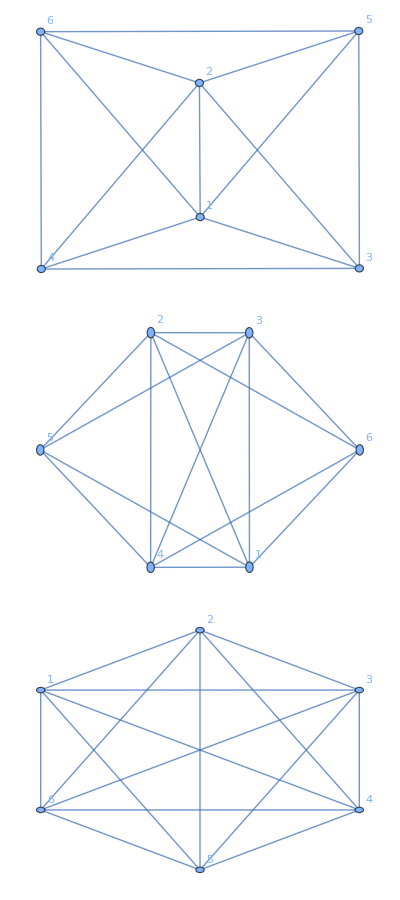

```mathematica
Column[Map[SetProperty[#, VertexLabels->Automatic]&, sixVGraphs[[-3;;]]]]
```

#### Entropy Vectors from the Adjacency Matrix

Next, we compute the entropy vector for every graph by feeding its adjacency matrix to ComputeEntropyVectorsAdj:

```mathematica
sixQGraphStatesSvecs = ComputeEntropyVectorsAdj[Map[AdjacencyMatrix, sixVGraphs]];
```

Because permutations of qubits yield equivalent entropy vectors, we identify vectors that are related by qubit exchange and keep a single representative of each symmetry orbit:

```mathematica
{baseVector, eqVectors}=EquivalentEntropyVectors[6];
sixQSvecsSymmetryOrbit=UniqueOrbits[sixQGraphStatesSvecs, baseVector, eqVectors]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1},{1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,1,1,1,1,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2},{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,2,2,1,1,2,2,1,2,2,2,2,0,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,1,1,1,2,2,1,1,2,2,1,2,2,2,2,1,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,1,1,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}}

Hence there are 26 distinct entropy vector symmetry orbits at six qubits.

#### Graph Representatives That Do Not Violate MMI

For each entropy‑vector orbit we would like a graph representative that does not violate the monogamy of mutual information (MMI) inequality.  The procedure is:

1. Enumerate all disjoint triples (i.e., every length-three list of pairwise disjoint system subsets) for six qubits.

```mathematica
sixQTriples=DisjointTriples[6];
```

2. Use MMIChecker to retain only those orbit representatives whose entropy vectors satisfy/saturate every MMI instance:

```mathematica
MMInonFailingSixQSvecs =Select[sixQSvecsSymmetryOrbit,( MMIChecker[#, sixQTriples]== True)&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1},{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2},{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}}

3. Locate, inside sixVGraphs, the first graph that corresponds to a state that does not violate MMI:

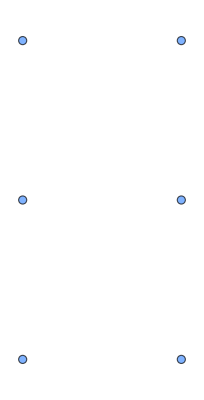
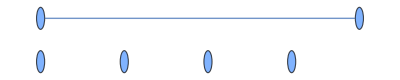
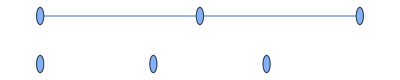
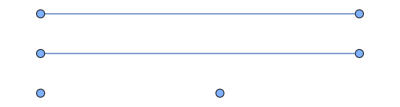
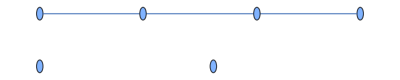
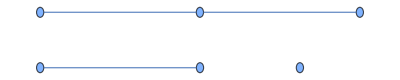
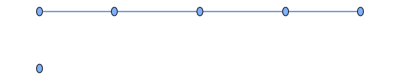
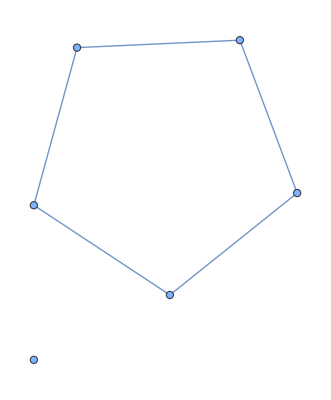

```mathematica
positionsMMInonFailingSixQSvecs =Flatten @Map[findFirstIndex[sixQGraphStatesSvecs, # ] &, Map[PermuteEntropyVector[#, baseVector, eqVectors ] &, MMInonFailingSixQSvecs]];
nonFailingGraphs=sixVGraphs[[positionsMMInonFailingSixQSvecs]]
```

We can associate each graph to the entropy vector of the graph state it represents:

```mathematica
nonFailingGraphInstance = AssociationThread[MMInonFailingSixQSvecs->nonFailingGraphs]
```

<|{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→-Graphics-,{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1}→-Graphics-,{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1}→-Graphics-,{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1}→-Graphics-,{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1}→-Graphics-,{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2}→-Graphics-,{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1}→-Graphics-,{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2}→-Graphics-,{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3}→-Graphics-,{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}→-Graphics-|>

#### LC-Equivalence of Graphs that Belong to non MMI-failing Graphs

Inspection shows that every connected graph in the non‑MMI‑failing set is locally complement (LC) equivalent to one of four graph families: sunlet, path, cycle, and wheel graphs. The single outlier,

, is LC‑equivalent to the six‑vertex wheel, as shown below:

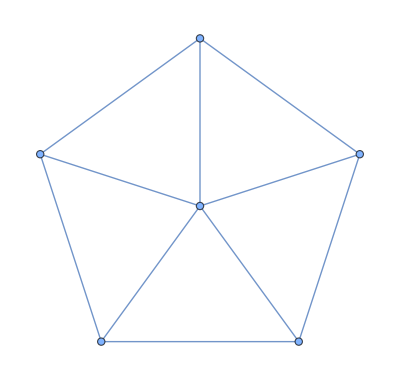
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@ -Graphics-]
```

True

### Graphs on Seven Vertices (Generation by Random Exploration)

#### Finding Non-MMI Failing Graph Representatives for Every Symmetry Orbit

Exhaustively listing the 2^(21) seven‑vertex simple undirected graphs is computationally heavy, yet we need only one graph per entropy‑vector orbit.  Fortunately, the number of symmetry orbits at n ≤ 12 is known (see arXiv:0504.4522). We exploit this fact:  a function generateSymmetryOrbitGraphRepresentatives samples random graphs until it has found a representative for each of the 59 orbits at seven qubits.  A typical call looks like

```mathematica
SeedRandom[314];
```

```mathematica
sevenVGraphSymmetryOrbits=generateSymmetryOrbitGraphRepresentatives[7,59];
```

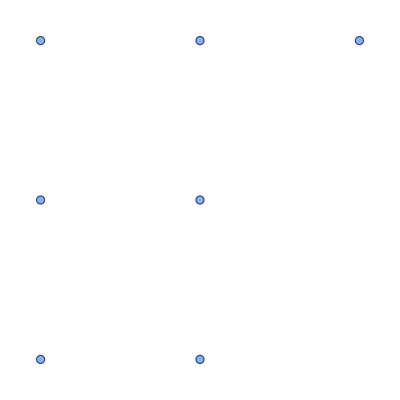
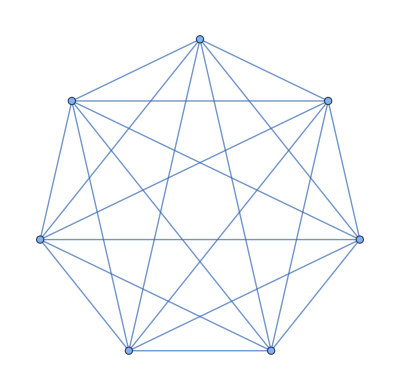
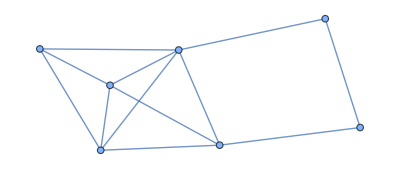
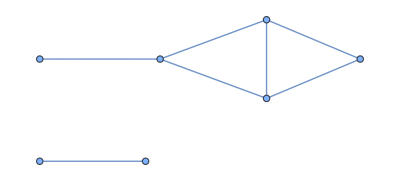
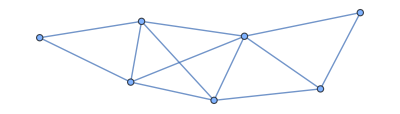
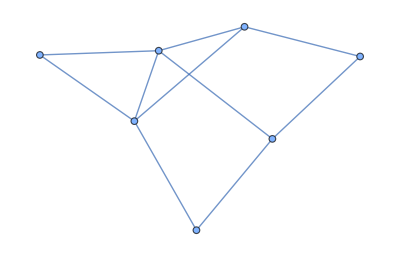
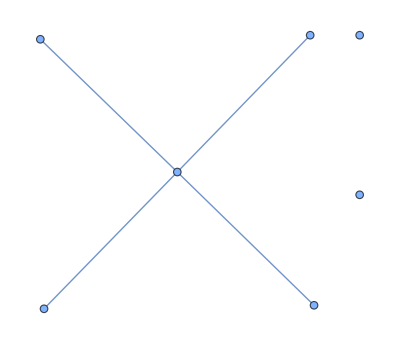
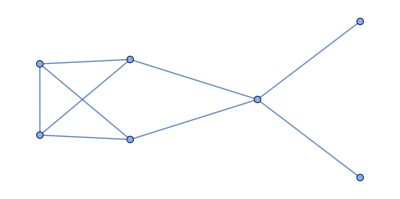

```mathematica
Map[AdjacencyGraph, sevenVGraphSymmetryOrbits]
```

#### Seven‑Qubit Graph States That Do Not Violate MMI

We again build the list of disjoint triples, test every candidate entropy vector with MMIChecker, and convert each remaining graph to a canonical form so its family is more evident:

```mathematica
sevenQTriples=DisjointTriples[7];
```

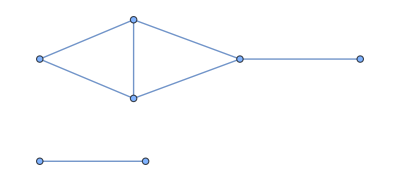
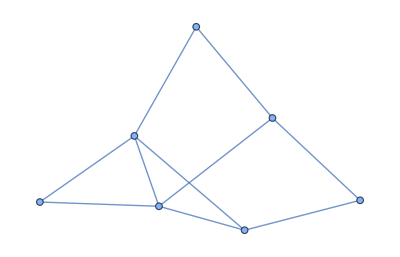
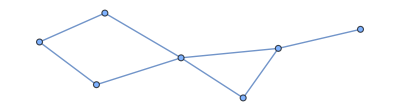
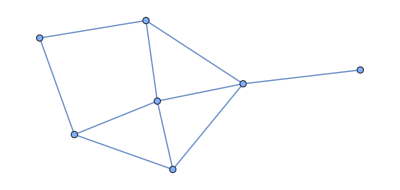
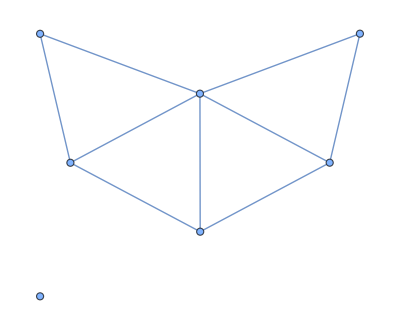
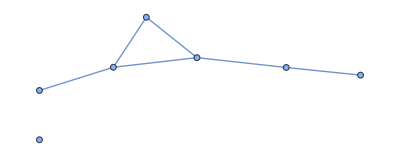
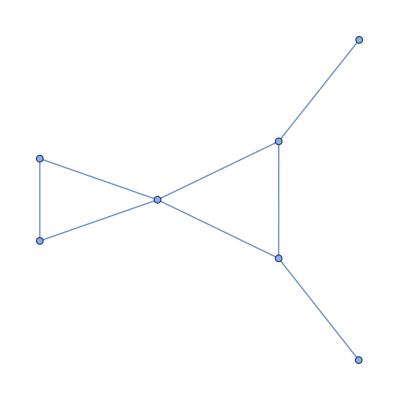
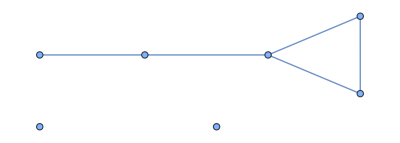
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MMInonFailingSevenGraphs =Select[sevenVGraphSymmetryOrbits, (MMIChecker[ComputeEntropyVectorsAdj[{#}][[1]], sevenQTriples]==True)&];
MMInonFailingSevenGraphs= Map[CanonicalGraph[AdjacencyGraph[#]]&, MMInonFailingSevenGraphs]
```

Connected graphs in MMInonFailingSevenGraphs interestingly, are exactly of a composition of path, cycle, sunlet, or wheel graphs:

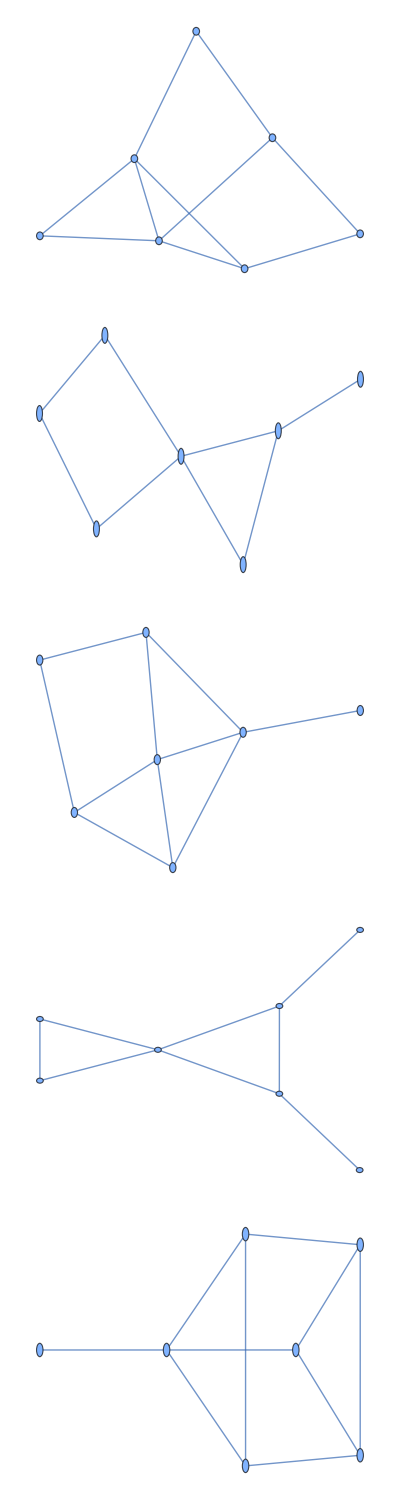

```mathematica
MMInonFailingSevenGraphsConnected=Select[MMInonFailingSevenGraphs, ConnectedGraphQ];
Column[MMInonFailingSevenGraphsConnected]
```

The second connected graph is LC equivalent to a path graph:

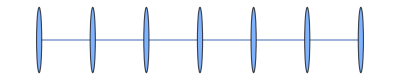
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@-Graphics-]
```

True

The first connected graph is LC equivalent to a cycle graph:

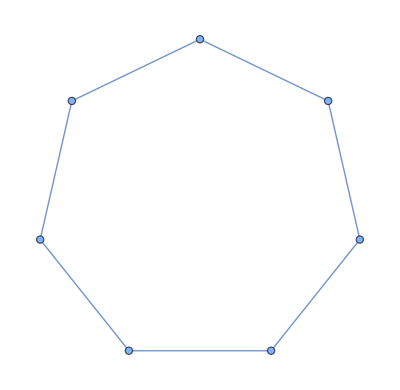
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

The fourth connected graph is a composition of a sunlet and a path graph.

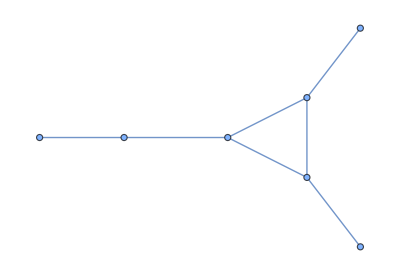
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

The third connected graph is LC equivalent to a composition of cycle graphs and a path graph :

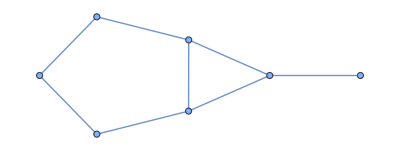
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@ -Graphics-]
```

True

Finally, the fifth  connected graph is LC equivalent to a composition of a wheel graph and a path graph:

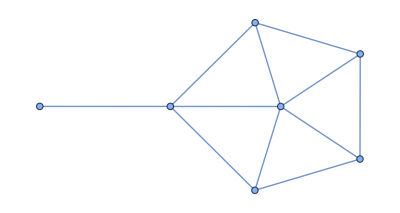
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

Interestingly, the wheel graph on 7 vertices fails MMI:

```mathematica
MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@-Graphics-}][[1]], sevenQTriples]
```

False

However, it satisfies MMI again at 8 vertices:

False

```mathematica
MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@-Graphics-}][[1]], DisjointTriples[8]]
```

True

## Paper Results

## Section 4.4: Evidence of the Sufficiency of a Non-trivial Intersection for MMI Failure

The function allGeneralizedGraphsnoInnerNonTrivialInterInfo generates all generalized graphs from Section 4.3 (ignoring intra-region adjacencies) that exhibit at least one non-trivial intersection for some triple of the form {C, I, J}. Additionally, it provides the specific triples where such intersections occur.

We demonstrate exhaustively, up to n=8, that every such graph fails every MMI instance involving a non-trivial intersection. For n=9, we switch to a sampling-based approach using SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples, which randomly explores the space of Section 4.3-type adjacency matrices in search of graphs with at least one non-trivial intersection. While some connected graphs at n=9 do show saturation in certain MMI instances, we have not observed a single connected graph with a non-trivial intersection that satisfies its corresponding MMI instance.

### Data Gathering and Evaluation Procedure

For each n, we:
	1. Generate all graphs with at least one non-trivial intersection.
	2. Remove isomorphic duplicates.
	3. Use MMICheckerEntropyInput to evaluate each triple {C, I, J} that exhibits a non-trivial intersection.

### Generalized G Graphs With a Non-trivial Intersection

#### n=4

```mathematica
generalizedGraphFourVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[4];
generalizedGraphFourVInfo= DeleteDuplicates[generalizedGraphFourVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Only one unique graph remains:

```mathematica
generalizedGraphsFour=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphFourVInfo]
```

{-Graphics-}

MMI evaluations:

```mathematica
generalizedGraphsMMIEvaluationsFour=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphFourVInfo];
```

Notice how all such instances are failed:

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsFour ]
```

{True}

This same procedure is repeated for n = 5 through n = 8. In each case, every graph fails for all corresponding non-trivial intersection triples.

#### n = 5

```mathematica
generalizedGraphFiveVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[5];
generalizedGraphFiveVInfo= DeleteDuplicates[generalizedGraphFiveVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsFive=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphFiveVInfo]
```

{-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsFive=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphFiveVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsFive ]
```

{True,True,True}

#### n = 6

```mathematica
generalizedGraphSixVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[6];
generalizedGraphSixVInfo= DeleteDuplicates[generalizedGraphSixVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsSix=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphSixVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsSix=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphSixVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSix ]
```

{True,True,True,True,True,True,True,True,True,True,True}

#### n = 7

```mathematica
generalizedGraphSevenVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[7];
generalizedGraphSevenVInfo= DeleteDuplicates[generalizedGraphSevenVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsSeven=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphSevenVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsSeven=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphSevenVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSeven ]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### n = 8

```mathematica
generalizedGraphEightVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[8];
generalizedGraphEightVInfo= DeleteDuplicates[generalizedGraphEightVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsEight=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphEightVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsEight=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphEightVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSeven ]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### n = 9: Sampling-Based Search

Due to computational limits, we use random sampling to generate graphs with potential non-trivial intersections:

```mathematica
SeedRandom[314159];
```

```mathematica
generalizedGraphNineVInfo=SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[9, 50];
generalizedGraphNineVInfo= DeleteDuplicates[generalizedGraphNineVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

The graphs we obtained by randomly sampling 50 of our generalized graphs for each center size are shown below:

```mathematica
generalizedGraphsNine=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphNineVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Filtering for connected graphs:

```mathematica
generalizedGraphsNineConnectedInfo =Select[generalizedGraphNineVInfo,ConnectedGraphQ[AdjacencyGraph@#[[1]]]&];
generalizedGraphsNineConnected = Select[generalizedGraphsNine, ConnectedGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs above fail whenever a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsConnectedNine=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphsNineConnectedInfo];
```

```mathematica
fullyFailsIntNineQ=Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsConnectedNine ]
```

{True,True,True,True,True,False,True,False,True,False,True,False,False,True,True,True,False,True,True,True,True,False,True,False}

The pattern breaks! The following graphs saturate certain MMI instances where a non-trivial intersection occurs:

```mathematica
posNinenoFullFail=Flatten@Position[fullyFailsIntNineQ, False];
```

```mathematica
generalizedGraphsNineConnected[[posNinenoFullFail]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Among these connected graphs, only failure and saturation (not satisfaction) occurs:

```mathematica
Map[Select[#, (#!="Fails")&]&, generalizedGraphsMMIEvaluationsConnectedNine[[posNinenoFullFail]]]
```

{{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates}}

To determine which triples are involved in the saturated instances:

```mathematica
triplesSaturateNineIndices=Map[(Flatten@(Position[#, "Saturates"]))&, generalizedGraphsMMIEvaluationsConnectedNine[[posNinenoFullFail]]]
```

{{28,29,36,37,39,40},{35,36,38,39,46,48},{25,26,27,28,29,30,31,32,34,35,37,38,40,41,43,45,47,49,51,53,55},{34,35,36,37,40,45},{25,26,28,29,31,32,34,35,36,37,38,39,40,41,43,45,47,49,50,51,52},{31,32,34,35,41,42},{28,29,36,37,45,46},{28,29,36,37,39,46}}

```mathematica
MapThread[Part,{generalizedGraphsNineConnectedInfo[[posNinenoFullFail]][[All,2]],triplesSaturateNineIndices}]
```

{{{{1,2,3},{4,7},{5,6}},{{1,2,3},{4,7},{8,9}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,6},{8,9}}},{{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{5,8},{6,7}},{{1,2,3},{5,9},{6,7}}},{{{1,2,3},{4,5},{6,7}},{{1,2,3},{4,5},{6,8}},{{1,2,3},{4,5},{6,9}},{{1,2,3},{4,5},{7,8}},{{1,2,3},{4,5},{7,9}},{{1,2,3},{4,5},{8,9}},{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,7},{5,8}},{{1,2,3},{4,7},{6,9}},{{1,2,3},{4,8},{5,7}},{{1,2,3},{4,8},{6,9}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,7},{6,9}},{{1,2,3},{5,8},{6,9}},{{1,2,3},{5,9},{7,8}},{{1,2,3},{6,7},{8,9}},{{1,2,3},{6,8},{7,9}},{{1,2,3},{6,9},{7,8}}},{{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,8},{6,7}}},{{{1,2,3},{4,5},{6,7}},{{1,2,3},{4,5},{8,9}},{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,7},{5,9}},{{1,2,3},{4,7},{6,8}},{{1,2,3},{4,8},{5,6}},{{1,2,3},{4,8},{5,7}},{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{4,8},{6,9}},{{1,2,3},{4,8},{7,9}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{5,6},{7,9}},{{1,2,3},{5,7},{6,9}},{{1,2,3},{5,8},{6,7}},{{1,2,3},{5,9},{6,7}},{{1,2,3},{5,9},{6,8}},{{1,2,3},{5,9},{7,8}},{{1,2,3},{6,7},{8,9}}},{{{1,2,3},{4,6},{5,8}},{{1,2,3},{4,6},{7,9}},{{1,2,3},{4,7},{5,8}},{{1,2,3},{4,7},{6,9}},{{1,2,3},{5,8},{6,9}},{{1,2,3},{5,8},{7,9}}},{{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{5,9},{6,7}},{{1,2,3},{5,9},{7,8}}},{{{1,2,3},{4,5},{6,9}},{{1,2,3},{4,5},{7,8}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{6,9},{7,8}}}}

These outputs list the specific {C, I, J} triples corresponding to saturation. Despite this, no case of success has been observed for any triple in a connected graph with a non-trivial intersection.

## Section 4.4: Evidence of Non-MMI Failure for Different Families of Graphs

We now briefly examine the MMI failure status for three well-known families of graphs: path graphs, cycle graphs, and wheel graphs. Notably, up to  n=9, both path and cycle graphs consistently yield graph states that satisfy/saturate all MMI inequalities, none fail.

### Path Graphs

```mathematica
PnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@PathGraph[Range[n]]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{True,True,True,True,True,True}

### Cycle Graphs

```mathematica
CnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@CycleGraph[n]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{True,True,True,True,True,True}

### Wheel Graphs

In contrast, wheel graphs exhibit a more nuanced pattern. They fail  MMI at n=4, satisfy/saturate it for n=5 and n=6, fail again at n=7, and satisfy/saturate it once more for n=8 and n=9.

```mathematica
WnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@WheelGraph[n]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{False,True,True,False,True,True}

## Appendix A.3: Tables 10-12

```mathematica
SetDirectory["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8"]
```

C:\Users\Kaoti\OneDrive\Escritorio\Research\MMI Failure for Graph States\Data\MMI-Failure-Stars-n=8

Now, we present the procedure to replicate the data available in Tables 10-12 in the appendix A.3 in our paper.

First, we obtain graph representatives for each unique entropy vector at n=8.

```mathematica
graphRepsSymmetryOrbitsEight = generateSymmetryOrbitGraphRepresentatives[8, 182];
```

#### Generalized Star Representatives

```mathematica
starRepsSymmetryOrbitsEight=findStarGraphReps[graphRepsSymmetryOrbitsEight, 8];
```

```mathematica
Map[AdjacencyGraph, starRepsSymmetryOrbitsEight]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Identify MMI Failing and Satisfying Cases

Now, we filter graph states in graphRepsSymmetryOrbitsEight according to whether they fail MMI or not:

```mathematica
uniqueEntropyVectorsEight=ComputeEntropyVectorsAdj[graphRepsSymmetryOrbitsEight];
triplesEight=DisjointTriples[8];
```

```mathematica
Length@triplesEight
```

7770

```mathematica
evalsBool =ParallelMap[MMIChecker[#, triplesEight]&, uniqueEntropyVectorsEight];

starRepsFailMMI=Pick[starRepsSymmetryOrbitsEight, evalsBool, False];
starRepsSatisfyMMI=Pick[starRepsSymmetryOrbitsEight, evalsBool, True];
```

#### Minimal-Edge Stars with Nontrivial Intersection

Next, we exhaustively check every LC orbit to identify a minimal edge star representative that has a nontrivial intersection for some valid choice of (C, I, J ). If exists, choose the minimal edge rep satisfying those conditions .

```mathematica
minimalStarSatisfyMMINontrivialInt=searchNonTrivialIntLC[starRepsSatisfyMMI,triplesEight];

minimalStarFailMMINontrivialInt =searchNonTrivialIntLC[starRepsFailMMI,triplesEight];

minimalStarFailMMINontrivialIntAbsent = Select[minimalStarFailMMINontrivialInt, (#[[2]]=={})&];
minimalStarFailMMINontrivialIntPresent = Complement[minimalStarFailMMINontrivialInt,minimalStarFailMMINontrivialIntAbsent ];
```

```mathematica
Print["Table 11 graphs"];
Map[AdjacencyGraph, minimalStarSatisfyMMINontrivialInt[[All,1]]]
Print["Table 12 graphs"];
Map[AdjacencyGraph, minimalStarFailMMINontrivialIntPresent[[All,1]]]
Print["Table 13 graphs"];
Map[AdjacencyGraph, minimalStarFailMMINontrivialIntAbsent[[All,1]]]
```

Table 11 graphs

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Table 12 graphs

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Table 13 graphs

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Identifying a Relevant MMI Failed Instance

For those that fail, identify largest failing instance of type (C,I,J) for those that showcase a nontrivial intersection, and simply largest instance for those that do not .

```mathematica
minimalStarNonTFailCIJ=Module[{evals, failed,lenghtsFailed},ParallelTable[
triplesCenter=InstancesCIJ[starFailCIJ,triplesEight,8 ];
evals=MMICheckerInputSelectTriples[(ComputeEntropyVectorsAdj[{starFailCIJ}])[[1]], triplesCenter];

failed=Pick[triplesCenter, evals, "Fails"];
lenghtsFailed=  Map[Length[Flatten[#]]&, failed];

{starFailCIJ,First[Pick[failed, lenghtsFailed, Max[lenghtsFailed]]]}

, {starFailCIJ, (minimalStarFailMMINontrivialIntPresent[[All,1]])}]];

minimalStarNoCIJFail=Module[{evals, failed,lenghtsFailed},
ParallelTable[
evals=MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{starFailnoCIJ}][[1]], triplesEight];

failed=Pick[triplesEight, evals, "Fails"];
lenghtsFailed=  Map[Length[Flatten[#]]&, failed];
{starFailnoCIJ,First[Pick[failed, lenghtsFailed, Max[lenghtsFailed]]]}

, {starFailnoCIJ, minimalStarFailMMINontrivialIntAbsent[[All,1]]}]];
```

Finally, we compute MMI evaluation count and organize from least to greatest satisfy/fail count , giving the actual ordering seen in the tables.

```mathematica
(*Length of longest simple path per component=diameter*)
componentDiameters[adj_]:=Module[{G},G=AdjacencyGraph[Unitize@adj,DirectedEdges->False];
GraphDiameter/@(Subgraph[G,#]&/@ConnectedComponents[G])];

(*Tie-break tuple:{max,#max,secondMax,#secondMax}*)
pathTieBreaker[adj_]:=Module[{diams=componentDiameters[adj],maxD,cntMax,secondD,cntSecond},If[diams==={},Return[{0,0,0,0}]];
maxD=Max[diams];
cntMax=Count[diams,maxD];
secondD=If[Length[DeleteDuplicates[diams]]>=2,Max@DeleteCases[diams,maxD],0];
cntSecond=Count[diams,secondD];
{maxD,cntMax,secondD,cntSecond}];
```

```mathematica
satisfySvecs=ComputeEntropyVectorsAdj[minimalStarSatisfyMMINontrivialInt[[All,1]]];
evalsSatisfy=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, satisfySvecs];
evalsSatisfyCount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsSatisfy];
minimalStarSatisfyMMINontrivialIntCount=Join[minimalStarSatisfyMMINontrivialInt,evalsSatisfyCount,2 ];
starRepsSatisfyMMICount=SortBy[minimalStarSatisfyMMINontrivialIntCount,{#[[3,1]]&,Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];

FailsCIJSvecs=ComputeEntropyVectorsAdj[minimalStarNonTFailCIJ[[All,1]]];
evalsFailsCIJ=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, FailsCIJSvecs];
evalsFailsCIJcount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsFailsCIJ];
minimalStarNonTFailCIJCount=Join[minimalStarNonTFailCIJ,evalsFailsCIJcount,2 ];
minimalStarNonTFailCIJCount=SortBy[minimalStarNonTFailCIJCount,{#[[3,3]]&, Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];

FailsnoCIJSvecs=ComputeEntropyVectorsAdj[minimalStarNoCIJFail[[All,1]]];
evalsFailsnoCIJ=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, FailsnoCIJSvecs];
evalsFailsnoCIJcount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsFailsnoCIJ];
minimalStarTFailnoCIJCount=Join[minimalStarNoCIJFail,evalsFailsnoCIJcount,2 ];
minimalStarTFailnoCIJCount=SortBy[minimalStarTFailnoCIJCount,{#[[3,3]]&, Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];
```

#### Tables 10-12 Construction

Finally, we call TikZTableFromAdjTriples to directly generate Table 10 - 12

```mathematica
Print["Table 11"];
TikZTableFromAdjTriples[starRepsSatisfyMMICount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
Print["Table 12"];
TikZTableFromAdjTriples[minimalStarNonTFailCIJCount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
Print["Table 13"];
TikZTableFromAdjTriples[minimalStarTFailnoCIJCount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"ABC"]
```

Table 11

\begin{longtable}{>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}}
\endfirsthead
\endhead
\endfoot
\endlastfoot
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (3.290,0.980) {\scriptsize 1};
\node[Knode] (v2) at (0.210,3.290) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.750) {\scriptsize 3};
\node[Knode] (v4) at (1.750,3.290) {\scriptsize 4};
\node[Knode] (v5) at (1.750,1.750) {\scriptsize 5};
\node[Knode] (v6) at (0.210,0.210) {\scriptsize 6};
\node[Knode] (v7) at (1.750,0.210) {\scriptsize 7};
\node[Knode] (v8) at (3.290,3.290) {\scriptsize 8};
\begin{scope}[on background layer]

\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (1)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (2.868,1.695) {\scriptsize 1};
\node[Knode] (v2) at (2.337,1.695) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.695) {\scriptsize 3};
\node[Knode] (v4) at (0.742,1.695) {\scriptsize 4};
\node[Knode] (v5) at (1.273,1.695) {\scriptsize 5};
\node[Knode] (v6) at (1.805,1.695) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.805) {\scriptsize 7};
\node[Knode] (v8) at (0.210,1.805) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (2)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (2.713,1.493) {\scriptsize 1};
\node[Knode] (v2) at (1.878,1.493) {\scriptsize 2};
\node[Knode] (v3) at (1.044,1.493) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.493) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.007) {\scriptsize 5};
\node[Knode] (v6) at (0.210,2.007) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.750) {\scriptsize 7};
\node[Knode] (v8) at (0.210,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (3)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (2.777,1.686) {\scriptsize 1};
\node[Knode] (v2) at (2.135,1.686) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.686) {\scriptsize 3};
\node[Knode] (v4) at (0.852,1.686) {\scriptsize 4};
\node[Knode] (v5) at (1.493,1.686) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.814) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.814) {\scriptsize 7};
\node[Knode] (v8) at (1.748,1.814) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (4)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (1.981,1.057) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.057) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.981) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.981) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.443) {\scriptsize 5};
\node[Knode] (v6) at (0.210,2.443) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.519) {\scriptsize 7};
\node[Knode] (v8) at (0.210,1.519) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (5)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (3.078,1.634) {\scriptsize 1};
\node[Knode] (v2) at (2.636,1.634) {\scriptsize 2};
\node[Knode] (v3) at (2.193,1.634) {\scriptsize 3};
\node[Knode] (v4) at (1.750,1.634) {\scriptsize 4};
\node[Knode] (v5) at (0.210,1.634) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.866) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.866) {\scriptsize 7};
\node[Knode] (v8) at (1.748,1.866) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (6)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (3.290,0.595) {\scriptsize 1};
\node[Knode] (v2) at (0.210,0.595) {\scriptsize 2};
\node[Knode] (v3) at (3.290,2.905) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.905) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.135) {\scriptsize 5};
\node[Knode] (v6) at (0.210,2.135) {\scriptsize 6};
\node[Knode] (v7) at (3.290,1.365) {\scriptsize 7};
\node[Knode] (v8) at (0.210,1.365) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (7)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (2.713,1.365) {\scriptsize 1};
\node[Knode] (v2) at (1.750,1.365) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.365) {\scriptsize 3};
\node[Knode] (v4) at (1.750,1.750) {\scriptsize 4};
\node[Knode] (v5) at (0.210,1.750) {\scriptsize 5};
\node[Knode] (v6) at (0.210,2.135) {\scriptsize 6};
\node[Knode] (v7) at (3.290,2.135) {\scriptsize 7};
\node[Knode] (v8) at (1.748,2.135) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (8)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (1.943,1.365) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.365) {\scriptsize 2};
\node[Knode] (v3) at (0.210,2.135) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.135) {\scriptsize 4};
\node[Knode] (v5) at (0.210,1.750) {\scriptsize 5};
\node[Knode] (v6) at (3.290,1.750) {\scriptsize 6};
\node[Knode] (v7) at (1.748,2.135) {\scriptsize 7};
\node[Knode] (v8) at (1.748,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (9)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,7770,0)};
\node[Knode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.750) {\scriptsize 2};
\node[Knode] (v3) at (0.210,2.392) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.392) {\scriptsize 4};
\node[Knode] (v5) at (1.750,1.108) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.108) {\scriptsize 6};
\node[Knode] (v7) at (1.748,1.750) {\scriptsize 7};
\node[Knode] (v8) at (1.748,2.392) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (10)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6746,0)};
\node[Knode] (v1) at (2.636,1.673) {\scriptsize 1};
\node[Knode] (v2) at (1.827,1.673) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.673) {\scriptsize 3};
\node[Knode] (v4) at (1.019,1.673) {\scriptsize 4};
\node[Knode] (v5) at (3.290,1.827) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.827) {\scriptsize 6};
\node[Knode] (v7) at (2.296,1.827) {\scriptsize 7};
\node[Knode] (v8) at (1.202,1.827) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (11)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6746,0)};
\node[Knode] (v1) at (2.777,1.622) {\scriptsize 1};
\node[Knode] (v2) at (2.007,1.622) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.878) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.878) {\scriptsize 4};
\node[Knode] (v5) at (1.238,1.622) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.622) {\scriptsize 6};
\node[Knode] (v7) at (2.296,1.878) {\scriptsize 7};
\node[Knode] (v8) at (1.202,1.878) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (12)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6746,0)};
\node[Knode] (v1) at (3.290,1.964) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.964) {\scriptsize 2};
\node[Knode] (v3) at (2.992,1.536) {\scriptsize 3};
\node[Knode] (v4) at (1.964,1.536) {\scriptsize 4};
\node[Knode] (v5) at (1.238,1.536) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.536) {\scriptsize 6};
\node[Knode] (v7) at (2.296,1.964) {\scriptsize 7};
\node[Knode] (v8) at (1.202,1.964) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (13)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6746,0)};
\node[Knode] (v1) at (2.992,1.536) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.964) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.964) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.536) {\scriptsize 4};
\node[Knode] (v5) at (2.266,1.536) {\scriptsize 5};
\node[Knode] (v6) at (2.296,1.964) {\scriptsize 6};
\node[Knode] (v7) at (1.202,1.964) {\scriptsize 7};
\node[Knode] (v8) at (1.237,1.536) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (14)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1536,6234,0)};
\node[Knode] (v1) at (2.392,1.654) {\scriptsize 1};
\node[Knode] (v2) at (1.301,1.654) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.654) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.846) {\scriptsize 4};
\node[Knode] (v5) at (3.290,1.846) {\scriptsize 5};
\node[Knode] (v6) at (1.750,1.846) {\scriptsize 6};
\node[Knode] (v7) at (0.928,1.846) {\scriptsize 7};
\node[Knode] (v8) at (2.571,1.846) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (15)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1536,6234,0)};
\node[Knode] (v1) at (2.296,1.590) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.910) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.910) {\scriptsize 3};
\node[Knode] (v4) at (0.982,1.590) {\scriptsize 4};
\node[Knode] (v5) at (0.210,1.590) {\scriptsize 5};
\node[Knode] (v6) at (1.750,1.910) {\scriptsize 6};
\node[Knode] (v7) at (0.928,1.910) {\scriptsize 7};
\node[Knode] (v8) at (2.571,1.910) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (16)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1536,6234,0)};
\node[Knode] (v1) at (0.210,2.039) {\scriptsize 1};
\node[Knode] (v2) at (3.290,2.039) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.461) {\scriptsize 3};
\node[Knode] (v4) at (1.753,1.461) {\scriptsize 4};
\node[Knode] (v5) at (1.750,2.039) {\scriptsize 5};
\node[Knode] (v6) at (0.928,2.039) {\scriptsize 6};
\node[Knode] (v7) at (2.571,2.039) {\scriptsize 7};
\node[Knode] (v8) at (0.981,1.461) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (17)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1952,5818,0)};
\node[Knode] (v1) at (3.290,1.365) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.365) {\scriptsize 2};
\node[Knode] (v3) at (3.290,2.135) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.135) {\scriptsize 4};
\node[Knode] (v5) at (2.296,1.365) {\scriptsize 5};
\node[Knode] (v6) at (1.202,1.365) {\scriptsize 6};
\node[Knode] (v7) at (2.296,2.135) {\scriptsize 7};
\node[Knode] (v8) at (1.202,2.135) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (18)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2368,5402,0)};
\node[Knode] (v1) at (1.878,1.622) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.622) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.878) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.878) {\scriptsize 4};
\node[Knode] (v5) at (2.086,1.878) {\scriptsize 5};
\node[Knode] (v6) at (1.413,1.878) {\scriptsize 6};
\node[Knode] (v7) at (2.734,1.878) {\scriptsize 7};
\node[Knode] (v8) at (0.765,1.878) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (19)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2368,5402,0)};
\node[Knode] (v1) at (3.290,1.981) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.981) {\scriptsize 2};
\node[Knode] (v3) at (0.828,1.519) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.519) {\scriptsize 4};
\node[Knode] (v5) at (2.086,1.981) {\scriptsize 5};
\node[Knode] (v6) at (1.413,1.981) {\scriptsize 6};
\node[Knode] (v7) at (2.734,1.981) {\scriptsize 7};
\node[Knode] (v8) at (0.765,1.981) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (20)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2560,5210,0)};
\node[Knode] (v1) at (2.454,0.210) {\scriptsize 1};
\node[Knode] (v2) at (1.394,0.210) {\scriptsize 2};
\node[Knode] (v3) at (0.335,0.210) {\scriptsize 3};
\node[Knode] (v4) at (0.335,1.520) {\scriptsize 4};
\node[Knode] (v5) at (1.797,0.558) {\scriptsize 5};
\node[Knode] (v6) at (0.799,3.210) {\scriptsize 6};
\node[Knode] (v7) at (3.165,1.651) {\scriptsize 7};
\node[Knode] (v8) at (2.550,3.290) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (21)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2560,5210,0)};
\node[Knode] (v1) at (2.838,0.210) {\scriptsize 1};
\node[Knode] (v2) at (2.060,0.210) {\scriptsize 2};
\node[Knode] (v3) at (0.446,0.210) {\scriptsize 3};
\node[Knode] (v4) at (0.446,1.659) {\scriptsize 4};
\node[Knode] (v5) at (1.794,0.772) {\scriptsize 5};
\node[Knode] (v6) at (0.873,3.216) {\scriptsize 6};
\node[Knode] (v7) at (3.054,1.779) {\scriptsize 7};
\node[Knode] (v8) at (2.487,3.290) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (22)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2560,5210,0)};
\node[Knode] (v1) at (0.354,0.210) {\scriptsize 1};
\node[Knode] (v2) at (3.146,0.210) {\scriptsize 2};
\node[Knode] (v3) at (0.354,1.880) {\scriptsize 3};
\node[Knode] (v4) at (1.520,1.113) {\scriptsize 4};
\node[Knode] (v5) at (0.724,3.226) {\scriptsize 5};
\node[Knode] (v6) at (2.610,1.984) {\scriptsize 6};
\node[Knode] (v7) at (2.119,3.290) {\scriptsize 7};
\node[Knode] (v8) at (1.749,0.210) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (23)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2880,4890,0)};
\node[Knode] (v1) at (1.984,0.210) {\scriptsize 1};
\node[Knode] (v2) at (0.246,0.210) {\scriptsize 2};
\node[Knode] (v3) at (0.246,0.693) {\scriptsize 3};
\node[Knode] (v4) at (1.759,3.290) {\scriptsize 4};
\node[Knode] (v5) at (3.254,0.678) {\scriptsize 5};
\node[Knode] (v6) at (1.218,1.247) {\scriptsize 6};
\node[Knode] (v7) at (1.756,2.171) {\scriptsize 7};
\node[Knode] (v8) at (2.288,1.242) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (24)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2880,4890,0)};
\node[Knode] (v1) at (0.408,0.972) {\scriptsize 1};
\node[Knode] (v2) at (1.758,3.290) {\scriptsize 2};
\node[Knode] (v3) at (3.092,0.959) {\scriptsize 3};
\node[Knode] (v4) at (1.385,0.210) {\scriptsize 4};
\node[Knode] (v5) at (0.408,0.210) {\scriptsize 5};
\node[Knode] (v6) at (1.275,1.467) {\scriptsize 6};
\node[Knode] (v7) at (1.756,2.291) {\scriptsize 7};
\node[Knode] (v8) at (2.230,1.462) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (25)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2880,4890,0)};
\node[Knode] (v1) at (1.966,0.482) {\scriptsize 1};
\node[Knode] (v2) at (0.210,0.482) {\scriptsize 2};
\node[Knode] (v3) at (3.290,2.919) {\scriptsize 3};
\node[Knode] (v4) at (2.271,1.966) {\scriptsize 4};
\node[Knode] (v5) at (1.246,3.018) {\scriptsize 5};
\node[Knode] (v6) at (0.210,1.966) {\scriptsize 6};
\node[Knode] (v7) at (3.289,1.011) {\scriptsize 7};
\node[Knode] (v8) at (1.244,0.914) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (26)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2880,4890,0)};
\node[Knode] (v1) at (2.003,0.262) {\scriptsize 1};
\node[Knode] (v2) at (0.210,0.262) {\scriptsize 2};
\node[Knode] (v3) at (3.290,3.139) {\scriptsize 3};
\node[Knode] (v4) at (2.271,2.186) {\scriptsize 4};
\node[Knode] (v5) at (1.246,3.238) {\scriptsize 5};
\node[Knode] (v6) at (0.210,2.186) {\scriptsize 6};
\node[Knode] (v7) at (3.289,1.231) {\scriptsize 7};
\node[Knode] (v8) at (1.244,1.134) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (27)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2976,4794,0)};
\node[Knode] (v1) at (0.210,1.557) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.942) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.942) {\scriptsize 3};
\node[Knode] (v4) at (1.188,1.943) {\scriptsize 4};
\node[Knode] (v5) at (2.310,1.943) {\scriptsize 5};
\node[Knode] (v6) at (1.749,1.943) {\scriptsize 6};
\node[Knode] (v7) at (0.658,1.943) {\scriptsize 7};
\node[Knode] (v8) at (2.841,1.943) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (28)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3008,4762,0)};
\node[Knode] (v1) at (1.983,0.210) {\scriptsize 1};
\node[Knode] (v2) at (0.258,0.210) {\scriptsize 2};
\node[Knode] (v3) at (0.980,0.705) {\scriptsize 3};
\node[Knode] (v4) at (0.258,2.012) {\scriptsize 4};
\node[Knode] (v5) at (2.471,0.676) {\scriptsize 5};
\node[Knode] (v6) at (1.030,3.290) {\scriptsize 6};
\node[Knode] (v7) at (3.242,1.953) {\scriptsize 7};
\node[Knode] (v8) at (2.523,3.260) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (29)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3008,4762,0)};
\node[Knode] (v1) at (1.750,0.210) {\scriptsize 1};
\node[Knode] (v2) at (0.437,0.210) {\scriptsize 2};
\node[Knode] (v3) at (1.072,1.015) {\scriptsize 3};
\node[Knode] (v4) at (0.437,2.165) {\scriptsize 4};
\node[Knode] (v5) at (2.384,0.990) {\scriptsize 5};
\node[Knode] (v6) at (1.116,3.290) {\scriptsize 6};
\node[Knode] (v7) at (3.063,2.114) {\scriptsize 7};
\node[Knode] (v8) at (2.430,3.263) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (30)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3424,4346,0)};
\node[Knode] (v1) at (0.210,0.373) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.022) {\scriptsize 2};
\node[Knode] (v3) at (3.290,3.127) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.074) {\scriptsize 4};
\node[Knode] (v5) at (1.021,2.074) {\scriptsize 5};
\node[Knode] (v6) at (2.777,1.690) {\scriptsize 6};
\node[Knode] (v7) at (2.777,2.458) {\scriptsize 7};
\node[Knode] (v8) at (2.016,2.074) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (31)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3628,4142,0)};
\node[Knode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.750) {\scriptsize 2};
\node[Knode] (v3) at (1.090,1.750) {\scriptsize 3};
\node[Knode] (v4) at (2.410,1.750) {\scriptsize 4};
\node[Knode] (v5) at (1.530,1.750) {\scriptsize 5};
\node[Knode] (v6) at (1.970,1.750) {\scriptsize 6};
\node[Knode] (v7) at (0.650,1.750) {\scriptsize 7};
\node[Knode] (v8) at (2.850,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (32)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4004,3766,0)};
\node[Knode] (v1) at (3.290,2.530) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.528) {\scriptsize 2};
\node[Knode] (v3) at (1.753,0.970) {\scriptsize 3};
\node[Knode] (v4) at (2.748,2.319) {\scriptsize 4};
\node[Knode] (v5) at (0.751,2.318) {\scriptsize 5};
\node[Knode] (v6) at (2.079,2.051) {\scriptsize 6};
\node[Knode] (v7) at (1.421,2.051) {\scriptsize 7};
\node[Knode] (v8) at (1.751,1.571) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (33)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4048,3722,0)};
\node[Knode] (v1) at (0.210,0.920) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.013) {\scriptsize 2};
\node[Knode] (v3) at (2.741,2.580) {\scriptsize 3};
\node[Knode] (v4) at (2.740,1.447) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.013) {\scriptsize 5};
\node[Knode] (v6) at (1.860,2.357) {\scriptsize 6};
\node[Knode] (v7) at (1.860,1.670) {\scriptsize 7};
\node[Knode] (v8) at (1.082,2.013) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (34)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4080,3690,0)};
\node[Knode] (v1) at (0.210,0.955) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.010) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.523) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.496) {\scriptsize 4};
\node[Knode] (v5) at (2.188,1.474) {\scriptsize 5};
\node[Knode] (v6) at (2.188,2.545) {\scriptsize 6};
\node[Knode] (v7) at (2.671,2.010) {\scriptsize 7};
\node[Knode] (v8) at (1.429,2.010) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (35)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4116,3654,0)};
\node[Knode] (v1) at (0.211,1.017) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.483) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.750) {\scriptsize 3};
\node[Knode] (v4) at (1.995,1.750) {\scriptsize 4};
\node[Knode] (v5) at (2.704,1.750) {\scriptsize 5};
\node[Knode] (v6) at (1.207,1.750) {\scriptsize 6};
\node[Knode] (v7) at (0.623,1.477) {\scriptsize 7};
\node[Knode] (v8) at (0.623,2.023) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (36)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4256,3514,0)};
\node[Knode] (v1) at (0.492,0.210) {\scriptsize 1};
\node[Knode] (v2) at (0.492,1.703) {\scriptsize 2};
\node[Knode] (v3) at (0.735,2.798) {\scriptsize 3};
\node[Knode] (v4) at (1.194,0.832) {\scriptsize 4};
\node[Knode] (v5) at (1.742,3.290) {\scriptsize 5};
\node[Knode] (v6) at (2.314,0.838) {\scriptsize 6};
\node[Knode] (v7) at (2.754,2.809) {\scriptsize 7};
\node[Knode] (v8) at (3.008,1.717) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (37)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4540,3230,0)};
\node[Knode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Knode] (v2) at (0.626,2.148) {\scriptsize 2};
\node[Knode] (v3) at (0.626,1.352) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.750) {\scriptsize 4};
\node[Knode] (v5) at (2.676,1.750) {\scriptsize 5};
\node[Knode] (v6) at (1.292,1.993) {\scriptsize 6};
\node[Knode] (v7) at (1.292,1.507) {\scriptsize 7};
\node[Knode] (v8) at (1.911,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (38)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4564,3206,0)};
\node[Knode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Knode] (v2) at (2.517,1.750) {\scriptsize 2};
\node[Knode] (v3) at (0.211,1.428) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.071) {\scriptsize 4};
\node[Knode] (v5) at (0.964,1.398) {\scriptsize 5};
\node[Knode] (v6) at (0.964,2.102) {\scriptsize 6};
\node[Knode] (v7) at (0.647,1.750) {\scriptsize 7};
\node[Knode] (v8) at (1.531,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (39)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4732,3038,0)};
\node[Knode] (v1) at (2.339,0.327) {\scriptsize 1};
\node[Knode] (v2) at (3.173,1.161) {\scriptsize 2};
\node[Knode] (v3) at (3.173,2.339) {\scriptsize 3};
\node[Knode] (v4) at (2.339,3.173) {\scriptsize 4};
\node[Knode] (v5) at (1.161,3.173) {\scriptsize 5};
\node[Knode] (v6) at (0.327,2.339) {\scriptsize 6};
\node[Knode] (v7) at (0.327,1.161) {\scriptsize 7};
\node[Knode] (v8) at (1.161,0.327) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (40)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5152,2618,0)};
\node[Knode] (v1) at (0.286,3.119) {\scriptsize 1};
\node[Knode] (v2) at (3.211,3.120) {\scriptsize 2};
\node[Knode] (v3) at (1.750,1.479) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.545) {\scriptsize 4};
\node[Knode] (v5) at (3.290,1.548) {\scriptsize 5};
\node[Knode] (v6) at (1.751,0.380) {\scriptsize 6};
\node[Knode] (v7) at (1.263,2.763) {\scriptsize 7};
\node[Knode] (v8) at (2.235,2.765) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (41)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5172,2598,0)};
\node[Knode] (v1) at (0.450,2.652) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.261) {\scriptsize 2};
\node[Knode] (v3) at (3.290,2.048) {\scriptsize 3};
\node[Knode] (v4) at (2.922,2.730) {\scriptsize 4};
\node[Knode] (v5) at (2.951,0.596) {\scriptsize 5};
\node[Knode] (v6) at (2.463,1.310) {\scriptsize 6};
\node[Knode] (v7) at (1.960,2.993) {\scriptsize 7};
\node[Knode] (v8) at (1.532,0.507) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (42)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5224,2546,0)};
\node[Knode] (v1) at (0.210,1.752) {\scriptsize 1};
\node[Knode] (v2) at (3.290,2.278) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.224) {\scriptsize 3};
\node[Knode] (v4) at (2.146,2.589) {\scriptsize 4};
\node[Knode] (v5) at (2.146,0.911) {\scriptsize 5};
\node[Knode] (v6) at (1.017,2.471) {\scriptsize 6};
\node[Knode] (v7) at (1.017,1.029) {\scriptsize 7};
\node[Knode] (v8) at (1.594,1.749) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (43)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5328,2442,0)};
\node[Knode] (v1) at (0.210,1.749) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.751) {\scriptsize 2};
\node[Knode] (v3) at (1.266,0.421) {\scriptsize 3};
\node[Knode] (v4) at (2.801,0.380) {\scriptsize 4};
\node[Knode] (v5) at (1.265,3.079) {\scriptsize 5};
\node[Knode] (v6) at (2.800,3.120) {\scriptsize 6};
\node[Knode] (v7) at (1.422,1.751) {\scriptsize 7};
\node[Knode] (v8) at (2.192,1.749) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (44)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5352,2418,0)};
\node[Knode] (v1) at (0.210,1.748) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.752) {\scriptsize 2};
\node[Knode] (v3) at (1.751,1.116) {\scriptsize 3};
\node[Knode] (v4) at (1.750,2.384) {\scriptsize 4};
\node[Knode] (v5) at (1.035,0.602) {\scriptsize 5};
\node[Knode] (v6) at (2.470,0.603) {\scriptsize 6};
\node[Knode] (v7) at (1.033,2.897) {\scriptsize 7};
\node[Knode] (v8) at (2.466,2.898) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (45)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5572,2198,0)};
\node[Knode] (v1) at (0.218,2.073) {\scriptsize 1};
\node[Knode] (v2) at (0.455,0.898) {\scriptsize 2};
\node[Knode] (v3) at (1.263,0.210) {\scriptsize 3};
\node[Knode] (v4) at (1.748,2.022) {\scriptsize 4};
\node[Knode] (v5) at (1.739,3.290) {\scriptsize 5};
\node[Knode] (v6) at (2.271,0.217) {\scriptsize 6};
\node[Knode] (v7) at (3.062,0.921) {\scriptsize 7};
\node[Knode] (v8) at (3.282,2.099) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (46)}
\vspace{5pt}
\end{minipage} &   &   \\
\end{longtable}

Table 12

\begin{longtable}{>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}}
\endfirsthead
\endhead
\endfoot
\endlastfoot
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4560,3206,4)};
\node[Inode] (v1) at (1.481,0.396) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,3.104) {\scriptsize 2};
\node[Knode] (v3) at (3.290,2.805) {\scriptsize 3};
\node[Inode] (v4) at (1.575,1.293) {\scriptsize 4};
\node[Jnode] (v5) at (0.955,2.599) {\scriptsize 5};
\node[Knode] (v6) at (2.461,2.456) {\scriptsize 6};
\node[Cnode] (v7) at (1.673,1.980) {\scriptsize 7};
\node[Cnode] (v8) at (1.669,2.300) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (1)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4848,2918,4)};
\node[Jnode] (v1) at (2.715,3.045) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.848) {\scriptsize 2};
\node[Inode] (v3) at (2.460,1.139) {\scriptsize 3};
\node[Knode] (v4) at (2.400,0.455) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,1.696) {\scriptsize 5};
\node[Jnode] (v6) at (1.276,2.734) {\scriptsize 6};
\node[Cnode] (v7) at (1.630,1.476) {\scriptsize 7};
\node[Cnode] (v8) at (1.185,0.745) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (2)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5020,2742,8)};
\node[Inode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.750) {\scriptsize 2};
\node[Knode] (v3) at (1.791,1.447) {\scriptsize 3};
\node[Cnode] (v4) at (1.789,2.054) {\scriptsize 4};
\node[Cnode] (v5) at (1.141,2.456) {\scriptsize 5};
\node[Inode] (v6) at (2.440,2.649) {\scriptsize 6};
\node[Cnode] (v7) at (2.441,0.851) {\scriptsize 7};
\node[Jnode] (v8) at (1.141,1.042) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (3)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4296,3462,12)};
\node[Jnode] (v1) at (3.235,0.210) {\scriptsize 1};
\node[Jnode] (v2) at (3.235,3.290) {\scriptsize 2};
\node[Inode] (v3) at (0.265,2.129) {\scriptsize 3};
\node[Knode] (v4) at (0.265,1.369) {\scriptsize 4};
\node[Cnode] (v5) at (1.080,1.196) {\scriptsize 5};
\node[Cnode] (v6) at (1.080,2.302) {\scriptsize 6};
\node[Jnode] (v7) at (2.399,1.104) {\scriptsize 7};
\node[Jnode] (v8) at (2.398,2.393) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (4)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4120,3638,12)};
\node[Jnode] (v1) at (0.210,1.692) {\scriptsize 1};
\node[Inode] (v2) at (2.707,1.924) {\scriptsize 2};
\node[Cnode] (v3) at (3.290,1.505) {\scriptsize 3};
\node[Cnode] (v4) at (2.895,1.250) {\scriptsize 4};
\node[Knode] (v5) at (3.150,2.201) {\scriptsize 5};
\node[Jnode] (v6) at (2.204,1.158) {\scriptsize 6};
\node[Cnode] (v7) at (2.107,2.342) {\scriptsize 7};
\node[Jnode] (v8) at (1.246,1.714) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (5)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5096,2662,12)};
\node[Knode] (v1) at (0.210,1.862) {\scriptsize 1};
\node[Inode] (v2) at (3.288,2.674) {\scriptsize 2};
\node[Jnode] (v3) at (2.280,1.632) {\scriptsize 3};
\node[Jnode] (v4) at (2.383,0.826) {\scriptsize 4};
\node[Inode] (v5) at (2.018,2.649) {\scriptsize 5};
\node[Cnode] (v6) at (1.144,2.375) {\scriptsize 6};
\node[Cnode] (v7) at (1.286,1.477) {\scriptsize 7};
\node[Cnode] (v8) at (3.290,1.525) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (6)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4976,2782,12)};
\node[Jnode] (v1) at (0.649,3.269) {\scriptsize 1};
\node[Jnode] (v2) at (0.647,0.231) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.224) {\scriptsize 3};
\node[Knode] (v4) at (3.289,1.273) {\scriptsize 4};
\node[Cnode] (v5) at (1.845,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (0.210,1.749) {\scriptsize 6};
\node[Cnode] (v7) at (2.349,2.608) {\scriptsize 7};
\node[Cnode] (v8) at (2.347,0.888) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (7)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3056,4698,16)};
\node[Jnode] (v1) at (0.352,0.210) {\scriptsize 1};
\node[Inode] (v2) at (0.352,3.287) {\scriptsize 2};
\node[Jnode] (v3) at (3.148,3.290) {\scriptsize 3};
\node[Knode] (v4) at (1.754,0.863) {\scriptsize 4};
\node[Inode] (v5) at (0.985,2.921) {\scriptsize 5};
\node[Jnode] (v6) at (2.516,2.923) {\scriptsize 6};
\node[Knode] (v7) at (1.753,1.594) {\scriptsize 7};
\node[Cnode] (v8) at (1.752,2.479) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (8)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3760,3994,16)};
\node[Cnode] (v1) at (0.210,0.759) {\scriptsize 1};
\node[Inode] (v2) at (3.290,2.350) {\scriptsize 2};
\node[Knode] (v3) at (1.638,1.322) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,2.002) {\scriptsize 4};
\node[Jnode] (v5) at (0.519,2.741) {\scriptsize 5};
\node[Cnode] (v6) at (1.181,1.716) {\scriptsize 6};
\node[Cnode] (v7) at (1.466,2.348) {\scriptsize 7};
\node[Inode] (v8) at (2.273,2.160) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (9)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4284,3470,16)};
\node[Inode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Jnode] (v2) at (0.587,2.249) {\scriptsize 2};
\node[Knode] (v3) at (0.586,1.251) {\scriptsize 3};
\node[Cnode] (v4) at (0.210,1.750) {\scriptsize 4};
\node[Jnode] (v5) at (1.275,2.210) {\scriptsize 5};
\node[Knode] (v6) at (1.275,1.290) {\scriptsize 6};
\node[Inode] (v7) at (2.648,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (1.850,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (10)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4684,3070,16)};
\node[Jnode] (v1) at (3.290,1.846) {\scriptsize 1};
\node[Jnode] (v2) at (0.645,2.298) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.652) {\scriptsize 3};
\node[Cnode] (v4) at (0.950,1.202) {\scriptsize 4};
\node[Inode] (v5) at (1.796,1.230) {\scriptsize 5};
\node[Knode] (v6) at (1.609,1.595) {\scriptsize 6};
\node[Cnode] (v7) at (1.581,2.063) {\scriptsize 7};
\node[Cnode] (v8) at (2.370,1.743) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (11)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4508,3246,16)};
\node[Jnode] (v1) at (0.210,1.375) {\scriptsize 1};
\node[Cnode] (v2) at (2.174,1.757) {\scriptsize 2};
\node[Cnode] (v3) at (3.290,1.593) {\scriptsize 3};
\node[Jnode] (v4) at (1.657,2.638) {\scriptsize 4};
\node[Jnode] (v5) at (2.518,2.488) {\scriptsize 5};
\node[Inode] (v6) at (2.266,0.862) {\scriptsize 6};
\node[Knode] (v7) at (2.713,1.216) {\scriptsize 7};
\node[Cnode] (v8) at (1.526,1.643) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (12)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4724,3030,16)};
\node[Jnode] (v1) at (0.210,2.139) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.349) {\scriptsize 2};
\node[Jnode] (v3) at (2.484,2.559) {\scriptsize 3};
\node[Inode] (v4) at (2.390,0.941) {\scriptsize 4};
\node[Knode] (v5) at (1.822,1.123) {\scriptsize 5};
\node[Cnode] (v6) at (2.954,1.563) {\scriptsize 6};
\node[Cnode] (v7) at (2.314,1.754) {\scriptsize 7};
\node[Cnode] (v8) at (1.477,1.853) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (13)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4816,2934,20)};
\node[Inode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Jnode] (v2) at (3.289,2.293) {\scriptsize 2};
\node[Jnode] (v3) at (3.021,3.112) {\scriptsize 3};
\node[Knode] (v4) at (3.020,0.388) {\scriptsize 4};
\node[Knode] (v5) at (3.290,1.207) {\scriptsize 5};
\node[Cnode] (v6) at (2.441,1.307) {\scriptsize 6};
\node[Cnode] (v7) at (2.440,2.193) {\scriptsize 7};
\node[Inode] (v8) at (1.372,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (14)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4808,2942,20)};
\node[Cnode] (v1) at (2.574,0.538) {\scriptsize 1};
\node[Cnode] (v2) at (2.578,2.962) {\scriptsize 2};
\node[Inode] (v3) at (3.288,1.384) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.113) {\scriptsize 4};
\node[Cnode] (v5) at (1.965,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (0.864,0.892) {\scriptsize 6};
\node[Jnode] (v7) at (0.865,2.610) {\scriptsize 7};
\node[Jnode] (v8) at (0.210,1.751) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (15)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3740,4006,24)};
\node[Inode] (v1) at (1.042,1.054) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.446) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,2.090) {\scriptsize 3};
\node[Knode] (v4) at (1.388,2.348) {\scriptsize 4};
\node[Jnode] (v5) at (2.673,2.048) {\scriptsize 5};
\node[Cnode] (v6) at (1.904,1.998) {\scriptsize 6};
\node[Inode] (v7) at (1.246,1.667) {\scriptsize 7};
\node[Cnode] (v8) at (0.804,2.190) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (16)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4348,3398,24)};
\node[Inode] (v1) at (1.749,2.932) {\scriptsize 1};
\node[Inode] (v2) at (1.750,0.568) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.751) {\scriptsize 3};
\node[Knode] (v4) at (3.290,1.751) {\scriptsize 4};
\node[Jnode] (v5) at (1.030,1.750) {\scriptsize 5};
\node[Knode] (v6) at (2.470,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (1.749,2.102) {\scriptsize 7};
\node[Cnode] (v8) at (1.750,1.398) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (17)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3568,4174,28)};
\node[Inode] (v1) at (3.290,0.606) {\scriptsize 1};
\node[Knode] (v2) at (3.290,2.894) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.750) {\scriptsize 3};
\node[Jnode] (v4) at (0.841,1.750) {\scriptsize 4};
\node[Jnode] (v5) at (1.607,1.750) {\scriptsize 5};
\node[Inode] (v6) at (2.906,1.119) {\scriptsize 6};
\node[Knode] (v7) at (2.905,2.381) {\scriptsize 7};
\node[Cnode] (v8) at (2.448,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (18)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4740,3002,28)};
\node[Inode] (v1) at (0.210,0.745) {\scriptsize 1};
\node[Jnode] (v2) at (1.211,2.868) {\scriptsize 2};
\node[Inode] (v3) at (1.284,0.636) {\scriptsize 3};
\node[Jnode] (v4) at (2.304,2.864) {\scriptsize 4};
\node[Knode] (v5) at (2.218,0.632) {\scriptsize 5};
\node[Knode] (v6) at (3.290,0.735) {\scriptsize 6};
\node[Cnode] (v7) at (1.015,1.569) {\scriptsize 7};
\node[Cnode] (v8) at (2.490,1.565) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (19)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4616,3126,28)};
\node[Inode] (v1) at (0.210,2.772) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.776) {\scriptsize 2};
\node[Knode] (v3) at (2.104,0.725) {\scriptsize 3};
\node[Knode] (v4) at (1.405,0.724) {\scriptsize 4};
\node[Cnode] (v5) at (1.992,1.690) {\scriptsize 5};
\node[Cnode] (v6) at (1.512,1.688) {\scriptsize 6};
\node[Inode] (v7) at (1.023,2.240) {\scriptsize 7};
\node[Jnode] (v8) at (2.479,2.243) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (20)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4192,3550,28)};
\node[Inode] (v1) at (3.290,1.614) {\scriptsize 1};
\node[Knode] (v2) at (1.047,2.301) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.682) {\scriptsize 3};
\node[Jnode] (v4) at (0.464,1.199) {\scriptsize 4};
\node[Cnode] (v5) at (2.599,1.658) {\scriptsize 5};
\node[Cnode] (v6) at (0.898,1.922) {\scriptsize 6};
\node[Cnode] (v7) at (1.105,1.556) {\scriptsize 7};
\node[Inode] (v8) at (1.730,1.715) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (21)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3392,4346,32)};
\node[Jnode] (v1) at (0.210,0.855) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.739) {\scriptsize 2};
\node[Inode] (v3) at (3.007,1.396) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.012) {\scriptsize 4};
\node[Jnode] (v5) at (1.792,2.645) {\scriptsize 5};
\node[Cnode] (v6) at (2.745,2.374) {\scriptsize 6};
\node[Cnode] (v7) at (2.301,1.575) {\scriptsize 7};
\node[Jnode] (v8) at (1.217,1.898) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (22)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4076,3662,32)};
\node[Knode] (v1) at (3.280,3.261) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,0.239) {\scriptsize 2};
\node[Inode] (v3) at (1.247,2.791) {\scriptsize 3};
\node[Jnode] (v4) at (1.252,0.699) {\scriptsize 4};
\node[Inode] (v5) at (0.210,2.286) {\scriptsize 5};
\node[Cnode] (v6) at (0.212,1.199) {\scriptsize 6};
\node[Cnode] (v7) at (2.451,2.432) {\scriptsize 7};
\node[Jnode] (v8) at (2.454,1.062) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (23)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4164,3574,32)};
\node[Inode] (v1) at (0.210,1.646) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,1.815) {\scriptsize 2};
\node[Knode] (v3) at (1.389,2.215) {\scriptsize 3};
\node[Jnode] (v4) at (2.146,1.285) {\scriptsize 4};
\node[Cnode] (v5) at (1.775,1.961) {\scriptsize 5};
\node[Cnode] (v6) at (1.470,1.533) {\scriptsize 6};
\node[Inode] (v7) at (0.941,1.718) {\scriptsize 7};
\node[Jnode] (v8) at (2.570,1.751) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (24)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4764,2970,36)};
\node[Knode] (v1) at (1.328,1.751) {\scriptsize 1};
\node[Inode] (v2) at (0.210,1.183) {\scriptsize 2};
\node[Inode] (v3) at (0.211,2.318) {\scriptsize 3};
\node[Jnode] (v4) at (2.648,0.782) {\scriptsize 4};
\node[Jnode] (v5) at (2.649,2.717) {\scriptsize 5};
\node[Cnode] (v6) at (3.290,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (1.372,0.784) {\scriptsize 7};
\node[Cnode] (v8) at (1.374,2.718) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (25)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4388,3342,40)};
\node[Jnode] (v1) at (0.210,0.966) {\scriptsize 1};
\node[Knode] (v2) at (1.484,2.731) {\scriptsize 2};
\node[Cnode] (v3) at (2.730,0.769) {\scriptsize 3};
\node[Inode] (v4) at (3.290,1.302) {\scriptsize 4};
\node[Inode] (v5) at (2.724,1.889) {\scriptsize 5};
\node[Jnode] (v6) at (1.860,1.071) {\scriptsize 6};
\node[Jnode] (v7) at (1.054,1.254) {\scriptsize 7};
\node[Cnode] (v8) at (1.755,1.866) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (26)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4940,2790,40)};
\node[Knode] (v1) at (3.290,2.027) {\scriptsize 1};
\node[Inode] (v2) at (1.345,0.559) {\scriptsize 2};
\node[Inode] (v3) at (1.168,2.941) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,2.280) {\scriptsize 4};
\node[Jnode] (v5) at (1.617,2.075) {\scriptsize 5};
\node[Cnode] (v6) at (2.418,1.168) {\scriptsize 6};
\node[Cnode] (v7) at (2.387,2.833) {\scriptsize 7};
\node[Cnode] (v8) at (0.607,1.604) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (27)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4240,3482,48)};
\node[Cnode] (v1) at (0.210,0.227) {\scriptsize 1};
\node[Knode] (v2) at (1.750,2.089) {\scriptsize 2};
\node[Inode] (v3) at (3.286,2.833) {\scriptsize 3};
\node[Inode] (v4) at (3.290,1.348) {\scriptsize 4};
\node[Jnode] (v5) at (0.210,2.830) {\scriptsize 5};
\node[Jnode] (v6) at (0.213,1.345) {\scriptsize 6};
\node[Cnode] (v7) at (1.748,3.273) {\scriptsize 7};
\node[Cnode] (v8) at (1.752,0.908) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (28)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3844,3878,48)};
\node[Inode] (v1) at (3.258,3.290) {\scriptsize 1};
\node[Inode] (v2) at (0.240,0.210) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,3.262) {\scriptsize 3};
\node[Knode] (v4) at (3.290,0.244) {\scriptsize 4};
\node[Jnode] (v5) at (1.091,2.395) {\scriptsize 5};
\node[Cnode] (v6) at (2.391,2.408) {\scriptsize 6};
\node[Cnode] (v7) at (1.104,1.093) {\scriptsize 7};
\node[Knode] (v8) at (2.405,1.107) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (29)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4596,3126,48)};
\node[Inode] (v1) at (3.290,1.751) {\scriptsize 1};
\node[Knode] (v2) at (2.608,1.751) {\scriptsize 2};
\node[Jnode] (v3) at (1.222,0.534) {\scriptsize 3};
\node[Jnode] (v4) at (1.220,2.966) {\scriptsize 4};
\node[Jnode] (v5) at (0.212,1.172) {\scriptsize 5};
\node[Jnode] (v6) at (0.210,2.327) {\scriptsize 6};
\node[Cnode] (v7) at (2.461,0.883) {\scriptsize 7};
\node[Cnode] (v8) at (2.460,2.618) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (30)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3744,3974,52)};
\node[Jnode] (v1) at (3.290,1.010) {\scriptsize 1};
\node[Jnode] (v2) at (2.825,2.676) {\scriptsize 2};
\node[Inode] (v3) at (0.210,1.842) {\scriptsize 3};
\node[Knode] (v4) at (1.567,0.824) {\scriptsize 4};
\node[Inode] (v5) at (0.928,1.705) {\scriptsize 5};
\node[Jnode] (v6) at (2.638,1.395) {\scriptsize 6};
\node[Jnode] (v7) at (2.459,2.019) {\scriptsize 7};
\node[Cnode] (v8) at (1.830,1.510) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (31)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3044,4670,56)};
\node[Knode] (v1) at (1.238,2.346) {\scriptsize 1};
\node[Jnode] (v2) at (2.263,1.154) {\scriptsize 2};
\node[Inode] (v3) at (0.210,1.576) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.928) {\scriptsize 4};
\node[Inode] (v5) at (0.740,1.685) {\scriptsize 5};
\node[Jnode] (v6) at (2.762,1.817) {\scriptsize 6};
\node[Cnode] (v7) at (1.390,1.842) {\scriptsize 7};
\node[Jnode] (v8) at (2.113,1.659) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (32)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4588,3126,56)};
\node[Jnode] (v1) at (0.210,1.921) {\scriptsize 1};
\node[Inode] (v2) at (3.290,1.678) {\scriptsize 2};
\node[Knode] (v3) at (2.355,1.726) {\scriptsize 3};
\node[Inode] (v4) at (2.906,2.416) {\scriptsize 4};
\node[Jnode] (v5) at (1.645,1.084) {\scriptsize 5};
\node[Cnode] (v6) at (2.583,1.129) {\scriptsize 6};
\node[Cnode] (v7) at (1.973,2.284) {\scriptsize 7};
\node[Jnode] (v8) at (1.095,1.811) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (33)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4356,3358,56)};
\node[Jnode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.039) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.460) {\scriptsize 3};
\node[Cnode] (v4) at (0.783,1.426) {\scriptsize 4};
\node[Cnode] (v5) at (0.782,2.074) {\scriptsize 5};
\node[Jnode] (v6) at (1.705,1.464) {\scriptsize 6};
\node[Jnode] (v7) at (1.705,2.036) {\scriptsize 7};
\node[Jnode] (v8) at (2.465,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (34)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2048,5658,64)};
\node[Jnode] (v1) at (1.930,0.944) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,0.944) {\scriptsize 2};
\node[Inode] (v3) at (0.210,2.556) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,2.556) {\scriptsize 4};
\node[Knode] (v5) at (1.749,1.305) {\scriptsize 5};
\node[Inode] (v6) at (0.913,2.330) {\scriptsize 6};
\node[Jnode] (v7) at (2.587,2.330) {\scriptsize 7};
\node[Cnode] (v8) at (1.749,2.044) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (35)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2048,5658,64)};
\node[Inode] (v1) at (0.210,2.696) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.696) {\scriptsize 2};
\node[Jnode] (v3) at (1.010,0.804) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,0.804) {\scriptsize 4};
\node[Knode] (v5) at (1.749,1.445) {\scriptsize 5};
\node[Inode] (v6) at (0.913,2.471) {\scriptsize 6};
\node[Jnode] (v7) at (2.587,2.470) {\scriptsize 7};
\node[Cnode] (v8) at (1.749,2.184) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (36)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2816,4890,64)};
\node[Cnode] (v1) at (1.949,0.708) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,0.708) {\scriptsize 2};
\node[Inode] (v3) at (0.210,1.291) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.606) {\scriptsize 4};
\node[Jnode] (v5) at (3.289,2.739) {\scriptsize 5};
\node[Jnode] (v6) at (3.290,1.158) {\scriptsize 6};
\node[Cnode] (v7) at (1.452,2.792) {\scriptsize 7};
\node[Cnode] (v8) at (1.453,1.105) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (37)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3408,4298,64)};
\node[Cnode] (v1) at (0.210,0.729) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.034) {\scriptsize 2};
\node[Inode] (v3) at (2.791,2.771) {\scriptsize 3};
\node[Jnode] (v4) at (2.793,1.298) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,2.036) {\scriptsize 5};
\node[Inode] (v6) at (1.847,2.735) {\scriptsize 6};
\node[Jnode] (v7) at (1.849,1.332) {\scriptsize 7};
\node[Cnode] (v8) at (1.147,2.034) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (38)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2816,4890,64)};
\node[Cnode] (v1) at (1.901,0.503) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,0.503) {\scriptsize 2};
\node[Inode] (v3) at (0.210,1.496) {\scriptsize 3};
\node[Knode] (v4) at (0.210,2.811) {\scriptsize 4};
\node[Jnode] (v5) at (3.289,2.944) {\scriptsize 5};
\node[Jnode] (v6) at (3.290,1.363) {\scriptsize 6};
\node[Cnode] (v7) at (1.452,2.997) {\scriptsize 7};
\node[Cnode] (v8) at (1.453,1.310) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (39)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4000,3702,68)};
\node[Jnode] (v1) at (0.210,2.055) {\scriptsize 1};
\node[Knode] (v2) at (3.290,2.056) {\scriptsize 2};
\node[Jnode] (v3) at (1.751,0.786) {\scriptsize 3};
\node[Inode] (v4) at (1.386,2.714) {\scriptsize 4};
\node[Inode] (v5) at (2.113,2.714) {\scriptsize 5};
\node[Jnode] (v6) at (1.751,1.567) {\scriptsize 6};
\node[Cnode] (v7) at (0.995,2.061) {\scriptsize 7};
\node[Cnode] (v8) at (2.505,2.061) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (40)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4740,2958,72)};
\node[Inode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.750) {\scriptsize 2};
\node[Cnode] (v3) at (2.630,2.248) {\scriptsize 3};
\node[Cnode] (v4) at (2.630,1.252) {\scriptsize 4};
\node[Jnode] (v5) at (1.736,2.168) {\scriptsize 5};
\node[Jnode] (v6) at (1.736,1.332) {\scriptsize 6};
\node[Inode] (v7) at (2.129,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (1.154,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (41)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3200,4494,76)};
\node[Jnode] (v1) at (3.290,1.926) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.145) {\scriptsize 2};
\node[Knode] (v3) at (0.977,1.355) {\scriptsize 3};
\node[Jnode] (v4) at (2.318,1.858) {\scriptsize 4};
\node[Jnode] (v5) at (2.849,1.895) {\scriptsize 5};
\node[Jnode] (v6) at (1.744,1.816) {\scriptsize 6};
\node[Inode] (v7) at (0.634,1.982) {\scriptsize 7};
\node[Cnode] (v8) at (1.144,1.763) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (42)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4284,3406,80)};
\node[Knode] (v1) at (0.210,1.749) {\scriptsize 1};
\node[Inode] (v2) at (2.573,2.655) {\scriptsize 2};
\node[Jnode] (v3) at (2.573,0.845) {\scriptsize 3};
\node[Cnode] (v4) at (3.290,2.171) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,1.329) {\scriptsize 5};
\node[Inode] (v6) at (1.687,2.460) {\scriptsize 6};
\node[Jnode] (v7) at (1.687,1.040) {\scriptsize 7};
\node[Cnode] (v8) at (1.070,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (43)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3908,3782,80)};
\node[Jnode] (v1) at (0.213,0.678) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.822) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,1.751) {\scriptsize 3};
\node[Inode] (v4) at (1.523,1.512) {\scriptsize 4};
\node[Knode] (v5) at (1.523,1.991) {\scriptsize 5};
\node[Cnode] (v6) at (2.380,1.752) {\scriptsize 6};
\node[Cnode] (v7) at (0.836,1.381) {\scriptsize 7};
\node[Cnode] (v8) at (0.835,2.120) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (44)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2752,4922,96)};
\node[Cnode] (v1) at (0.210,0.498) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.823) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.816) {\scriptsize 3};
\node[Jnode] (v4) at (1.740,1.118) {\scriptsize 4};
\node[Knode] (v5) at (1.751,3.002) {\scriptsize 5};
\node[Jnode] (v6) at (1.747,1.988) {\scriptsize 6};
\node[Cnode] (v7) at (1.052,2.607) {\scriptsize 7};
\node[Cnode] (v8) at (2.449,2.603) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (45)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2212,5454,104)};
\node[Jnode] (v1) at (1.429,2.328) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,1.521) {\scriptsize 2};
\node[Inode] (v3) at (0.391,1.172) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.812) {\scriptsize 4};
\node[Jnode] (v5) at (2.129,1.687) {\scriptsize 5};
\node[Jnode] (v6) at (2.766,1.594) {\scriptsize 6};
\node[Jnode] (v7) at (1.426,1.807) {\scriptsize 7};
\node[Cnode] (v8) at (0.724,1.608) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (46)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3900,3766,104)};
\node[Jnode] (v1) at (3.290,1.546) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.397) {\scriptsize 2};
\node[Inode] (v3) at (1.604,2.103) {\scriptsize 3};
\node[Knode] (v4) at (1.410,1.452) {\scriptsize 4};
\node[Inode] (v5) at (1.033,2.068) {\scriptsize 5};
\node[Jnode] (v6) at (2.729,1.606) {\scriptsize 6};
\node[Cnode] (v7) at (2.031,1.686) {\scriptsize 7};
\node[Cnode] (v8) at (0.775,1.573) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (47)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2352,5306,112)};
\node[Jnode] (v1) at (0.210,0.988) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.308) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.512) {\scriptsize 3};
\node[Knode] (v4) at (2.282,1.500) {\scriptsize 4};
\node[Jnode] (v5) at (0.761,2.235) {\scriptsize 5};
\node[Jnode] (v6) at (1.421,2.145) {\scriptsize 6};
\node[Inode] (v7) at (2.764,2.306) {\scriptsize 7};
\node[Cnode] (v8) at (2.135,2.036) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (48)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3680,3974,116)};
\node[Jnode] (v1) at (2.044,3.105) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,0.395) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,0.721) {\scriptsize 3};
\node[Inode] (v4) at (1.833,1.538) {\scriptsize 4};
\node[Knode] (v5) at (1.835,1.191) {\scriptsize 5};
\node[Cnode] (v6) at (1.941,2.210) {\scriptsize 6};
\node[Cnode] (v7) at (2.549,0.905) {\scriptsize 7};
\node[Cnode] (v8) at (1.041,1.060) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (49)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3772,3878,120)};
\node[Cnode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.750) {\scriptsize 2};
\node[Inode] (v3) at (1.399,1.292) {\scriptsize 3};
\node[Jnode] (v4) at (1.399,2.208) {\scriptsize 4};
\node[Inode] (v5) at (2.101,1.292) {\scriptsize 5};
\node[Jnode] (v6) at (2.100,2.208) {\scriptsize 6};
\node[Cnode] (v7) at (0.874,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (2.624,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (50)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (576,7066,128)};
\node[Jnode] (v1) at (1.943,0.783) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,0.783) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.715) {\scriptsize 3};
\node[Knode] (v4) at (3.290,1.171) {\scriptsize 4};
\node[Jnode] (v5) at (0.210,2.717) {\scriptsize 5};
\node[Jnode] (v6) at (0.210,1.169) {\scriptsize 6};
\node[Cnode] (v7) at (2.457,1.943) {\scriptsize 7};
\node[Jnode] (v8) at (1.039,1.943) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (51)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (576,7066,128)};
\node[Inode] (v1) at (3.290,2.886) {\scriptsize 1};
\node[Knode] (v2) at (3.290,1.342) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,2.888) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,1.340) {\scriptsize 4};
\node[Jnode] (v5) at (1.407,0.612) {\scriptsize 5};
\node[Jnode] (v6) at (0.210,0.612) {\scriptsize 6};
\node[Cnode] (v7) at (2.457,2.114) {\scriptsize 7};
\node[Jnode] (v8) at (1.039,2.114) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (52)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1824,5818,128)};
\node[Jnode] (v1) at (0.210,0.738) {\scriptsize 1};
\node[Inode] (v2) at (0.210,1.858) {\scriptsize 2};
\node[Knode] (v3) at (0.409,2.762) {\scriptsize 3};
\node[Jnode] (v4) at (1.957,1.305) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,2.484) {\scriptsize 5};
\node[Jnode] (v6) at (2.607,2.272) {\scriptsize 6};
\node[Cnode] (v7) at (0.859,2.192) {\scriptsize 7};
\node[Jnode] (v8) at (1.781,1.989) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (53)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2456,5166,148)};
\node[Jnode] (v1) at (0.210,2.686) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.688) {\scriptsize 2};
\node[Inode] (v3) at (1.246,0.732) {\scriptsize 3};
\node[Knode] (v4) at (2.257,0.732) {\scriptsize 4};
\node[Jnode] (v5) at (1.750,2.768) {\scriptsize 5};
\node[Jnode] (v6) at (1.059,2.317) {\scriptsize 6};
\node[Jnode] (v7) at (2.443,2.317) {\scriptsize 7};
\node[Cnode] (v8) at (1.752,1.514) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (54)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4404,3206,160)};
\node[Knode] (v1) at (0.210,1.749) {\scriptsize 1};
\node[Inode] (v2) at (1.786,2.751) {\scriptsize 2};
\node[Jnode] (v3) at (1.788,0.749) {\scriptsize 3};
\node[Cnode] (v4) at (3.290,1.751) {\scriptsize 4};
\node[Inode] (v5) at (2.778,2.562) {\scriptsize 5};
\node[Jnode] (v6) at (2.780,0.937) {\scriptsize 6};
\node[Cnode] (v7) at (2.478,1.749) {\scriptsize 7};
\node[Cnode] (v8) at (1.350,1.749) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (55)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3100,4502,168)};
\node[Inode] (v1) at (0.289,0.252) {\scriptsize 1};
\node[Inode] (v2) at (0.298,3.248) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,1.745) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.750) {\scriptsize 4};
\node[Cnode] (v5) at (2.437,1.746) {\scriptsize 5};
\node[Jnode] (v6) at (1.373,1.747) {\scriptsize 6};
\node[Cnode] (v7) at (0.635,1.073) {\scriptsize 7};
\node[Cnode] (v8) at (0.638,2.424) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (56)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2796,4790,184)};
\node[Inode] (v1) at (0.210,0.927) {\scriptsize 1};
\node[Jnode] (v2) at (1.743,2.869) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,0.933) {\scriptsize 3};
\node[Knode] (v4) at (1.750,0.631) {\scriptsize 4};
\node[Inode] (v5) at (0.890,1.107) {\scriptsize 5};
\node[Jnode] (v6) at (1.746,2.170) {\scriptsize 6};
\node[Jnode] (v7) at (2.607,1.111) {\scriptsize 7};
\node[Cnode] (v8) at (1.748,1.306) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (57)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3452,4134,184)};
\node[Inode] (v1) at (0.210,1.256) {\scriptsize 1};
\node[Knode] (v2) at (1.486,2.380) {\scriptsize 2};
\node[Jnode] (v3) at (3.159,1.120) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.731) {\scriptsize 4};
\node[Jnode] (v5) at (2.432,1.171) {\scriptsize 5};
\node[Jnode] (v6) at (2.600,1.961) {\scriptsize 6};
\node[Inode] (v7) at (0.915,1.449) {\scriptsize 7};
\node[Cnode] (v8) at (1.799,1.712) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (58)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3484,4094,192)};
\node[Inode] (v1) at (3.290,2.240) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.240) {\scriptsize 2};
\node[Jnode] (v3) at (2.451,1.289) {\scriptsize 3};
\node[Inode] (v4) at (1.048,1.290) {\scriptsize 4};
\node[Knode] (v5) at (1.750,1.893) {\scriptsize 5};
\node[Cnode] (v6) at (1.750,1.260) {\scriptsize 6};
\node[Cnode] (v7) at (2.610,1.930) {\scriptsize 7};
\node[Cnode] (v8) at (0.892,1.929) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (59)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2544,5030,196)};
\node[Inode] (v1) at (0.210,2.126) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.126) {\scriptsize 2};
\node[Knode] (v3) at (1.750,1.374) {\scriptsize 3};
\node[Inode] (v4) at (0.647,2.043) {\scriptsize 4};
\node[Jnode] (v5) at (2.854,2.043) {\scriptsize 5};
\node[Inode] (v6) at (1.174,1.938) {\scriptsize 6};
\node[Jnode] (v7) at (2.327,1.938) {\scriptsize 7};
\node[Cnode] (v8) at (1.751,1.807) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (60)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3312,4262,196)};
\node[Inode] (v1) at (0.210,2.187) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.684) {\scriptsize 2};
\node[Inode] (v3) at (2.672,0.816) {\scriptsize 3};
\node[Knode] (v4) at (1.435,1.429) {\scriptsize 4};
\node[Cnode] (v5) at (0.990,1.994) {\scriptsize 5};
\node[Jnode] (v6) at (1.864,2.096) {\scriptsize 6};
\node[Cnode] (v7) at (2.635,2.215) {\scriptsize 7};
\node[Cnode] (v8) at (2.240,1.514) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (61)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2612,4958,200)};
\node[Jnode] (v1) at (3.290,3.289) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,0.211) {\scriptsize 2};
\node[Inode] (v3) at (0.210,2.278) {\scriptsize 3};
\node[Knode] (v4) at (0.211,1.222) {\scriptsize 4};
\node[Jnode] (v5) at (2.754,2.600) {\scriptsize 5};
\node[Jnode] (v6) at (2.753,0.901) {\scriptsize 6};
\node[Jnode] (v7) at (2.106,1.751) {\scriptsize 7};
\node[Cnode] (v8) at (0.925,1.751) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (62)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3428,4142,200)};
\node[Inode] (v1) at (0.210,2.204) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.296) {\scriptsize 2};
\node[Jnode] (v3) at (2.552,2.177) {\scriptsize 3};
\node[Jnode] (v4) at (2.552,1.323) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,2.074) {\scriptsize 5};
\node[Jnode] (v6) at (3.290,1.426) {\scriptsize 6};
\node[Jnode] (v7) at (1.829,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (0.815,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (63)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2352,5210,208)};
\node[Jnode] (v1) at (3.290,3.016) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,0.484) {\scriptsize 2};
\node[Jnode] (v3) at (0.219,3.016) {\scriptsize 3};
\node[Inode] (v4) at (2.665,1.121) {\scriptsize 4};
\node[Knode] (v5) at (2.666,2.369) {\scriptsize 5};
\node[Jnode] (v6) at (0.862,1.284) {\scriptsize 6};
\node[Jnode] (v7) at (0.865,2.211) {\scriptsize 7};
\node[Cnode] (v8) at (1.830,1.746) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (64)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4012,3550,208)};
\node[Cnode] (v1) at (0.210,1.751) {\scriptsize 1};
\node[Inode] (v2) at (3.044,0.663) {\scriptsize 2};
\node[Jnode] (v3) at (3.045,2.837) {\scriptsize 3};
\node[Inode] (v4) at (1.959,0.669) {\scriptsize 4};
\node[Jnode] (v5) at (1.959,2.829) {\scriptsize 5};
\node[Knode] (v6) at (2.356,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (3.290,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (1.378,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (65)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2968,4566,236)};
\node[Inode] (v1) at (0.211,0.643) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.857) {\scriptsize 2};
\node[Inode] (v3) at (3.290,1.750) {\scriptsize 3};
\node[Knode] (v4) at (1.716,1.222) {\scriptsize 4};
\node[Jnode] (v5) at (1.716,2.279) {\scriptsize 5};
\node[Cnode] (v6) at (0.804,1.275) {\scriptsize 6};
\node[Jnode] (v7) at (0.804,2.225) {\scriptsize 7};
\node[Cnode] (v8) at (2.426,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (66)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2848,4678,244)};
\node[Jnode] (v1) at (2.436,0.711) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.092) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.134) {\scriptsize 3};
\node[Knode] (v4) at (2.782,2.789) {\scriptsize 4};
\node[Jnode] (v5) at (0.901,2.003) {\scriptsize 5};
\node[Jnode] (v6) at (2.281,1.422) {\scriptsize 6};
\node[Jnode] (v7) at (1.764,1.888) {\scriptsize 7};
\node[Cnode] (v8) at (2.552,2.095) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (67)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (768,6746,256)};
\node[Jnode] (v1) at (2.462,0.755) {\scriptsize 1};
\node[Jnode] (v2) at (1.336,0.755) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,0.755) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.899) {\scriptsize 4};
\node[Inode] (v5) at (0.210,1.053) {\scriptsize 5};
\node[Knode] (v6) at (0.212,2.745) {\scriptsize 6};
\node[Jnode] (v7) at (2.201,1.899) {\scriptsize 7};
\node[Cnode] (v8) at (0.928,1.898) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (68)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (768,6746,256)};
\node[Jnode] (v1) at (2.570,0.658) {\scriptsize 1};
\node[Jnode] (v2) at (1.357,0.658) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,0.658) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.996) {\scriptsize 4};
\node[Inode] (v5) at (0.210,1.151) {\scriptsize 5};
\node[Knode] (v6) at (0.212,2.842) {\scriptsize 6};
\node[Jnode] (v7) at (2.201,1.996) {\scriptsize 7};
\node[Cnode] (v8) at (0.928,1.996) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (69)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (768,6746,256)};
\node[Jnode] (v1) at (0.210,0.463) {\scriptsize 1};
\node[Jnode] (v2) at (2.505,0.463) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,2.191) {\scriptsize 3};
\node[Inode] (v4) at (0.210,1.346) {\scriptsize 4};
\node[Knode] (v5) at (0.212,3.037) {\scriptsize 5};
\node[Jnode] (v6) at (1.356,0.463) {\scriptsize 6};
\node[Jnode] (v7) at (2.201,2.191) {\scriptsize 7};
\node[Cnode] (v8) at (0.928,2.191) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (70)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2848,4666,256)};
\node[Cnode] (v1) at (0.210,1.051) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.371) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.372) {\scriptsize 3};
\node[Knode] (v4) at (1.750,2.449) {\scriptsize 4};
\node[Jnode] (v5) at (1.377,1.548) {\scriptsize 5};
\node[Jnode] (v6) at (2.125,1.548) {\scriptsize 6};
\node[Cnode] (v7) at (0.965,2.185) {\scriptsize 7};
\node[Cnode] (v8) at (2.534,2.186) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (71)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3188,4318,264)};
\node[Inode] (v1) at (0.210,2.481) {\scriptsize 1};
\node[Inode] (v2) at (3.290,2.479) {\scriptsize 2};
\node[Knode] (v3) at (1.750,2.380) {\scriptsize 3};
\node[Jnode] (v4) at (1.081,1.384) {\scriptsize 4};
\node[Jnode] (v5) at (2.415,1.383) {\scriptsize 5};
\node[Cnode] (v6) at (1.748,1.019) {\scriptsize 6};
\node[Cnode] (v7) at (0.912,2.159) {\scriptsize 7};
\node[Cnode] (v8) at (2.587,2.158) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (72)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2784,4718,268)};
\node[Jnode] (v1) at (0.211,0.789) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.711) {\scriptsize 2};
\node[Inode] (v3) at (3.290,1.267) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.233) {\scriptsize 4};
\node[Jnode] (v5) at (1.560,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (0.771,1.390) {\scriptsize 6};
\node[Jnode] (v7) at (0.771,2.109) {\scriptsize 7};
\node[Cnode] (v8) at (2.642,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (73)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3620,3870,280)};
\node[Inode] (v1) at (0.210,2.257) {\scriptsize 1};
\node[Knode] (v2) at (0.211,1.243) {\scriptsize 2};
\node[Jnode] (v3) at (2.723,2.283) {\scriptsize 3};
\node[Jnode] (v4) at (2.722,1.217) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (1.812,2.075) {\scriptsize 6};
\node[Jnode] (v7) at (1.812,1.425) {\scriptsize 7};
\node[Cnode] (v8) at (0.938,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (74)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3612,3878,280)};
\node[Inode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.750) {\scriptsize 2};
\node[Jnode] (v3) at (1.780,2.606) {\scriptsize 3};
\node[Jnode] (v4) at (1.780,0.894) {\scriptsize 4};
\node[Cnode] (v5) at (0.868,2.387) {\scriptsize 5};
\node[Cnode] (v6) at (0.868,1.112) {\scriptsize 6};
\node[Inode] (v7) at (1.362,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (2.277,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (75)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1968,5498,304)};
\node[Jnode] (v1) at (0.210,1.129) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.990) {\scriptsize 2};
\node[Inode] (v3) at (3.290,2.371) {\scriptsize 3};
\node[Knode] (v4) at (3.290,1.609) {\scriptsize 4};
\node[Jnode] (v5) at (0.767,1.990) {\scriptsize 5};
\node[Jnode] (v6) at (1.429,1.990) {\scriptsize 6};
\node[Jnode] (v7) at (2.136,1.990) {\scriptsize 7};
\node[Cnode] (v8) at (2.858,1.990) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (76)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2488,4966,316)};
\node[Jnode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Inode] (v2) at (3.290,2.041) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.459) {\scriptsize 3};
\node[Jnode] (v4) at (0.655,1.750) {\scriptsize 4};
\node[Jnode] (v5) at (1.186,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (1.758,1.750) {\scriptsize 6};
\node[Jnode] (v7) at (2.346,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (2.935,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (77)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1584,5862,324)};
\node[Inode] (v1) at (0.210,1.635) {\scriptsize 1};
\node[Knode] (v2) at (0.390,2.441) {\scriptsize 2};
\node[Jnode] (v3) at (3.109,2.442) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.635) {\scriptsize 4};
\node[Jnode] (v5) at (1.749,1.058) {\scriptsize 5};
\node[Jnode] (v6) at (1.750,1.718) {\scriptsize 6};
\node[Cnode] (v7) at (0.845,1.921) {\scriptsize 7};
\node[Jnode] (v8) at (2.655,1.921) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (78)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1240,6174,356)};
\node[Jnode] (v1) at (0.210,2.537) {\scriptsize 1};
\node[Inode] (v2) at (3.006,2.576) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.751) {\scriptsize 3};
\node[Jnode] (v4) at (1.054,1.144) {\scriptsize 4};
\node[Jnode] (v5) at (1.804,0.924) {\scriptsize 5};
\node[Jnode] (v6) at (0.843,2.154) {\scriptsize 6};
\node[Cnode] (v7) at (2.572,1.970) {\scriptsize 7};
\node[Jnode] (v8) at (1.611,1.638) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (79)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1924,5478,368)};
\node[Inode] (v1) at (0.623,3.044) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.033) {\scriptsize 2};
\node[Jnode] (v3) at (2.876,3.044) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,2.034) {\scriptsize 4};
\node[Jnode] (v5) at (1.750,0.456) {\scriptsize 5};
\node[Jnode] (v6) at (1.750,1.440) {\scriptsize 6};
\node[Cnode] (v7) at (1.185,2.229) {\scriptsize 7};
\node[Jnode] (v8) at (2.314,2.228) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (80)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2744,4646,380)};
\node[Jnode] (v1) at (0.342,3.134) {\scriptsize 1};
\node[Inode] (v2) at (3.049,2.440) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.207) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,1.289) {\scriptsize 4};
\node[Jnode] (v5) at (0.573,0.366) {\scriptsize 5};
\node[Jnode] (v6) at (1.588,0.629) {\scriptsize 6};
\node[Jnode] (v7) at (0.939,2.165) {\scriptsize 7};
\node[Cnode] (v8) at (2.225,1.650) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (81)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1472,5914,384)};
\node[Cnode] (v1) at (1.909,1.219) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,1.219) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.909) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.909) {\scriptsize 4};
\node[Inode] (v5) at (1.751,1.538) {\scriptsize 5};
\node[Knode] (v6) at (1.751,2.281) {\scriptsize 6};
\node[Cnode] (v7) at (1.039,1.909) {\scriptsize 7};
\node[Cnode] (v8) at (2.463,1.909) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (82)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1472,5914,384)};
\node[Jnode] (v1) at (0.210,2.040) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.040) {\scriptsize 2};
\node[Cnode] (v3) at (1.022,1.089) {\scriptsize 3};
\node[Cnode] (v4) at (0.210,1.089) {\scriptsize 4};
\node[Inode] (v5) at (1.751,1.668) {\scriptsize 5};
\node[Knode] (v6) at (1.751,2.411) {\scriptsize 6};
\node[Cnode] (v7) at (1.039,2.040) {\scriptsize 7};
\node[Cnode] (v8) at (2.463,2.040) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (83)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3660,3686,424)};
\node[Inode] (v1) at (3.290,1.169) {\scriptsize 1};
\node[Knode] (v2) at (3.174,2.525) {\scriptsize 2};
\node[Jnode] (v3) at (0.339,1.416) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,2.172) {\scriptsize 4};
\node[Jnode] (v5) at (1.321,0.975) {\scriptsize 5};
\node[Jnode] (v6) at (1.226,1.679) {\scriptsize 6};
\node[Jnode] (v7) at (1.001,2.291) {\scriptsize 7};
\node[Cnode] (v8) at (2.199,1.763) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (84)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6298,448)};
\node[Jnode] (v1) at (1.923,1.044) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.044) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,1.923) {\scriptsize 3};
\node[Inode] (v4) at (3.290,1.389) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.456) {\scriptsize 5};
\node[Jnode] (v6) at (0.950,1.923) {\scriptsize 6};
\node[Jnode] (v7) at (1.821,1.923) {\scriptsize 7};
\node[Cnode] (v8) at (2.746,1.923) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (85)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1024,6298,448)};
\node[Jnode] (v1) at (0.210,2.060) {\scriptsize 1};
\node[Jnode] (v2) at (1.025,0.906) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,0.906) {\scriptsize 3};
\node[Inode] (v4) at (3.290,1.527) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.594) {\scriptsize 5};
\node[Jnode] (v6) at (0.950,2.060) {\scriptsize 6};
\node[Jnode] (v7) at (1.821,2.060) {\scriptsize 7};
\node[Cnode] (v8) at (2.746,2.060) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (86)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1636,5622,512)};
\node[Inode] (v1) at (0.210,1.394) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.106) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,2.107) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.393) {\scriptsize 4};
\node[Jnode] (v5) at (1.383,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (2.120,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (0.652,1.750) {\scriptsize 7};
\node[Jnode] (v8) at (2.850,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (87)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1344,5882,544)};
\node[Jnode] (v1) at (0.210,0.795) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.026) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,2.026) {\scriptsize 3};
\node[Inode] (v4) at (1.751,1.350) {\scriptsize 4};
\node[Knode] (v5) at (1.751,2.705) {\scriptsize 5};
\node[Jnode] (v6) at (0.896,2.027) {\scriptsize 6};
\node[Jnode] (v7) at (2.603,2.027) {\scriptsize 7};
\node[Cnode] (v8) at (1.749,2.027) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (88)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2176,5050,544)};
\node[Jnode] (v1) at (0.210,0.768) {\scriptsize 1};
\node[Inode] (v2) at (0.211,2.732) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.329) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,2.522) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,1.538) {\scriptsize 5};
\node[Jnode] (v6) at (2.196,2.696) {\scriptsize 6};
\node[Jnode] (v7) at (2.196,1.364) {\scriptsize 7};
\node[Cnode] (v8) at (1.142,2.030) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (89)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2708,4494,568)};
\node[Inode] (v1) at (0.210,2.273) {\scriptsize 1};
\node[Knode] (v2) at (0.210,1.227) {\scriptsize 2};
\node[Jnode] (v3) at (2.768,2.426) {\scriptsize 3};
\node[Jnode] (v4) at (2.769,1.074) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,1.750) {\scriptsize 5};
\node[Jnode] (v6) at (1.815,2.367) {\scriptsize 6};
\node[Jnode] (v7) at (1.815,1.133) {\scriptsize 7};
\node[Cnode] (v8) at (0.981,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (90)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1748,5414,608)};
\node[Jnode] (v1) at (1.154,2.263) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.329) {\scriptsize 2};
\node[Inode] (v3) at (3.225,1.237) {\scriptsize 3};
\node[Knode] (v4) at (3.290,1.924) {\scriptsize 4};
\node[Jnode] (v5) at (2.099,1.688) {\scriptsize 5};
\node[Jnode] (v6) at (0.730,1.515) {\scriptsize 6};
\node[Jnode] (v7) at (1.359,1.767) {\scriptsize 7};
\node[Cnode] (v8) at (2.821,1.621) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (91)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2056,5094,620)};
\node[Cnode] (v1) at (0.210,2.247) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.072) {\scriptsize 2};
\node[Jnode] (v3) at (1.232,1.253) {\scriptsize 3};
\node[Cnode] (v4) at (0.784,2.059) {\scriptsize 4};
\node[Inode] (v5) at (2.085,2.127) {\scriptsize 5};
\node[Knode] (v6) at (2.159,1.677) {\scriptsize 6};
\node[Cnode] (v7) at (2.676,1.985) {\scriptsize 7};
\node[Cnode] (v8) at (1.502,1.803) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (92)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2008,5110,652)};
\node[Jnode] (v1) at (0.210,0.935) {\scriptsize 1};
\node[Jnode] (v2) at (1.400,2.688) {\scriptsize 2};
\node[Inode] (v3) at (3.183,0.812) {\scriptsize 3};
\node[Knode] (v4) at (3.290,1.777) {\scriptsize 4};
\node[Jnode] (v5) at (1.775,0.977) {\scriptsize 5};
\node[Jnode] (v6) at (1.015,1.223) {\scriptsize 6};
\node[Jnode] (v7) at (1.649,1.867) {\scriptsize 7};
\node[Cnode] (v8) at (2.523,1.378) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (93)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1468,5542,760)};
\node[Jnode] (v1) at (0.210,2.027) {\scriptsize 1};
\node[Jnode] (v2) at (3.290,2.474) {\scriptsize 2};
\node[Inode] (v3) at (2.137,1.026) {\scriptsize 3};
\node[Knode] (v4) at (2.747,1.249) {\scriptsize 4};
\node[Jnode] (v5) at (0.783,1.919) {\scriptsize 5};
\node[Jnode] (v6) at (1.482,1.783) {\scriptsize 6};
\node[Jnode] (v7) at (2.822,2.101) {\scriptsize 7};
\node[Cnode] (v8) at (2.261,1.609) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (94)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2272,4662,836)};
\node[Jnode] (v1) at (3.290,1.423) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,1.423) {\scriptsize 2};
\node[Inode] (v3) at (1.750,1.615) {\scriptsize 3};
\node[Knode] (v4) at (1.750,1.090) {\scriptsize 4};
\node[Cnode] (v5) at (2.147,2.409) {\scriptsize 5};
\node[Cnode] (v6) at (1.355,2.410) {\scriptsize 6};
\node[Cnode] (v7) at (2.444,1.602) {\scriptsize 7};
\node[Cnode] (v8) at (1.056,1.603) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (95)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (2024,4862,884)};
\node[Jnode] (v1) at (0.210,1.996) {\scriptsize 1};
\node[Inode] (v2) at (3.130,2.298) {\scriptsize 2};
\node[Knode] (v3) at (3.290,1.444) {\scriptsize 3};
\node[Jnode] (v4) at (1.300,1.202) {\scriptsize 4};
\node[Jnode] (v5) at (2.035,1.203) {\scriptsize 5};
\node[Jnode] (v6) at (1.751,2.002) {\scriptsize 6};
\node[Jnode] (v7) at (0.941,1.812) {\scriptsize 7};
\node[Cnode] (v8) at (2.588,1.760) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (96)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (928,5914,928)};
\node[Cnode] (v1) at (3.290,0.575) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,0.575) {\scriptsize 2};
\node[Inode] (v3) at (1.089,1.376) {\scriptsize 3};
\node[Jnode] (v4) at (0.210,2.925) {\scriptsize 4};
\node[Knode] (v5) at (1.991,2.909) {\scriptsize 5};
\node[Cnode] (v6) at (2.296,0.575) {\scriptsize 6};
\node[Cnode] (v7) at (1.202,0.575) {\scriptsize 7};
\node[Cnode] (v8) at (1.097,2.405) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (97)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,6746,1024)};
\node[Cnode] (v1) at (2.736,0.267) {\scriptsize 1};
\node[Cnode] (v2) at (1.894,0.267) {\scriptsize 2};
\node[Cnode] (v3) at (0.210,0.267) {\scriptsize 3};
\node[Cnode] (v4) at (1.052,0.267) {\scriptsize 4};
\node[Inode] (v5) at (1.730,0.555) {\scriptsize 5};
\node[Jnode] (v6) at (0.210,3.233) {\scriptsize 6};
\node[Knode] (v7) at (3.290,3.206) {\scriptsize 7};
\node[Cnode] (v8) at (1.743,2.334) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (98)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,6746,1024)};
\node[Cnode] (v1) at (3.139,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (2.560,0.210) {\scriptsize 2};
\node[Cnode] (v3) at (1.982,0.210) {\scriptsize 3};
\node[Cnode] (v4) at (0.243,0.210) {\scriptsize 4};
\node[Inode] (v5) at (1.731,0.671) {\scriptsize 5};
\node[Jnode] (v6) at (0.243,3.290) {\scriptsize 6};
\node[Knode] (v7) at (3.257,3.264) {\scriptsize 7};
\node[Cnode] (v8) at (1.743,2.410) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (99)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,6746,1024)};
\node[Cnode] (v1) at (1.923,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (0.629,0.210) {\scriptsize 2};
\node[Cnode] (v3) at (1.923,0.775) {\scriptsize 3};
\node[Cnode] (v4) at (0.629,0.775) {\scriptsize 4};
\node[Inode] (v5) at (1.736,1.340) {\scriptsize 5};
\node[Jnode] (v6) at (0.629,3.290) {\scriptsize 6};
\node[Knode] (v7) at (2.871,3.271) {\scriptsize 7};
\node[Cnode] (v8) at (1.745,2.635) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (100)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,6746,1024)};
\node[Cnode] (v1) at (0.456,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (0.456,0.775) {\scriptsize 2};
\node[Cnode] (v3) at (3.044,0.775) {\scriptsize 3};
\node[Inode] (v4) at (1.563,1.340) {\scriptsize 4};
\node[Jnode] (v5) at (0.456,3.290) {\scriptsize 5};
\node[Knode] (v6) at (2.699,3.271) {\scriptsize 6};
\node[Cnode] (v7) at (1.749,0.775) {\scriptsize 7};
\node[Cnode] (v8) at (1.572,2.635) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (101)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1400,5270,1100)};
\node[Cnode] (v1) at (3.290,1.420) {\scriptsize 1};
\node[Cnode] (v2) at (2.115,2.458) {\scriptsize 2};
\node[Inode] (v3) at (0.522,2.264) {\scriptsize 3};
\node[Jnode] (v4) at (0.735,1.042) {\scriptsize 4};
\node[Knode] (v5) at (0.210,1.582) {\scriptsize 5};
\node[Cnode] (v6) at (2.644,1.602) {\scriptsize 6};
\node[Cnode] (v7) at (1.850,1.856) {\scriptsize 7};
\node[Cnode] (v8) at (0.912,1.701) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (102)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (336,6298,1136)};
\node[Jnode] (v1) at (0.210,0.523) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.664) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.451) {\scriptsize 3};
\node[Jnode] (v4) at (2.619,2.977) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,2.058) {\scriptsize 5};
\node[Jnode] (v6) at (2.620,1.138) {\scriptsize 6};
\node[Cnode] (v7) at (0.979,2.057) {\scriptsize 7};
\node[Jnode] (v8) at (2.276,2.058) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (103)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1692,4838,1240)};
\node[Cnode] (v1) at (0.210,0.488) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,3.012) {\scriptsize 2};
\node[Inode] (v3) at (2.689,0.767) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.750) {\scriptsize 4};
\node[Knode] (v5) at (2.690,2.732) {\scriptsize 5};
\node[Cnode] (v6) at (1.004,1.276) {\scriptsize 6};
\node[Cnode] (v7) at (1.005,2.224) {\scriptsize 7};
\node[Cnode] (v8) at (2.138,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (104)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (672,5818,1280)};
\node[Jnode] (v1) at (0.210,1.000) {\scriptsize 1};
\node[Inode] (v2) at (0.210,2.499) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.510) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,2.500) {\scriptsize 4};
\node[Jnode] (v5) at (3.290,1.509) {\scriptsize 5};
\node[Jnode] (v6) at (1.751,2.005) {\scriptsize 6};
\node[Cnode] (v7) at (0.787,2.004) {\scriptsize 7};
\node[Jnode] (v8) at (2.715,2.005) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (105)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1468,4918,1384)};
\node[Cnode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Inode] (v2) at (0.210,1.750) {\scriptsize 2};
\node[Jnode] (v3) at (0.570,1.254) {\scriptsize 3};
\node[Knode] (v4) at (0.571,2.246) {\scriptsize 4};
\node[Cnode] (v5) at (2.777,1.750) {\scriptsize 5};
\node[Cnode] (v6) at (2.160,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (1.485,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (0.768,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (106)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (448,5914,1408)};
\node[Cnode] (v1) at (1.957,0.598) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,0.598) {\scriptsize 2};
\node[Cnode] (v3) at (3.290,1.958) {\scriptsize 3};
\node[Inode] (v4) at (0.210,1.958) {\scriptsize 4};
\node[Jnode] (v5) at (0.998,1.012) {\scriptsize 5};
\node[Knode] (v6) at (0.999,2.902) {\scriptsize 6};
\node[Cnode] (v7) at (2.346,1.957) {\scriptsize 7};
\node[Cnode] (v8) at (1.195,1.958) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (107)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (448,5914,1408)};
\node[Cnode] (v1) at (1.215,0.432) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,0.432) {\scriptsize 2};
\node[Cnode] (v3) at (3.290,2.124) {\scriptsize 3};
\node[Inode] (v4) at (0.210,2.124) {\scriptsize 4};
\node[Jnode] (v5) at (0.998,1.179) {\scriptsize 5};
\node[Knode] (v6) at (0.999,3.068) {\scriptsize 6};
\node[Cnode] (v7) at (2.346,2.123) {\scriptsize 7};
\node[Cnode] (v8) at (1.195,2.124) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (108)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (912,5402,1456)};
\node[Jnode] (v1) at (0.210,0.966) {\scriptsize 1};
\node[Jnode] (v2) at (0.210,2.008) {\scriptsize 2};
\node[Inode] (v3) at (3.290,1.483) {\scriptsize 3};
\node[Knode] (v4) at (3.290,2.534) {\scriptsize 4};
\node[Jnode] (v5) at (1.799,2.342) {\scriptsize 5};
\node[Jnode] (v6) at (1.800,1.675) {\scriptsize 6};
\node[Jnode] (v7) at (1.050,2.008) {\scriptsize 7};
\node[Cnode] (v8) at (2.612,2.008) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (109)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (576,5498,1696)};
\node[Cnode] (v1) at (0.210,0.817) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,2.025) {\scriptsize 2};
\node[Inode] (v3) at (2.788,2.683) {\scriptsize 3};
\node[Jnode] (v4) at (2.787,1.366) {\scriptsize 4};
\node[Knode] (v5) at (3.290,2.025) {\scriptsize 5};
\node[Cnode] (v6) at (0.877,2.025) {\scriptsize 6};
\node[Cnode] (v7) at (1.683,2.025) {\scriptsize 7};
\node[Cnode] (v8) at (2.572,2.025) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (110)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (1568,4502,1700)};
\node[Inode] (v1) at (0.759,2.658) {\scriptsize 1};
\node[Jnode] (v2) at (0.761,0.842) {\scriptsize 2};
\node[Knode] (v3) at (0.210,1.749) {\scriptsize 3};
\node[Cnode] (v4) at (3.290,2.170) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,1.330) {\scriptsize 5};
\node[Cnode] (v6) at (2.303,2.285) {\scriptsize 6};
\node[Cnode] (v7) at (2.302,1.216) {\scriptsize 7};
\node[Cnode] (v8) at (1.273,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (111)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (752,5222,1796)};
\node[Cnode] (v1) at (0.210,2.822) {\scriptsize 1};
\node[Cnode] (v2) at (3.290,2.819) {\scriptsize 2};
\node[Inode] (v3) at (1.002,1.137) {\scriptsize 3};
\node[Jnode] (v4) at (1.747,0.678) {\scriptsize 4};
\node[Knode] (v5) at (2.494,1.137) {\scriptsize 5};
\node[Cnode] (v6) at (0.902,2.296) {\scriptsize 6};
\node[Cnode] (v7) at (2.597,2.294) {\scriptsize 7};
\node[Cnode] (v8) at (1.749,1.595) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (112)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,5818,1952)};
\node[Inode] (v1) at (1.741,0.210) {\scriptsize 1};
\node[Jnode] (v2) at (1.052,1.424) {\scriptsize 2};
\node[Knode] (v3) at (2.448,1.412) {\scriptsize 3};
\node[Cnode] (v4) at (1.741,2.076) {\scriptsize 4};
\node[Cnode] (v5) at (1.052,3.290) {\scriptsize 5};
\node[Cnode] (v6) at (2.448,3.278) {\scriptsize 6};
\node[Cnode] (v7) at (1.747,1.016) {\scriptsize 7};
\node[Cnode] (v8) at (1.747,2.882) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (113)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (196,5574,2000)};
\node[Inode] (v1) at (0.210,1.749) {\scriptsize 1};
\node[Jnode] (v2) at (0.728,0.964) {\scriptsize 2};
\node[Knode] (v3) at (0.727,2.536) {\scriptsize 3};
\node[Cnode] (v4) at (2.774,2.536) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,1.749) {\scriptsize 5};
\node[Cnode] (v6) at (2.772,0.964) {\scriptsize 6};
\node[Cnode] (v7) at (1.125,1.751) {\scriptsize 7};
\node[Cnode] (v8) at (2.376,1.751) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (114)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,5210,2560)};
\node[Cnode] (v1) at (3.290,1.066) {\scriptsize 1};
\node[Cnode] (v2) at (3.290,2.092) {\scriptsize 2};
\node[Cnode] (v3) at (3.290,3.119) {\scriptsize 3};
\node[Inode] (v4) at (0.210,3.078) {\scriptsize 4};
\node[Jnode] (v5) at (2.909,3.119) {\scriptsize 5};
\node[Cnode] (v6) at (0.247,0.381) {\scriptsize 6};
\node[Knode] (v7) at (2.948,0.416) {\scriptsize 7};
\node[Cnode] (v8) at (1.580,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (115)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,5210,2560)};
\node[Cnode] (v1) at (2.910,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (2.246,0.210) {\scriptsize 2};
\node[Cnode] (v3) at (0.493,0.210) {\scriptsize 3};
\node[Inode] (v4) at (0.493,3.253) {\scriptsize 4};
\node[Jnode] (v5) at (2.972,3.290) {\scriptsize 5};
\node[Cnode] (v6) at (0.527,0.775) {\scriptsize 6};
\node[Knode] (v7) at (3.007,0.807) {\scriptsize 7};
\node[Cnode] (v8) at (1.751,2.032) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (116)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,5210,2560)};
\node[Cnode] (v1) at (0.242,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (3.258,0.210) {\scriptsize 2};
\node[Inode] (v3) at (0.242,3.258) {\scriptsize 3};
\node[Jnode] (v4) at (2.374,3.290) {\scriptsize 4};
\node[Cnode] (v5) at (0.271,1.128) {\scriptsize 5};
\node[Knode] (v6) at (2.404,1.155) {\scriptsize 6};
\node[Cnode] (v7) at (1.748,0.210) {\scriptsize 7};
\node[Cnode] (v8) at (1.324,2.209) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (117)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (376,4734,2660)};
\node[Inode] (v1) at (0.211,1.334) {\scriptsize 1};
\node[Knode] (v2) at (0.210,2.166) {\scriptsize 2};
\node[Jnode] (v3) at (2.842,2.381) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,1.750) {\scriptsize 4};
\node[Jnode] (v5) at (2.842,1.119) {\scriptsize 5};
\node[Jnode] (v6) at (1.643,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (0.748,1.750) {\scriptsize 7};
\node[Jnode] (v8) at (2.574,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (118)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (180,4926,2664)};
\node[Inode] (v1) at (0.210,2.311) {\scriptsize 1};
\node[Knode] (v2) at (0.211,1.189) {\scriptsize 2};
\node[Jnode] (v3) at (3.288,2.248) {\scriptsize 3};
\node[Jnode] (v4) at (2.411,0.771) {\scriptsize 4};
\node[Jnode] (v5) at (2.409,2.729) {\scriptsize 5};
\node[Jnode] (v6) at (3.290,1.255) {\scriptsize 6};
\node[Cnode] (v7) at (1.021,1.750) {\scriptsize 7};
\node[Jnode] (v8) at (2.385,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (119)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (556,4326,2888)};
\node[Inode] (v1) at (3.290,2.244) {\scriptsize 1};
\node[Knode] (v2) at (3.289,1.256) {\scriptsize 2};
\node[Jnode] (v3) at (0.210,2.243) {\scriptsize 3};
\node[Jnode] (v4) at (0.211,1.257) {\scriptsize 4};
\node[Jnode] (v5) at (1.750,2.049) {\scriptsize 5};
\node[Jnode] (v6) at (1.751,1.453) {\scriptsize 6};
\node[Cnode] (v7) at (2.591,1.751) {\scriptsize 7};
\node[Jnode] (v8) at (0.910,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (120)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (500,4326,2944)};
\node[Cnode] (v1) at (3.290,1.750) {\scriptsize 1};
\node[Inode] (v2) at (0.647,2.450) {\scriptsize 2};
\node[Jnode] (v3) at (0.647,1.050) {\scriptsize 3};
\node[Knode] (v4) at (0.210,1.750) {\scriptsize 4};
\node[Cnode] (v5) at (1.820,2.026) {\scriptsize 5};
\node[Cnode] (v6) at (1.820,1.474) {\scriptsize 6};
\node[Cnode] (v7) at (2.520,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (1.015,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (121)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (240,4570,2960)};
\node[Cnode] (v1) at (0.210,0.447) {\scriptsize 1};
\node[Cnode] (v2) at (0.210,2.066) {\scriptsize 2};
\node[Inode] (v3) at (3.289,1.523) {\scriptsize 3};
\node[Jnode] (v4) at (3.290,2.608) {\scriptsize 4};
\node[Cnode] (v5) at (2.294,1.079) {\scriptsize 5};
\node[Knode] (v6) at (2.294,3.053) {\scriptsize 6};
\node[Cnode] (v7) at (1.186,2.066) {\scriptsize 7};
\node[Cnode] (v8) at (2.415,2.067) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (122)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (304,4206,3260)};
\node[Cnode] (v1) at (0.210,1.750) {\scriptsize 1};
\node[Inode] (v2) at (3.290,1.387) {\scriptsize 2};
\node[Jnode] (v3) at (3.290,2.113) {\scriptsize 3};
\node[Cnode] (v4) at (2.633,2.446) {\scriptsize 4};
\node[Knode] (v5) at (2.634,1.054) {\scriptsize 5};
\node[Cnode] (v6) at (0.881,1.750) {\scriptsize 6};
\node[Cnode] (v7) at (1.710,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (2.652,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (123)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,3610,4160)};
\node[Cnode] (v1) at (1.974,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (0.377,0.210) {\scriptsize 2};
\node[Inode] (v3) at (0.377,2.256) {\scriptsize 3};
\node[Jnode] (v4) at (0.943,0.658) {\scriptsize 4};
\node[Cnode] (v5) at (1.723,3.290) {\scriptsize 5};
\node[Cnode] (v6) at (2.639,0.701) {\scriptsize 6};
\node[Knode] (v7) at (3.123,2.329) {\scriptsize 7};
\node[Cnode] (v8) at (1.762,1.846) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (124)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,3610,4160)};
\node[Cnode] (v1) at (1.813,0.210) {\scriptsize 1};
\node[Cnode] (v2) at (0.537,0.210) {\scriptsize 2};
\node[Inode] (v3) at (0.537,2.376) {\scriptsize 3};
\node[Jnode] (v4) at (1.037,0.964) {\scriptsize 4};
\node[Cnode] (v5) at (1.726,3.290) {\scriptsize 5};
\node[Cnode] (v6) at (2.536,1.001) {\scriptsize 6};
\node[Knode] (v7) at (2.963,2.441) {\scriptsize 7};
\node[Cnode] (v8) at (1.761,2.013) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (125)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (124,3126,4520)};
\node[Cnode] (v1) at (0.210,1.751) {\scriptsize 1};
\node[Inode] (v2) at (2.882,2.539) {\scriptsize 2};
\node[Jnode] (v3) at (1.989,0.883) {\scriptsize 3};
\node[Cnode] (v4) at (2.882,0.962) {\scriptsize 4};
\node[Cnode] (v5) at (3.290,1.750) {\scriptsize 5};
\node[Knode] (v6) at (1.990,2.617) {\scriptsize 6};
\node[Cnode] (v7) at (1.129,1.750) {\scriptsize 7};
\node[Cnode] (v8) at (2.315,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (126)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,2170,5600)};
\node[Cnode] (v1) at (0.361,0.210) {\scriptsize 1};
\node[Inode] (v2) at (2.464,3.268) {\scriptsize 2};
\node[Jnode] (v3) at (1.076,3.290) {\scriptsize 3};
\node[Cnode] (v4) at (0.361,2.100) {\scriptsize 4};
\node[Cnode] (v5) at (2.425,0.861) {\scriptsize 5};
\node[Cnode] (v6) at (3.139,2.054) {\scriptsize 6};
\node[Knode] (v7) at (1.035,0.885) {\scriptsize 7};
\node[Cnode] (v8) at (1.749,2.076) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (127)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (0,966,6804)};
\node[Inode] (v1) at (3.290,1.327) {\scriptsize 1};
\node[Jnode] (v2) at (2.440,0.252) {\scriptsize 2};
\node[Cnode] (v3) at (1.068,0.247) {\scriptsize 3};
\node[Cnode] (v4) at (0.210,1.317) {\scriptsize 4};
\node[Cnode] (v5) at (1.744,3.253) {\scriptsize 5};
\node[Cnode] (v6) at (0.511,2.655) {\scriptsize 6};
\node[Knode] (v7) at (2.981,2.662) {\scriptsize 7};
\node[Cnode] (v8) at (1.748,1.672) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (128)}
\vspace{5pt}
\end{minipage} &   &   &   &   \\
\end{longtable}

Table 13

\begin{longtable}{>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}}
\endfirsthead
\endhead
\endfoot
\endlastfoot
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4920,2846,4)};
\node[Anode] (v1) at (3.290,1.771) {\scriptsize 1};
\node[Bnode] (v2) at (0.210,1.939) {\scriptsize 2};
\node[CnodeABC] (v3) at (0.534,2.464) {\scriptsize 3};
\node[CnodeABC] (v4) at (0.423,1.036) {\scriptsize 4};
\node[Bnode] (v5) at (0.640,1.560) {\scriptsize 5};
\node[Anode] (v6) at (2.266,1.752) {\scriptsize 6};
\node[Knode] (v7) at (1.266,2.098) {\scriptsize 7};
\node[Knode] (v8) at (1.364,1.331) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v3);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (1)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4728,3038,4)};
\node[Anode] (v1) at (0.684,0.682) {\scriptsize 1};
\node[Bnode] (v2) at (3.290,1.320) {\scriptsize 2};
\node[CnodeABC] (v3) at (1.489,2.022) {\scriptsize 3};
\node[CnodeABC] (v4) at (1.446,2.998) {\scriptsize 4};
\node[Anode] (v5) at (0.210,2.143) {\scriptsize 5};
\node[Bnode] (v6) at (2.793,2.761) {\scriptsize 6};
\node[Knode] (v7) at (2.052,0.502) {\scriptsize 7};
\node[Knode] (v8) at (1.997,1.357) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (2)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5096,2662,12)};
\node[Anode] (v1) at (3.290,2.183) {\scriptsize 1};
\node[Anode] (v2) at (3.289,1.317) {\scriptsize 2};
\node[Bnode] (v3) at (0.210,1.318) {\scriptsize 3};
\node[CnodeABC] (v4) at (0.212,2.183) {\scriptsize 4};
\node[Bnode] (v5) at (1.322,1.333) {\scriptsize 5};
\node[Knode] (v6) at (2.178,2.166) {\scriptsize 6};
\node[Knode] (v7) at (2.176,1.332) {\scriptsize 7};
\node[CnodeABC] (v8) at (1.323,2.167) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (3)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4496,3258,16)};
\node[CnodeABC] (v1) at (3.290,3.005) {\scriptsize 1};
\node[Anode] (v2) at (0.715,3.005) {\scriptsize 2};
\node[Bnode] (v3) at (1.333,1.748) {\scriptsize 3};
\node[CnodeABC] (v4) at (0.708,0.495) {\scriptsize 4};
\node[Anode] (v5) at (2.046,2.501) {\scriptsize 5};
\node[Bnode] (v6) at (2.669,1.745) {\scriptsize 6};
\node[CnodeABC] (v7) at (2.042,0.993) {\scriptsize 7};
\node[Knode] (v8) at (0.210,1.752) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (4)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5244,2510,16)};
\node[Anode] (v1) at (0.241,0.210) {\scriptsize 1};
\node[Bnode] (v2) at (3.290,0.242) {\scriptsize 2};
\node[CnodeABC] (v3) at (0.210,3.258) {\scriptsize 3};
\node[CnodeABC] (v4) at (3.257,3.290) {\scriptsize 4};
\node[Anode] (v5) at (0.692,1.740) {\scriptsize 5};
\node[Bnode] (v6) at (2.806,1.761) {\scriptsize 6};
\node[Knode] (v7) at (1.761,0.693) {\scriptsize 7};
\node[CnodeABC] (v8) at (1.738,2.807) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (5)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4608,3134,28)};
\node[CnodeABC] (v1) at (3.290,2.062) {\scriptsize 1};
\node[Anode] (v2) at (0.210,2.522) {\scriptsize 2};
\node[Anode] (v3) at (2.168,2.683) {\scriptsize 3};
\node[Knode] (v4) at (1.237,0.605) {\scriptsize 4};
\node[CnodeABC] (v5) at (1.225,2.895) {\scriptsize 5};
\node[Bnode] (v6) at (0.776,1.563) {\scriptsize 6};
\node[Bnode] (v7) at (2.071,1.341) {\scriptsize 7};
\node[CnodeABC] (v8) at (1.937,2.025) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (6)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4088,3654,28)};
\node[Anode] (v1) at (1.368,1.749) {\scriptsize 1};
\node[Anode] (v2) at (2.387,0.608) {\scriptsize 2};
\node[Bnode] (v3) at (0.210,1.749) {\scriptsize 3};
\node[Bnode] (v4) at (2.385,2.893) {\scriptsize 4};
\node[CnodeABC] (v5) at (1.116,0.607) {\scriptsize 5};
\node[CnodeABC] (v6) at (3.290,1.752) {\scriptsize 6};
\node[Knode] (v7) at (1.114,2.892) {\scriptsize 7};
\node[Knode] (v8) at (2.133,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (7)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3696,3962,112)};
\node[CnodeABC] (v1) at (0.500,0.210) {\scriptsize 1};
\node[Anode] (v2) at (1.149,0.830) {\scriptsize 2};
\node[Anode] (v3) at (0.591,3.290) {\scriptsize 3};
\node[Knode] (v4) at (3.000,2.543) {\scriptsize 4};
\node[Bnode] (v5) at (1.580,2.221) {\scriptsize 5};
\node[Bnode] (v6) at (0.500,1.976) {\scriptsize 6};
\node[CnodeABC] (v7) at (2.333,1.407) {\scriptsize 7};
\node[CnodeABC] (v8) at (1.908,3.280) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (8)}
\vspace{5pt}
\end{minipage} &   &   &   &   \\
\end{longtable}